This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 7 Analytic Continuation of Annular Branches

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=5;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2 Create Annular Template

```mathematica
implicitF[z_,w_]=$theFunction;
 {$theSingularList,argList,$zeroIndexes,$poleIndexes,$minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,annulusTableAnnIndexes,annulusTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}=getAnnularTemplate[$theFunction];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];

Print[Grid[Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}],Dividers->{{{True}},{True,True,{False},True}}]];
```

poleIndexes: {1,8}

Routine for singular point at zero

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 |   |   |   |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   |   |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 |   |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 |   |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   |   |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 |   |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 |   |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   |   |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 |   |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 |   |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   |   |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. |   |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   |   |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 |   |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 |   |   | {} |   |  
6 |   | {1.7028,5.7028} | 3.7028 |   |   |   | {} |   |

## Section 3: Import annulus table with monodromies from file

```mathematica
If[TrueQ@FileExistsQ@annularTableWithMonodromiesFileName[$theTestCase],
Print["Importing "<>annularTableWithMonodromiesFileName[$theTestCase]];
 {annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
(*Print["Importing file : ",annularTableWithMonodromiesFileName[$theTestCase]];*)
 (*{annulusTable,annulusTableR,annulusTableReport}=Import[annularMonodromyTableFileName[$theTestCase]];*)
If[TrueQ@FileExistsQ@singularMonodromyFileName[$theTestCase],
(*Print["Checking for singular monodromies . . ."];*)
Print["Importing "<>singularMonodromyFileName[$theTestCase]];
sData=Import[singularMonodromyFileName[$theTestCase]];
,
Print[Style[singularMonodromyFileName[$theTestCase]<>" not found during import.",Red]];
];
Print[Grid[Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}],Dividers->{{{True}},{True,True,{False},True}}]];
(*Print[Style[annulusTableReport//N//MatrixForm ,10]];*)
,
Print[Style[annularTableWithMonodromiesFileName[$theTestCase]<>" file not found during import.",Red]];
];
```

Importing D:\algFunctionBook\data\testCase0017\annularTableWithMonodromies.m

Importing D:\algFunctionBook\data\testCase0017\singularMonodromies.m

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |

## Section 4: Computing branch support

```mathematica
monodromyTable={};
annularSupport={};
annuliMax=Length@theAnnuli;
For[aIndex=1,aIndex<=annuliMax-1,aIndex++,
preIndex=annulusTableAnnIndexes[[aIndex]];
(*Print["current annulus: ",annulusTable[[preIndex,1]]];*)
postIndex=annulusTableAnnIndexes[[aIndex+1]];
preMonodromy=annulusTable[[preIndex,6]];
(*Print["preMonodromy: ",preMonodromy];*)
postMonodromy=annulusTable[[postIndex,6]];
(*Print["postMonodromy: ",postMonodromy];*)
postMonodromySizes=(Length@#&/@ postMonodromy);
 preMonodromySizes=(Length@#&/@ preMonodromy);
totalSingleCycles=Count[postMonodromySizes,1];
(* check branch support between pre and post annuli *)
branchSupportArray=MemberQ[postMonodromySizes,#]&/@ preMonodromySizes;

annularSupportIndexes=Position[branchSupportArray,True]//Flatten;
branchesSupported=preMonodromy[[annularSupportIndexes]];
(* 
for each branch supported by postMonodromy, check each intervening singular point has 
the requisite number of single-cycles
*)
(*
 now get intervening singular point monodromies
*)
{anIndex,sIndexes}=getSingTableIndexes[annulusTable,aIndex];

(*singularIndexes=singIndexes[[aIndex]];*)
singMonodromies=annulusTable[[sIndexes,6]];
(* 
for each supported branch, check all intervening singular point have requisite number
of single-cycles
*)
continuedBranches={};
For[i=1,i<=Length@branchesSupported,i++,

currentBranchLen=Length@branchesSupported[[i]];
totalTrue=0;

For[j=1,j<=Length@singMonodromies,j++,
 singMonodromySizes=(Length@#&/@ singMonodromies[[j]]);
singCount=Count[singMonodromySizes,1];
If[currentBranchLen<=singCount,
totalTrue++;
];
];
If[totalTrue==Length@singMonodromies,

AppendTo[continuedBranches,branchesSupported[[i]]];
];

];

AppendTo[monodromyTable,{preMonodromy," ",continuedBranches}];
For[i=1,i<=Length@singMonodromies,i++,
AppendTo[monodromyTable,{" ",singMonodromies[[i]]," "}];
];
AppendTo[annularSupport,continuedBranches];
];
(*Print["annularSupport: ",annularSupport];*)
(*  add last annulus *)
AppendTo[monodromyTable,{annulusTable[[-1,3]]," "," "}];
(*Export[annularSupportFileName,annularSupport];*)

For[i=1,i<=annuliMax-1,i++,
{anIndex,snIndexes}=getSingTableIndexes[annulusTable,i];
annulusTable[[anIndex,7]]=annularSupport[[i]];
annulusTableR[[anIndex,7]]=annularSupport[[i]];
]

If[Length@Cases[annulusTable[[All,7]],_Integer,∞]==0,
Print[Style["This test case has no branch support",Bold,Black]];
];

Print["Exporting "<>annulusTableSupportFileName[$theTestCase]];
Export[annulusTableSupportFileName[$theTestCase],{annulusTable,annulusTableR}];

newAnnulusTableReport=Prepend[annulusTableR,{"a_n","s_n",Column[{"Annuli or","Singular pt."}],Column[{"Mid pt. ","or Perim"}],"Arg","Monodromy","support","Continuations"," "}];
annulusTableReportGrid=Style[Grid[newAnnulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],10]
```

Exporting D:\algFunctionBook\data\testCase0017\annulusTableWithSupport.m

a_n | s_n | Annuli or
Singular pt. | Mid pt. 
or Perim | Arg | Monodromy | support | Continuations |   | 
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} | {{1},{2},{3}} | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} | {} | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} | {} | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} | {{1,3,2}} | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} | {} | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |

## Section 5: Computing branch continuations

### Section 5.1 Pre-processing of continuation analysis

```mathematica
(*
 pre-processing
*)
 precisionArray={{Automatic,MachinePrecision},{1/1000,20},{1/2000,20},{1/3000,20},{1/5000,30},{1/6000,30},{1/7000,30},{1/10000,40},{1/12000,40},{1/15000,40},{1/20000,50},{1/25000,55},{1/30000,55},{1/30000,60}};

supportedAnnuli=(Select[annulusTable,Length@#[[7]]!=0&])[[All,1]];
Print["supportedAnnuli: ",supportedAnnuli];
If[Length@supportedAnnuli==0,
Print[Style["There are no supported annuli",Bold,Black]];
];
supportedAnnularRadii=(Select[annulusTable,Length@#[[7]]!=0&])[[All,4]];


Print["supportedAnnuli: ",supportedAnnuli];
annulusIndexSets=getSingTableIndexes[annulusTable,#]&/@ supportedAnnuli;
supportedMonodromies=annulusTable[[annulusIndexSets[[All,1]],7]];
Print["supportedMonodromies: ",supportedMonodromies];
singularIndexSets=annulusIndexSets[[All,2]];
supportedSingularIndexes=annulusTable[[#,2]]&/@ singularIndexSets;
Print["supportedSingularIndexes: ",supportedSingularIndexes];
supportedSingularArgs=annulusTable[[#,5]]&/@ singularIndexSets;
Print["supported args: ",supportedSingularArgs//N];
supportedSingularPerimeters=annulusTable[[#,4]]&/@ singularIndexSets;
Print["supported Singular perimeters: ",supportedSingularPerimeters//N]
```

supportedAnnuli: {1,4}

supportedAnnuli: {1,4}

supportedMonodromies: {{{1},{2},{3}},{{1,3,2}}}

supportedSingularIndexes: {{2,3},{8}}

supported args: {{-1.5708,1.5708},{0.}}

supported Singular perimeters: {{0.158927,0.158927},{0.205603}}

### Section 5.2: Set up user menu

```mathematica
continuationMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$continuationStiffnessSwitching]],Spacer[3],Style["UseStiffnessSwitching ",Black,Bold,14]}],
Row[{Checkbox[Dynamic@$continuationLegDiagFlag],Spacer[3],Style["ReportContourLegStats",Black,Bold,14],Spacer[10],Checkbox[Dynamic@$getMatchValueDiagFlag],Spacer[3],Style["ReportDifferenceComparisonStats",Black,Bold,14]}],
Row[{Checkbox[Dynamic@$puiseuxBaseValuesDiagFlag],Spacer[3],Style["ReportPuiseuxSeriesResults",Black,Bold,14]},ImageSize->400]

},Frame->True,FrameStyle->Thick],Style["Annular branch continuation user menu",Bold,Black,14],Top]
```

UseStiffnessSwitching 
ReportContourLegStatsReportDifferenceComparisonStats
ReportPuiseuxSeriesResultsAnnular branch continuation user menu

```mathematica
fileNames=seriesFileName[$theTestCase,#]&/@ Range[Length@$theSingularList];
 
If[MemberQ[FileExistsQ@#&/@ fileNames,False],
Print[Style["Singular point expansion files needed for this analysis.  Some or all are missing.  See Chapter 3 notebook.",Red]];
,
Print["All singular files found."];

index=0;
branchStatsSummary={};
annularIndexStart=1;
annularIndexEnd=Length@supportedAnnuli;
(*annularIndexEnd=10*)
Do[
index++;
branchStats={};
currentAnnuli=supportedAnnuli[[annularIndex]];
currentBranch=supportedMonodromies[[annularIndex,branchIndex]];
currentSingularNum=supportedSingularIndexes[[annularIndex,singularIndex]];
currentBranchSheet=supportedMonodromies[[annularIndex,branchIndex,sheetIndex]];
currentSingularPoint=$theSingularList[[currentSingularNum]];
currentSingularPerimeter=supportedSingularPerimeters[[annularIndex,singularIndex]];
currentRadius=supportedAnnularRadii[[annularIndex]];
(*Print["current annulus radius: ",currentRadius//N];*)
nextAnnulusIndexSet=getSingTableIndexes[annulusTable,currentAnnuli+1];
nextAnnulusRadius=annulusTable[[nextAnnulusIndexSet[[1]],4]];
nextAnnulusCycles=annulusTable[[nextAnnulusIndexSet[[1]],6]];
(*Print["next annulus radius: ",nextAnnulusRadius//N];*)
currentArgument=supportedSingularArgs[[annularIndex,singularIndex]];

AppendTo[branchStats, {currentAnnuli,currentBranch,currentBranchSheet}];
Print[Style["Current annulus: ",Black,Bold,16],Style[currentAnnuli,Black,Bold,16]];
Print[Style["  Current branch: ",Black,Bold,15],Style[currentBranch,Black,Bold,15]];
Print[Style["     Current singular num: ",Black,Bold,14],Style[currentSingularNum,Black,Bold,14]];
Print[Style["        Sheet num: ",Black,Bold,13],Style[currentBranchSheet,Black,Bold,13]];
zStart=currentRadius Exp[I $thetaV];
theRoots=Sort[w/.NSolve[$theFunction==0/.z->zStart,WorkingPrecision->$workingPrecision]];
wStartAtLeg1=theRoots[[currentBranchSheet]];
If[$continuationLegDiagFlag,
Print[Style["            Starting red leg: ",Red,Bold],wStartAtLeg1//N];
];
(*
 process red leg
*)
 valAtPointB=processRedLeg[currentRadius,wStartAtLeg1,currentArgument,precisionArray];
If[valAtPointB===False,
Print[Style["Failure with processLeg1!",Red]];
Abort[];
];
(*
process blue leg
*)
If[$continuationLegDiagFlag,
Print[Style["            Starting Blue leg at point b: ",Blue,Bold],valAtPointB//N];
];
{wStartAtLeg3,impingingBranchName,impingingRootIndex,impingingSeriesIndex,impingingBranchMIVPData,impingingBranchSize,impingingPoleStatus,impingingMIVPTable}=processBlueLeg[annulusTable,precisionArray,currentSingularNum,currentSingularPoint,currentRadius,currentArgument,valAtPointB,currentSingularPerimeter];
If[wStartAtLeg3===False,
Print[Style["Failure with processLeg2!",Red]];
Abort[];
];
If[$continuationLegDiagFlag,
Print["Blue leg stats:"];
Print["   Current annulus: ",currentAnnuli];
Print["   Current branch: ",currentBranch];
Print["   current branch sheet: ",currentBranchSheet];
Print["   Current singular point num: ",currentSingularNum];
Print["   ImpingingBranchName: ",impingingBranchName," ",impingingBranchMIVPData[[All,2]]];
Print["   Impinging pole status: ",impingingPoleStatus];
Print["   Impinging branch size: ",impingingBranchSize];
Print["   Impinging Branch sheet: ",impingingRootIndex];
Print["   Impinging MIVPTable: ",impingingMIVPTable];
];


(*
create pole links
*)
thePoleLink={currentBranchSheet,impingingRootIndex};

AppendTo[branchStats,{currentSingularNum,impingingBranchName,impingingBranchMIVPData[[All,2]],impingingRootIndex,impingingPoleStatus}];
(*
 if branch impinges on 1-cycle singular sheet, complete the other contour legs
*)
If[impingingBranchSize!=1,
Print["               Branch sheet impinging on a multi-cycle branch sheet at singular point"];
,
Print["               Branch continuing onto a 1-cycle branch at singular point"];
If[impingingPoleStatus,
Print[Style["               Branch continuing onto a 1-cycle pole",Red]];
];
(*
 do green leg
*)
If[$continuationLegDiagFlag,
Print[Style["            Starting green leg at point c: ",Darker@Green,Bold],wStartAtLeg3//N];
];
wStartAtLeg4=processGreenLeg[annulusTable,precisionArray,currentSingularPoint,currentArgument,wStartAtLeg3,currentSingularPerimeter];
(*Print["wStartAtLeg4: ",wStartAtLeg4//N];*)
(*
 do yellow contour
*)
If[$continuationLegDiagFlag,
Print[Style["            Starting yellow leg at point d: ",Darker@Yellow,Bold],wStartAtLeg4//N];
];
wStartAtLeg5=processYellowLeg[annulusTable,precisionArray,currentSingularPoint,currentArgument,wStartAtLeg4,currentSingularPerimeter,nextAnnulusRadius];
(*Print["                 wStartAtLeg5: ",wStartAtLeg5//N];*)
(*
do purple contour
*)
If[$continuationLegDiagFlag,
Print[Style["            Starting purple leg at point e: ",Purple,Bold],wStartAtLeg5//N];
];
{postRingBranch,postRingSheet}=processPurpleLeg[nextAnnulusRadius,wStartAtLeg5,currentArgument,precisionArray,nextAnnulusRadius,nextAnnulusCycles];

If[$continuationLegDiagFlag,
Print[Style["                Purple contour impinging upon post annulus branch "<>ToString@postRingBranch<>" sheet "<>ToString@postRingSheet,Purple,Bold]];
];


(* check size of the cycle *)
postBranchCycleLength=Length[postRingBranch];
currentBranchCycleLength=Length@currentBranch;
sameCycleFlag=False;

If[postBranchCycleLength==currentBranchCycleLength,
Print[Style["            Branch "<>ToString[currentBranch]<>" sheet "<>ToString[currentBranchSheet]<>" is impinging onto same-sized branch",Purple,Bold]];
sameCycleFlag=True;
,
Print[Style["CurrentBranch "<>ToString[currentBranch]<>" not impinging onto same cycle length",Red,Bold]];
];

AppendTo[branchStats,{postRingBranch,postRingSheet,sameCycleFlag}];
]; (* loop to finish legs when continued over singular point*)
AppendTo[branchStatsSummary,Flatten[branchStats,1]]
,
{annularIndex,annularIndexStart,annularIndexEnd},
(*{annularIndex,3,3},*)
{branchIndex,1,Length@supportedMonodromies[[annularIndex]]}, (*branch *)
{singularIndex,1,Length@supportedSingularIndexes[[annularIndex]]} ,    
{sheetIndex,1,Length@supportedMonodromies[[annularIndex,branchIndex]]} (* sheet num *)
];
(*
 now save to disc
*)
Print["Saving banch stat data to branchStatsDataFileName ..."];
Export[branchStatsSummaryFileName[$theTestCase],branchStatsSummary];
];
```

All singular files found.

Current annulus: 1

Current branch: {1}

Current singular num: 2

Sheet num: 1

Starting red leg: -11.7847+4.63651 ⅈ

Starting Blue leg at point b: -2.54598-9.49575 ⅈ

Branch impinging on s_2 T: series index 3,root index 1

Blue leg stats:

Current annulus: 1

Current branch: {1}

current branch sheet: 1

Current singular point num: 2

ImpingingBranchName: T {1}

Impinging pole status: False

Impinging branch size: 1

Impinging Branch sheet: 1

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch continuing onto a 1-cycle branch at singular point

Starting green leg at point c: -2.4771-6.67271 ⅈ

Starting yellow leg at point d: -2.05017-2.80905 ⅈ

Found singular perimeter extending into medial contours for leg 4

Starting purple leg at point e: -2.21234-3.52644 ⅈ

Purple contour impinging upon post annulus branch {1} sheet 1

Branch {1} sheet 1 is impinging onto same-sized branch

Current annulus: 1

Current branch: {1}

Current singular num: 3

Sheet num: 1

Starting red leg: -11.7847+4.63651 ⅈ

Starting Blue leg at point b: -2.54598+9.49575 ⅈ

Branch impinging on s_3 T: series index 3,root index 1

Blue leg stats:

Current annulus: 1

Current branch: {1}

current branch sheet: 1

Current singular point num: 3

ImpingingBranchName: T {1}

Impinging pole status: False

Impinging branch size: 1

Impinging Branch sheet: 1

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch continuing onto a 1-cycle branch at singular point

Starting green leg at point c: -2.4771+6.67271 ⅈ

Starting yellow leg at point d: -2.05017+2.80905 ⅈ

Found singular perimeter extending into medial contours for leg 4

Starting purple leg at point e: -2.21234+3.52644 ⅈ

Purple contour impinging upon post annulus branch {1} sheet 1

Branch {1} sheet 1 is impinging onto same-sized branch

Current annulus: 1

Current branch: {2}

Current singular num: 2

Sheet num: 2

Starting red leg: -0.0351911+0.661733 ⅈ

Starting Blue leg at point b: -0.0160328+0.533036 ⅈ

Branch impinging on s_2 V_2^1: series index 2,root index 3

Blue leg stats:

Current annulus: 1

Current branch: {2}

current branch sheet: 2

Current singular point num: 2

ImpingingBranchName: V_2^1 {2,3}

Impinging pole status: False

Impinging branch size: 2

Impinging Branch sheet: 3

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch sheet impinging on a multi-cycle branch sheet at singular point

Current annulus: 1

Current branch: {2}

Current singular num: 3

Sheet num: 2

Starting red leg: -0.0351911+0.661733 ⅈ

Starting Blue leg at point b: 0.0261655+0.561812 ⅈ

Branch impinging on s_3 V_2^1: series index 1,root index 2

Blue leg stats:

Current annulus: 1

Current branch: {2}

current branch sheet: 2

Current singular point num: 3

ImpingingBranchName: V_2^1 {2,3}

Impinging pole status: False

Impinging branch size: 2

Impinging Branch sheet: 2

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch sheet impinging on a multi-cycle branch sheet at singular point

Current annulus: 1

Current branch: {3}

Current singular num: 2

Sheet num: 3

Starting red leg: 0.0644818-0.644663 ⅈ

Starting Blue leg at point b: 0.0261655-0.561812 ⅈ

Branch impinging on s_2 V_2^1: series index 1,root index 2

Blue leg stats:

Current annulus: 1

Current branch: {3}

current branch sheet: 3

Current singular point num: 2

ImpingingBranchName: V_2^1 {2,3}

Impinging pole status: False

Impinging branch size: 2

Impinging Branch sheet: 2

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch sheet impinging on a multi-cycle branch sheet at singular point

Current annulus: 1

Current branch: {3}

Current singular num: 3

Sheet num: 3

Starting red leg: 0.0644818-0.644663 ⅈ

Starting Blue leg at point b: -0.0160328-0.533036 ⅈ

Branch impinging on s_3 V_2^1: series index 2,root index 3

Blue leg stats:

Current annulus: 1

Current branch: {3}

current branch sheet: 3

Current singular point num: 3

ImpingingBranchName: V_2^1 {2,3}

Impinging pole status: False

Impinging branch size: 2

Impinging Branch sheet: 3

Impinging MIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

Branch sheet impinging on a multi-cycle branch sheet at singular point

Current annulus: 4

Current branch: {1,3,2}

Current singular num: 8

Sheet num: 1

Starting red leg: -4.87173-3.45754 ⅈ

Starting Blue leg at point b: -20.7378

Branch impinging on s_8 L_-1: series index 3,root index 3

Impinging sheet is a pole!

Blue leg stats:

Current annulus: 4

Current branch: {1,3,2}

current branch sheet: 1

Current singular point num: 8

ImpingingBranchName: L_-1 {3}

Impinging pole status: True

Impinging branch size: 1

Impinging Branch sheet: 3

Impinging MIVPTable: {{1,{{1,2}}},{1,{{2,1}}},{1,{{3,3}}}}

Branch continuing onto a 1-cycle branch at singular point

Branch continuing onto a 1-cycle pole

Starting green leg at point c: -19.3336

Starting yellow leg at point d: 15.5804

Found singular perimeter extending into medial contours for leg 4

Starting purple leg at point e: 17.4588

Purple contour impinging upon post annulus branch {1, 3, 2} sheet 1

Branch {1, 3, 2} sheet 1 is impinging onto same-sized branch

Current annulus: 4

Current branch: {1,3,2}

Current singular num: 8

Sheet num: 3

Starting red leg: 0.64-1.17122 ⅈ

Starting Blue leg at point b: 0.0445616-1.35876 ⅈ

Branch impinging on s_8 1T: series index 1,root index 2

Blue leg stats:

Current annulus: 4

Current branch: {1,3,2}

current branch sheet: 3

Current singular point num: 8

ImpingingBranchName: 1T {2}

Impinging pole status: False

Impinging branch size: 1

Impinging Branch sheet: 2

Impinging MIVPTable: {{1,{{1,2}}},{1,{{2,1}}},{1,{{3,3}}}}

Branch continuing onto a 1-cycle branch at singular point

Starting green leg at point c: 0.0468231-1.34474 ⅈ

Starting yellow leg at point d: -0.0909044-1.68059 ⅈ

Found singular perimeter extending into medial contours for leg 4

Starting purple leg at point e: -0.0796917-1.66622 ⅈ

Purple contour impinging upon post annulus branch {1, 3, 2} sheet 3

Branch {1, 3, 2} sheet 3 is impinging onto same-sized branch

Current annulus: 4

Current branch: {1,3,2}

Current singular num: 8

Sheet num: 2

Starting red leg: -0.360059+1.21929 ⅈ

Starting Blue leg at point b: 0.0445616+1.35876 ⅈ

Branch impinging on s_8 2T: series index 2,root index 1

Blue leg stats:

Current annulus: 4

Current branch: {1,3,2}

current branch sheet: 2

Current singular point num: 8

ImpingingBranchName: 2T {1}

Impinging pole status: False

Impinging branch size: 1

Impinging Branch sheet: 1

Impinging MIVPTable: {{1,{{1,2}}},{1,{{2,1}}},{1,{{3,3}}}}

Branch continuing onto a 1-cycle branch at singular point

Starting green leg at point c: 0.0468231+1.34474 ⅈ

Starting yellow leg at point d: -0.0909044+1.68059 ⅈ

Found singular perimeter extending into medial contours for leg 4

Starting purple leg at point e: -0.0796917+1.66622 ⅈ

Purple contour impinging upon post annulus branch {1, 3, 2} sheet 2

Branch {1, 3, 2} sheet 2 is impinging onto same-sized branch

Saving banch stat data to branchStatsDataFileName ...

## Section 6: Summarize continuations

### Section 6.1: Set up variables

```mathematica
supportedAnnuli=(Select[annulusTable,Length@#[[7]]!=0&])[[All,1]];
supportedAnnularRadii=(Select[annulusTable,Length@#[[7]]!=0&])[[All,4]];


Print["supportedAnnuli: ",supportedAnnuli];
annulusIndexSets=getSingTableIndexes[annulusTable,#]&/@ supportedAnnuli;
supportedMonodromies=annulusTable[[annulusIndexSets[[All,1]],7]];
Print["supportedMonodromies: ",supportedMonodromies];
singularIndexSets=annulusIndexSets[[All,2]];
supportedSingularIndexes=annulusTable[[#,2]]&/@ singularIndexSets;
Print["supportedSingularIndexes: ",supportedSingularIndexes];
supportedSingularArgs=annulusTable[[#,5]]&/@ singularIndexSets;
Print["supported args: ",supportedSingularArgs//N];
supportedSingularPerimeters=annulusTable[[#,4]]&/@ singularIndexSets;
Print["supported Singular perimeters: ",supportedSingularPerimeters//N]


If[FileExistsQ[branchStatsSummaryFileName[$theTestCase]],
 branchStatsSummary=Import[branchStatsSummaryFileName[$theTestCase]];
,
Print[Style[branchStatsSummaryFileName[$theTestCase]<>" not found during import.",Red]];
];
```

supportedAnnuli: {1,4}

supportedMonodromies: {{{1},{2},{3}},{{1,3,2}}}

supportedSingularIndexes: {{2,3},{8}}

supported args: {{-1.5708,1.5708},{0.}}

supported Singular perimeters: {{0.158927,0.158927},{0.205603}}

### Section 6.2: Report branch continuations and export data to file

```mathematica
(*
branchStatsSummary//MatrixForm*)
branchStatsReport=If[Length@#==8,PadRight[#,11,""],#]&/@branchStatsSummary;
branchStatsReportGrid=Grid[Prepend[branchStatsReport,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
continuationSummary=Select[branchStatsSummary,(Length@#==11 && #[[11]]==True)&];
(*
 save raw continuation data to "continuationSummaryFileName.m"
*)
Export[continuationSummaryFileName[$theTestCase],{continuationSummary,branchStatsSummary,branchStatsReport}];
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
1 | {1} | 1 | 2 | T | {1} | 1 | False | {1} | 1 | True
1 | {1} | 1 | 3 | T | {1} | 1 | False | {1} | 1 | True
1 | {2} | 2 | 2 | V_2^1 | {2,3} | 3 | False |  |  | 
1 | {2} | 2 | 3 | V_2^1 | {2,3} | 2 | False |  |  | 
1 | {3} | 3 | 2 | V_2^1 | {2,3} | 2 | False |  |  | 
1 | {3} | 3 | 3 | V_2^1 | {2,3} | 3 | False |  |  | 
4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True
4 | {1,3,2} | 3 | 8 | 1T | {2} | 2 | False | {1,3,2} | 3 | True
4 | {1,3,2} | 2 | 8 | 2T | {1} | 1 | False | {1,3,2} | 2 | True

### Section 6.3: Export branchStats

```mathematica
Print["Exporting ",continuationSummaryFileName[$theTestCase]];
 Export[continuationSummaryFileName[$theTestCase],{continuationSummary,branchStatsSummary,branchStatsReport}];
```

Exporting D:\algFunctionBook\data\testCase0017\continuationSummary.m

### Section 6.4: Summarize all True continuations

```mathematica
continuedAnnuliRecords=Select[branchStatsReport,(Length@#==11 && #[[11]]==True)&];
 continuedAnnuliRecordGrid=Grid[Prepend[continuedAnnuliRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
1 | {1} | 1 | 2 | T | {1} | 1 | False | {1} | 1 | True
1 | {1} | 1 | 3 | T | {1} | 1 | False | {1} | 1 | True
4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True
4 | {1,3,2} | 3 | 8 | 1T | {2} | 2 | False | {1,3,2} | 3 | True
4 | {1,3,2} | 2 | 8 | 2T | {1} | 1 | False | {1,3,2} | 2 | True

### Section 6.5: Set up support data

```mathematica
Print["supportedAnnuli: ",supportedAnnuli];
annulusIndexSets=getSingTableIndexes[annulusTable,#]&/@ supportedAnnuli;
supportedMonodromies=annulusTable[[annulusIndexSets[[All,1]],7]];
Print["supportedMonodromies: ",supportedMonodromies];
singularIndexSets=annulusIndexSets[[All,2]];
supportedSingularIndexes=annulusTable[[#,2]]&/@ singularIndexSets;
Print["supportedSingularIndexes: ",supportedSingularIndexes];
supportedSingularArgs=annulusTable[[#,5]]&/@ singularIndexSets;
Print["supported args: ",supportedSingularArgs//N];
supportedSingularPerimeters=annulusTable[[#,4]]&/@ singularIndexSets;
Print["supported Singular perimeters: ",supportedSingularPerimeters//N]
```

supportedAnnuli: {1,4}

supportedMonodromies: {{{1},{2},{3}},{{1,3,2}}}

supportedSingularIndexes: {{2,3},{8}}

supported args: {{-1.5708,1.5708},{0.}}

supported Singular perimeters: {{0.158927,0.158927},{0.205603}}

## Section 7: Update annular table with continuations

### Section 7.1: Create links

```mathematica
continuedAnnuli=continuedAnnuliRecords[[All,1]]//DeleteDuplicates;
continuationList={};
branchPoleLinks={};
continuationBranchTable=Table[
currentAnnuli=continuedAnnuli[[currentAnnuliIndex]];
 continuedAnnuliBranches=(Select[continuedAnnuliRecords,#[[1]]==currentAnnuli&])[[All,2]]//DeleteDuplicates,
{currentAnnuliIndex,1,Length@continuedAnnuli}
]
Print["continuedAnnuli: ",continuedAnnuli];
Do[
Print["currentAnnuliIndex: ",currentAnnuliIndex];

currentAnnuli=continuedAnnuli[[currentAnnuliIndex]];
Print["current annuli: ",currentAnnuli];
(*aPos=Position[continuedAnnuli,x_/;x==currentAnnuli][[1,1]];*)
aPos=Position[supportedAnnuli,x_/;x==currentAnnuli][[1,1]];
currentAnnularSingularIndexes=supportedSingularIndexes[[aPos]];
(*currentAnnularSingularIndexes=supportedSingularIndexes[[currentAnnuli]];*)
Print["  currentAnnularSingularIndexes: ",currentAnnularSingularIndexes];
continuedAnnuliBranches=(Select[continuedAnnuliRecords,#[[1]]==currentAnnuli&])[[All,2]]//DeleteDuplicates;
Print["continuedAnnuliBranches: ",continuedAnnuliBranches];
Print[Style["    current branch: ",Blue],currentContinuedBranch];

(* 
 new version
*)
(*currentBranchIndex=1;*)

currentContinuedBranchRecords=Select[continuedAnnuliRecords,(#[[1]]==currentAnnuli && #[[2]]==currentContinuedBranch)&];
Print["          current continued branch records: ",currentContinuedBranchRecords//MatrixForm];
(*
 first check if the branch continued onto is the same for all continued branch records 
*)
continuedOntoBranches=currentContinuedBranchRecords[[All,9]];
If[Apply[SameQ,continuedOntoBranches],
Print["All branch sheets impinging onto same branch"];
];
theContinuedOntoBranch=continuedOntoBranches[[1]];

postSheets=Partition[currentContinuedBranchRecords[[All,10]],Length@currentContinuedBranch];
(*Print["postSheets: ",postSheets];*)
(*Count[currentContinuedBranchRecords[[All,11]],True]
Length@currentContinuedBranch
 Length@currentAnnularSingularIndexes*)

Print["True count: ",Count[currentContinuedBranchRecords[[All,11]],True]];
Print["continued True branches: ",Length@currentContinuedBranch Length@currentAnnularSingularIndexes];
Print["Length of currentAnnularSingularIndexes: ",Length@currentAnnularSingularIndexes];
(*
  Now check that the length of the currentContinuedBranchRecords is equal to the branch size times the number of intervening singular points
 *)
If[Count[currentContinuedBranchRecords[[All,11]],True]!=Length@currentContinuedBranch Length@currentAnnularSingularIndexes,
Print[Style["Annulus "<>ToString@currentAnnuli<>" branch "<>ToString@currentContinuedBranch<>" not continuing into next annulus",Red]];
,
Print[Style["Annulus "<>ToString@currentAnnuli<>" branch "<>ToString@currentContinuedBranch<>" continuing into next annulus "<>ToString@(currentAnnuli+1)<>" branch "<>ToString@theContinuedOntoBranch,Blue]];

AppendTo[continuationList,{currentAnnuli,currentContinuedBranch,theContinuedOntoBranch}];
If[MemberQ[currentContinuedBranchRecords[[All,8]],True],
Print[Style["     Branch meromorphic",Red]];
(*
 now get pole links
*)
tempPoleLinks=Select[currentContinuedBranchRecords,#[[8]]==True&];
Print["tempPoleLinks: ",tempPoleLinks//MatrixForm];
If[Length@tempPoleLinks>0,
thePoleLinks={#[[4]],#[[3]],If[#[[8]]==True,Style[#[[7]],Red],#[[7]]],#[[10]]}&/@ tempPoleLinks;
AppendTo[branchPoleLinks,{currentAnnuli,thePoleLinks}];
];

Print["thePoleLinks: ",thePoleLinks//MatrixForm];
];
If[!Apply[SameQ,postSheets], (* Check if branch sheets at post annulus impinge onto the post annulus branch in the same order over all singular points *)
Print[Style["          Branch sheets not impinging onto post-annulus branch in the sam order over all singular points",Purple]];
Print["postSheets sequence: ",postSheets];
,
Print[Style["          Branch sheets impinging onto post-annulus branch in the same order over all singular points",Blue]];
];
];
Print["after end: ",Length@continuedAnnuliBranches];
,
(*{currentAnnuliIndex,1,5},*)
{currentAnnuliIndex,1,Length@continuedAnnuli},
(*{currentAnnuliIndex,18,18},*)
{currentContinuedBranch,continuationBranchTable[[currentAnnuliIndex]]}
(*{currentBranchIndex,1,Length@continuedAnnuliBranches}*)
];
continuationList//MatrixForm
branchPoleLinks//MatrixForm

branchPoleLinks//MatrixForm
annularBranchPoleIndexes=branchPoleLinks[[All,1]]//DeleteDuplicates;
 newPoleLinkTable=Table[
pLinks=Select[branchPoleLinks,#[[1]]==annularBranchPoleIndexes[[newIndex]]&];
{pLinks[[1,1]],Flatten[pLinks[[All,2]],1]},
{newIndex,1,Length@annularBranchPoleIndexes}
]
newPoleLinkTable//MatrixForm
```

{{{1}},{{1,3,2}}}

continuedAnnuli: {1,4}

currentAnnuliIndex: 1

current annuli: 1

currentAnnularSingularIndexes: {2,3}

continuedAnnuliBranches: {{1}}

current branch: {1}

current continued branch records: (1 | {1} | 1 | 2 | T | {1} | 1 | False | {1} | 1 | True
1 | {1} | 1 | 3 | T | {1} | 1 | False | {1} | 1 | True)

All branch sheets impinging onto same branch

True count: 2

continued True branches: 2

Length of currentAnnularSingularIndexes: 2

Annulus 1 branch {1} continuing into next annulus 2 branch {1}

Branch sheets impinging onto post-annulus branch in the same order over all singular points

after end: 1

currentAnnuliIndex: 2

current annuli: 4

currentAnnularSingularIndexes: {8}

continuedAnnuliBranches: {{1,3,2}}

current branch: {1,3,2}

current continued branch records: (4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True
4 | {1,3,2} | 3 | 8 | 1T | {2} | 2 | False | {1,3,2} | 3 | True
4 | {1,3,2} | 2 | 8 | 2T | {1} | 1 | False | {1,3,2} | 2 | True)

All branch sheets impinging onto same branch

True count: 3

continued True branches: 3

Length of currentAnnularSingularIndexes: 1

Annulus 4 branch {1, 3, 2} continuing into next annulus 5 branch {1, 3, 2}

Branch meromorphic

tempPoleLinks: (4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True)

thePoleLinks: (8 | 1 | 3 | 1)

Branch sheets impinging onto post-annulus branch in the same order over all singular points

after end: 1

(1 | {1} | {1}
4 | {1,3,2} | {1,3,2})

(4 | {{8,1,3,1}})

(4 | {{8,1,3,1}})

{{4,{{8,1,3,1}}}}

(4 | {{8,1,3,1}})

### Section 7.2: Create continuation grid

```mathematica
(*
 update annulus table with continuations
*)
theContinuedAnnuliList=continuationList[[All,1]]//DeleteDuplicates
For[i=1,i<=Length@theContinuedAnnuliList,i++,
cRecords=Select[continuationList,#[[1]]==theContinuedAnnuliList[[i]]&][[All,2;;3]];
Print["cRecords: ",cRecords];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,theContinuedAnnuliList[[i]]];
annulusTable[[aIndex,8]]=cRecords;
annulusTableR[[aIndex,8]]=Style[cRecords,Black,Bold];
]

annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];

aTable=Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]
```

{1,4}

cRecords: {{{1},{1}}}

cRecords: {{{1,3,2},{1,3,2}}}

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} | {{1},{2},{3}} | {{{1},{1}}} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} | {} | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} | {} | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} | {{1,3,2}} | {{{1,3,2},{1,3,2}}} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} | {} | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |

### Section 7.3: Create pole records

```mathematica
(*
 create table of pole records
*)
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True

### Section 7.5: Update annulus table with pole links

```mathematica
branchPoleLinks=newPoleLinkTable;
branchPoleLinks//MatrixForm
For[i=1,i<=Length@newPoleLinkTable,i++,
poleLinkRecord=newPoleLinkTable[[i]];
Print["poleLinkRecord: ",poleLinkRecord];
poleLinkData=poleLinkRecord[[2]];
Print["poleLinkData: ",poleLinkData];
singularIndexes=poleLinkData[[All,1]]//DeleteDuplicates;
Print["singularIndexes: ",singularIndexes];

For[singIndex=1,singIndex<=Length@singularIndexes,singIndex++,
singPoleData=Select[poleLinkData,#[[1]]==singularIndexes[[singIndex]]&];
Print["singular point: ",singularIndexes[[singIndex]]," singPoleData: ",singPoleData];
annulusTableSingRecord=Position[annulusTable[[All,2]],x_/;x==singularIndexes[[singIndex]]][[1,1]];
Print["annulusTableSingRecord: ",annulusTableSingRecord];
annulusTable[[annulusTableSingRecord,8]]=Style[singPoleData[[All,2;;]],8];
annulusTableR[[annulusTableSingRecord,8]]=Style[singPoleData[[All,2;;]],8];
];
];

annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];

Style[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],10]
```

(4 | {{8,1,3,1}})

poleLinkRecord: {4,{{8,1,3,1}}}

poleLinkData: {{8,1,3,1}}

singularIndexes: {8}

singular point: 8 singPoleData: {{8,1,3,1}}

annulusTableSingRecord: 12

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} | {{1},{2},{3}} | {{{1},{1}}} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} | {} | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} | {} | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} | {{1,3,2}} | {{{1,3,2},{1,3,2}}} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {{1,3,1}} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} | {} | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |

### Section 7.5: Export annular table with continuations to file

```mathematica
Print["Exporting "<>  annularTableWithContinuationsFileName[$theTestCase]];
Export[annularTableWithContinuationsFileName[$theTestCase],{annulusTable,annulusTableR}];
```

Exporting D:\algFunctionBook\data\testCase0017\annularTableWithContinuations.m

## Section 8: Create graphic annular table with continuation links

This section, at present, is executed cell by cell to construct the graphics image and will need fine tuning for new test cases.  Once this section is executed for a desired test case, execute Section 9 to save the necessary data to files used by the Chapter 8 notebook.

### Section 8.1: Create Annular continuation diagram for testCase0008

#### Section 8.1.1: Set up annulus numbers

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

41/3

{{1,20},{2,19},{3,55/3},{4,52/3},{5,49/3},{6,46/3},{7,43/3}}

#### Section 8.1.2: Setup annular regions

k: 1 domain: {0.,0.335327}

k: 2 domain: {0.335327,1.36571}

k: 3 domain: {1.36571,1.83048}

k: 4 domain: {1.83048,1.87083}

k: 5 domain: {1.87083,2.53336}

k: 6 domain: {2.53336,9.14715}

43/3

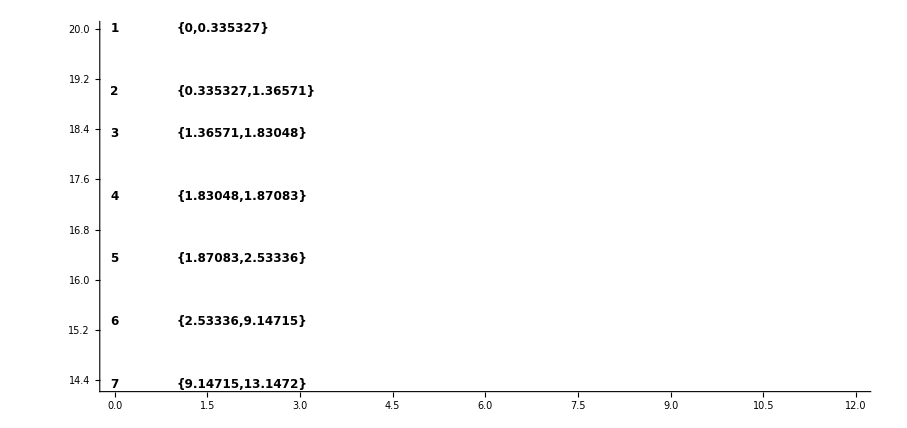

```mathematica
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.1.3: Set up singular points

Annulus 4 has a pole link

annulus monodromy: {{1,2},{3}}

pole links: {{7,3,3,3},{8,2,1,2}}

nextPoleLink: nextPoleLink

Processing pole link {7,3,3,3}

Annulus branch sheet: 3

annulusBranchIndex: 2

Singular point: 7

Sing pole links: {3,3,3}

y-offset for this sing: 17

nextPoleLink: nextPoleLink

Processing pole link {8,2,1,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 8

Sing pole links: {2,1,2}

y-offset for this sing: 50/3

Pole: -1.871

Pole: 1.871

poleLinkGraphicsData: {{4,7,17,2,{3,3,3}},{4,8,50/3,1,{2,1,2}}}

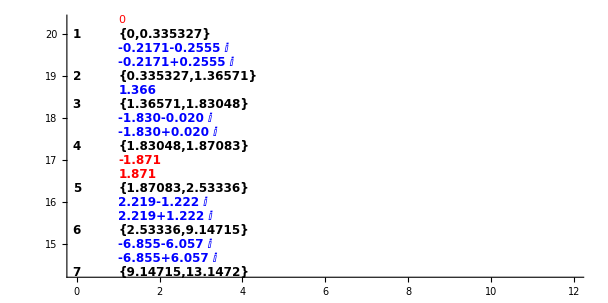

```mathematica
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.1.3: Set up singular indexes

sIndex: {3,4}

sIndex: {6}

sIndex: {8,9}

sIndex: {11,12}

sIndex: {14,15}

sIndex: {17,18}

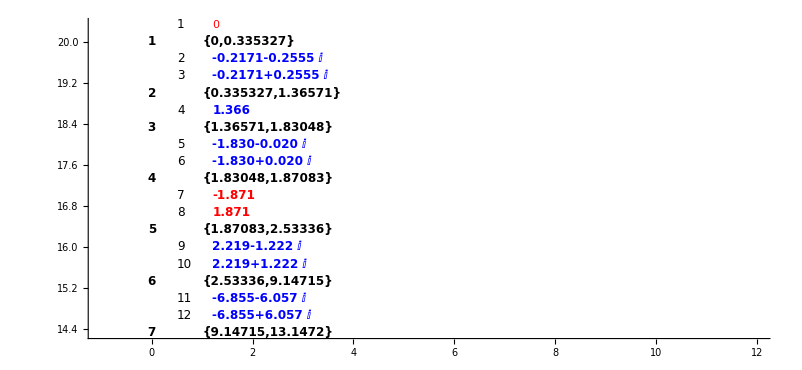

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.1.4: Set up singular monodromies

singular monodromies: {{{1},{2},{3}},{{2,3},{1}},{{2,3},{1}},{{2,3},{1}},{{2,3},{1}},{{1,2},{3}},{{1,2},{3}},{{1},{2},{3}},{{2,3},{1}},{{1,3},{2}}}

(1 | {{1},{2},{3}} | 0.166667
2 | {{2,3},{1}} | 0.158927
3 | {{2,3},{1}} | 0.158927
4 | {{2,3},{1}} | 0.162353
5 | {{2,3},{1}} | 0.162353
6 | {{1,2},{3}} | 0.158927
7 | {{1,2},{3}} | 0.158927
8 | {{1},{2},{3}} | 0.205603
9 | {{2,3},{1}} | 0.205603
10 | {{1,3},{2}} | 0.205603)

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{2,3},{1}}

«1 more identical outputs»

the sing monodromy: {{1,2},{3}}

the sing monodromy: {{1,2},{3}}

the sing monodromy: {{1},{2},{3}}

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{1,3},{2}}

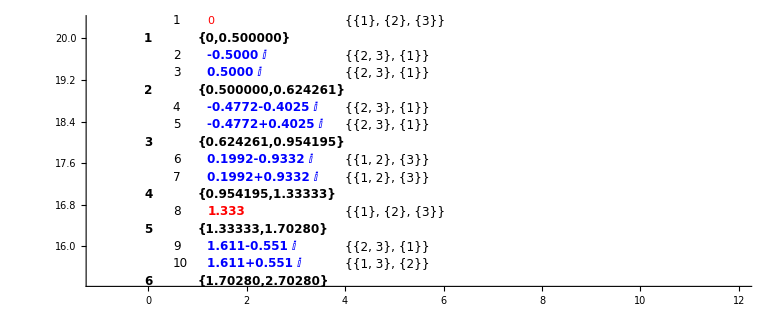

```mathematica
(*
 do singular monodromies
*)
 sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
Print["singular monodromies: ",singularMonodromies];
MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm

 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.1.5: Set up annular monodromies

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

#### Section 8.1.6: Set up pole link graphics

```mathematica
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(4 | 8 | 50/3 | 1 | {1,3,1})

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5}
4 | 17 | {5}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2})

currentBranchIndex: 1

currentAnnulus: 4

current sing index: 8

xLocationPos: 4

xLocationData: {4,17,{5}}

xLocation for this link: 5

yLocation for this link: 50/3

pole link string: {1,3,1}

#### Section 8.1.7: Create the continuation diagram

```mathematica
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
```

(1 | {{{1},{1}}}
4 | {{{1,3,2},{1,3,2}}})

{1,{{{1},{1}}}}

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5}
4 | 17 | {5}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2})

{2,{3,4}}

preMonodromy: {{1},{2},{3}}

{5,{6,7}}

postMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

1

1

1

2

20

19

5/2

5/2

0.1

#### Section 8.1.9: Create pole records

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True

#### Section 8.1.10: Create continuation arrows

```mathematica
contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,3,2}}

postMonodromy: {{1,3,2}}

postMonodromy: {{1,3,2}}

currentPreBranch: {1,3,2}

testa

testb

Creating dashed arrow

current pre branch: {1,3,2}

#### Section 8.1.8: Create continuation graphics

#### Set up annulus indexes

11.25

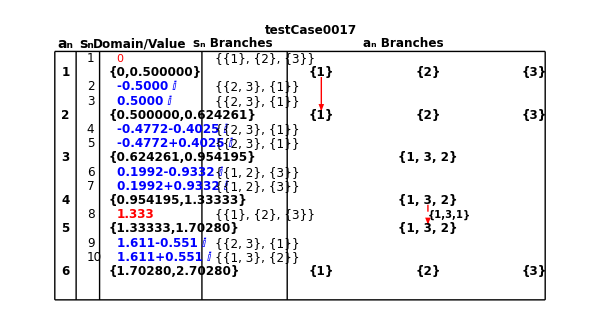

```mathematica
annularMonodromyOffSet=3.5;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.2,20.5},{5.2,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{3.5,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]},ImageSize->600]
```

### Section 8.2: Create Annular continuation diagram for testCase0025 with n=5

#### Section 8.2.1: Set up annular numbers

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3; (* offset of annular lines in table *)
sgIndex=1/3; (* offset of singular lines in table *)
yOffSet=20; (* begin annulus indexes at coordinate (0,20) and go down *)
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet;
Print["Coordinates for annular indexes: ",annuliLoc]
```

Coordinates for annular indexes: {{1,20},{2,58/3},{3,56/3},{4,18},{5,52/3}}

#### Section 8.2.2: Set up the annular domains

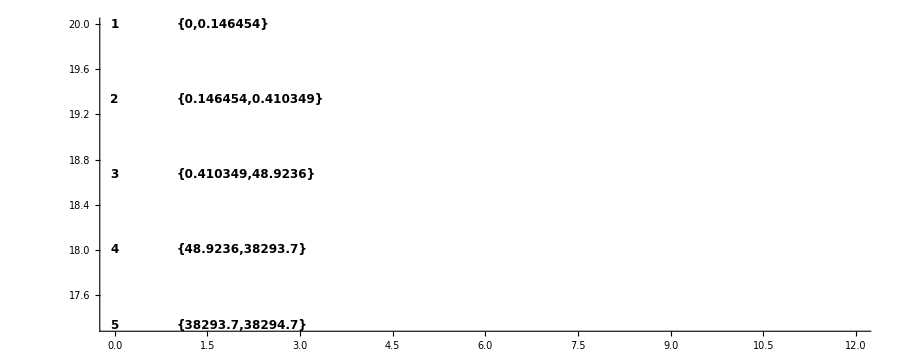

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];

Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.2.3: Set up singular points

poleLinkGraphicsData: {}

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

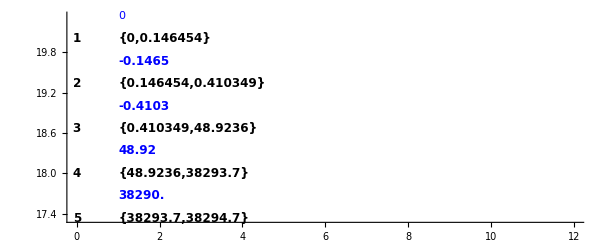

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];
];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.2.4: Create singular indexes

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

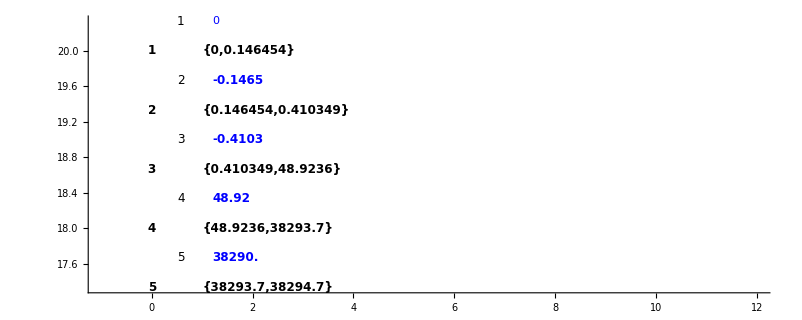

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["sIndex: ",sIndex];*)
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.2.5: Set up singular monodromies

```mathematica
singularMonodromies
```

{{{1},{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13}},{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10,11},{12},{13},{14},{15}},{{1},{2},{3},{4},{5},{6,7},{8},{9},{10},{11},{12},{13},{14},{15}},{{1},{2},{3,4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}},{{1,2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}}}

(1 | {{1},{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13}} | 0.048818
2 | {{1},{2},{3},{4},{5},{6},{7},{8},{9},{10,11},{12},{13},{14},{15}} | 0.048818
3 | {{1},{2},{3},{4},{5},{6,7},{8},{9},{10},{11},{12},{13},{14},{15}} | 0.0879649
4 | {{1},{2},{3,4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}} | 10.
5 | {{1,2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}} | 10.)

the sing monodromy: {{1},{2},{3},{4},{5},{6},{7},{8},{9},{10,11},{12},{13},{14},{15}}

the sing monodromy: {{1},{2},{3},{4},{5},{6,7},{8},{9},{10},{11},{12},{13},{14},{15}}

the sing monodromy: {{1},{2},{3,4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}}

the sing monodromy: {{1,2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}}

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

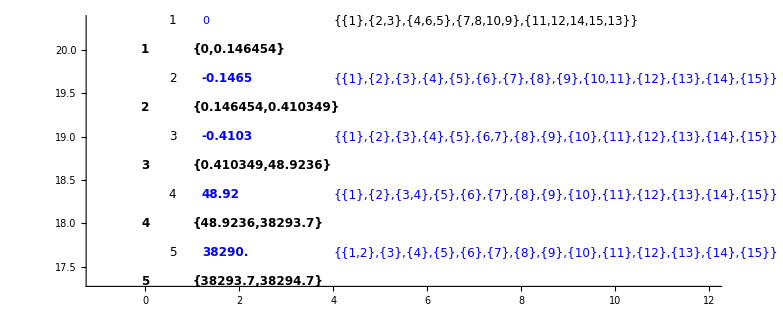

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];

MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm
yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.2.6: Set up annular monodromes

Adjust full size of the monodromy to fit all cycles without overlapping.  This is controlled by variable maxWidth.  Increase for larger-length monodromies.

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13},{1}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

x-locations: {2,4,6,8}

Monodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

x-locations: {5/2,5,15/2}

Monodromy: {{2,4,6,8,10,12,14,15,13,11,9,7,5,3},{1}}

x-locations: {10/3,20/3}

Monodromy: {{1,2,4,6,8,10,12,14,15,13,11,9,7,5,3}}

x-locations: {5}

#### Section 8.2.6: Create the pole link graphics

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

{}

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 58/3 | {2,4,6,8}
3 | 56/3 | {5/2,5,15/2}
4 | 18 | {10/3,20/3}
5 | 52/3 | {5})

#### Section 8.2.7: Create continuation records

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
```

(1 | {{{2,3},{2,3}},{{4,6,5},{4,6,5}},{{1},{1}}}
2 | {{{2,3},{2,3}},{{1},{1}}}
3 | {{{1},{1}}})

{1,{{{2,3},{2,3}},{{4,6,5},{4,6,5}},{{1},{1}}}}

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 58/3 | {2,4,6,8}
3 | 56/3 | {5/2,5,15/2}
4 | 18 | {10/3,20/3}
5 | 52/3 | {5})

{2,{3}}

preMonodromy: {{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13},{1}}

{4,{5}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

1

1

1

2

20

58/3

5/3

2

0.1

#### Section 8.2.8: Create pole records

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag

#### Section 8.2.9: Create arrows

```mathematica
(*
 do arrows
*)


  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

currentPreBranch: {2,3}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

currentPreBranch: {4,6,5}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,3},{4,6,5},{7,8,10,9},{11,12,14,15,13},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

postMonodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

currentPreBranch: {2,3}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{2,3},{4,6,5},{7,8,10,12,14,15,13,11,9},{1}}

postMonodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

postMonodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{2,3},{4,6,8,10,12,14,15,13,11,9,7,5},{1}}

postMonodromy: {{2,4,6,8,10,12,14,15,13,11,9,7,5,3},{1}}

postMonodromy: {{2,4,6,8,10,12,14,15,13,11,9,7,5,3},{1}}

currentPreBranch: {1}

testa

testb

#### Section 8.2.10: Show annular table graphics with pole data

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

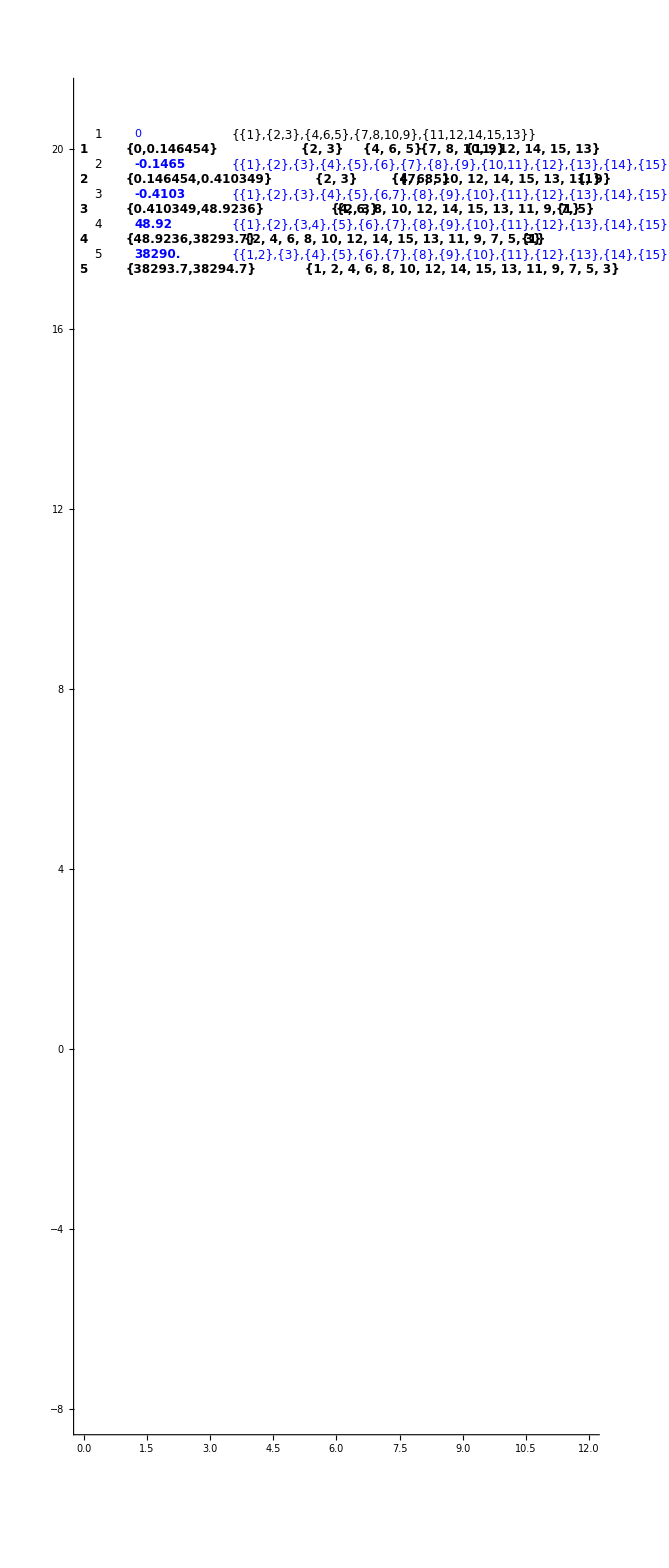

```mathematica
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{4,0}],
Graphics@Translate[poleLinkGraphics,{4,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
```

#### Section 8.2.11: Display full annular table graphics (note each graphics element is translated appropriateld to fit on the page

127/12

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

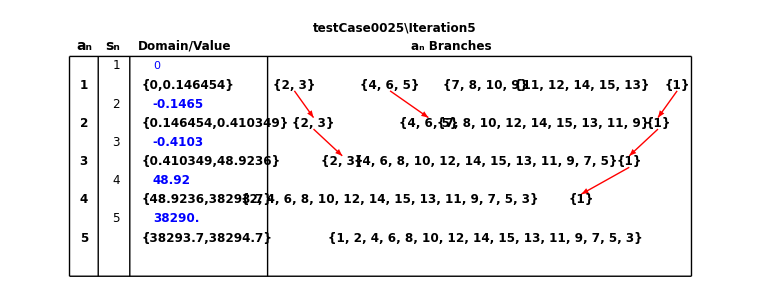

```mathematica
annularMonodromyOffSet=2;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.4,20.5},{5.4,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{6.4,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
(*Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],*)Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,(*text4,*)text5,vLine1,vLine2,vLine3,vLine4,(*vLine5,*)vLine6,
Graphics@Translate[arrowTable,{annularMonodromyOffSet,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Section 8.3: Create Annular continuation diagram for testCase0033

#### Section 8.3.1: Set up annular indexes

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

41/3

{{1,20},{2,19},{3,55/3},{4,52/3},{5,49/3},{6,46/3},{7,43/3}}

#### Section 8.3.2: Set up annulus

k: 1 domain: {0.,0.223263}

k: 2 domain: {0.223263,2.07279}

k: 3 domain: {2.07279,2.79826}

k: 4 domain: {2.79826,3.}

k: 5 domain: {3.,3.04039}

k: 6 domain: {3.04039,6.0783}

43/3

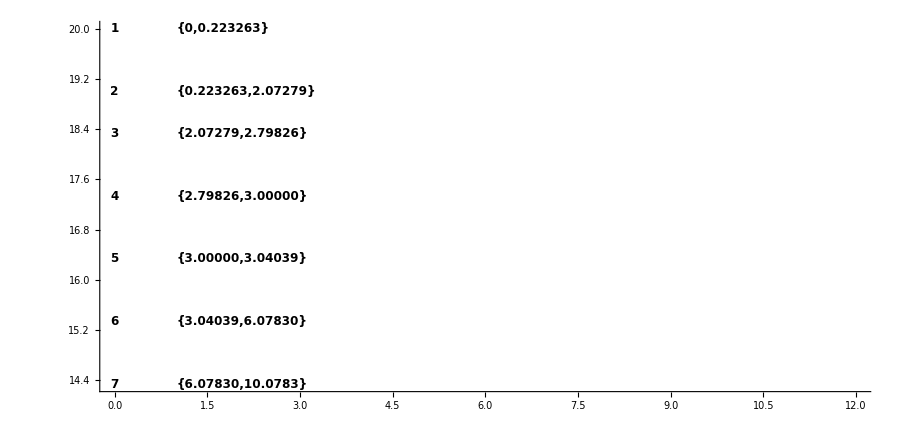

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.3.3: Set up singular points

Annulus 4 has a pole link

annulus monodromy: {{1,3},{2}}

pole links: {{7,2,1,2},{8,3,3,3}}

nextPoleLink: nextPoleLink

Processing pole link {7,2,1,2}

Annulus branch sheet: 2

annulusBranchIndex: 2

Singular point: 7

Sing pole links: {2,1,2}

y-offset for this sing: 17

nextPoleLink: nextPoleLink

Processing pole link {8,3,3,3}

Annulus branch sheet: 3

annulusBranchIndex: 1

Singular point: 8

Sing pole links: {3,3,3}

y-offset for this sing: 50/3

Pole: -3.000

Pole: 3.000

poleLinkGraphicsData: {{4,7,17,2,{2,1,2}},{4,8,50/3,1,{3,3,3}}}

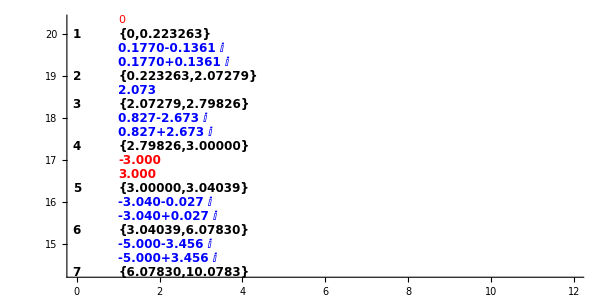

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.3.4: Set up singular indexes

sIndex: {3,4}

sIndex: {6}

sIndex: {8,9}

sIndex: {11,12}

sIndex: {14,15}

sIndex: {17,18}

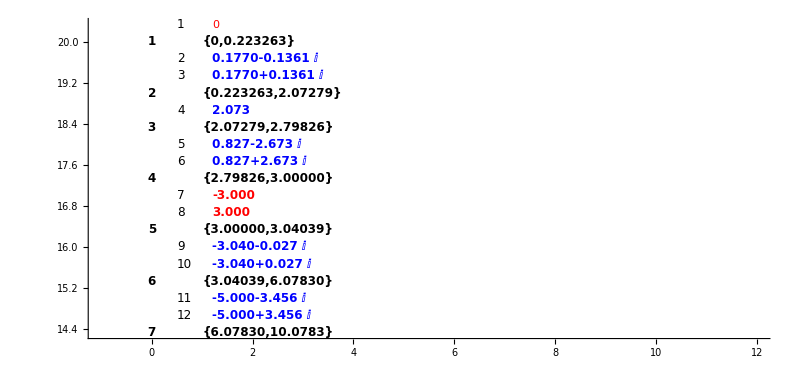

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.3.5: Set up singular monodromies

(1 | {{2},{1},{3}} | 0.074421
2 | {{1},{2,3}} | 0.074421
3 | {{1},{2,3}} | 0.074421
4 | {{1,2},{3}} | 0.309069
5 | {{1},{3,2}} | 0.873038
6 | {{1},{2,3}} | 0.873038
7 | {{2},{3},{1}} | 0.0162237
8 | {{1},{2},{3}} | 0.309069
9 | {{1},{2,3}} | 0.0162237
10 | {{1},{3,2}} | 0.0162237
11 | {{1},{3,2}} | 1.31643
12 | {{1},{2,3}} | 1.31643)

the sing monodromy: {{1},{2,3}}

the sing monodromy: {{1},{2,3}}

the sing monodromy: {{1,2},{3}}

the sing monodromy: {{1},{3,2}}

the sing monodromy: {{1},{2,3}}

the sing monodromy: {{2},{3},{1}}

the sing monodromy: {{1},{2},{3}}

the sing monodromy: {{1},{2,3}}

the sing monodromy: {{1},{3,2}}

the sing monodromy: {{1},{3,2}}

the sing monodromy: {{1},{2,3}}

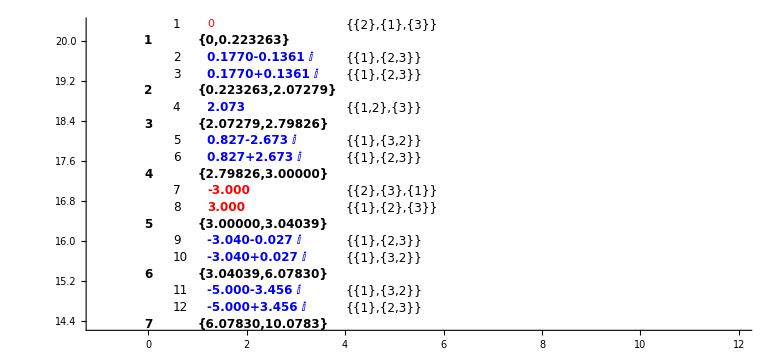

```mathematica
(*
 do singular monodromies
*)
If[FileExistsQ[singularMonodromyFileName[$theTestCase]],
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
 Print[MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm];

 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Print[Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]];
,
Print[Style[singularMonodromyFileName[$theTestCase]<>" not found during import.",Red]];
];
```

#### Section 8.3.6: Set up annular monodromies

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
```

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,3}}

x-locations: {5}

Monodromy: {{1,3},{2}}

x-locations: {10/3,20/3}

Monodromy: {{1,3},{2}}

x-locations: {10/3,20/3}

Monodromy: {{1,3},{2}}

x-locations: {10/3,20/3}

Monodromy: {{2,3},{1}}

x-locations: {10/3,20/3}

Monodromy: {{1,2},{3}}

x-locations: {10/3,20/3}

#### Section 8.3.7: Set up pole links

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(4 | 7 | 17 | 2 | {2,1,2}
4 | 8 | 50/3 | 1 | {3,3,3})

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5}
3 | 55/3 | {10/3,20/3}
4 | 52/3 | {10/3,20/3}
5 | 49/3 | {10/3,20/3}
6 | 46/3 | {10/3,20/3}
7 | 43/3 | {10/3,20/3})

currentBranchIndex: 2

currentAnnulus: 4

current sing index: 7

xLocationPos: 4

xLocationData: {4,52/3,{10/3,20/3}}

xLocation for this link: 20/3

yLocation for this link: 17

pole link string: {2,1,2}

currentBranchIndex: 1

currentAnnulus: 4

current sing index: 8

xLocationPos: 4

xLocationData: {4,52/3,{10/3,20/3}}

xLocation for this link: 10/3

yLocation for this link: 50/3

pole link string: {3,3,3}

#### Section 8.3.8: Create continuation diagram

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];

poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

(4 | {{{1,3},{1,3}},{{2},{2}}})

{4,{{{1,3},{1,3}},{{2},{2}}}}

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5}
3 | 55/3 | {10/3,20/3}
4 | 52/3 | {10/3,20/3}
5 | 49/3 | {10/3,20/3}
6 | 46/3 | {10/3,20/3}
7 | 43/3 | {10/3,20/3})

{10,{11,12}}

preMonodromy: {{1,3},{2}}

{13,{14,15}}

postMonodromy: {{1,3},{2}}

postMonodromy: {{1,3},{2}}

1

1

4

5

52/3

49/3

10/3

10/3

0.1

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
4 | {1,3} | 3 | 8 | L_-1 | {3} | 3 | True | {1,3} | 3 | True
4 | {2} | 2 | 7 | L_-1 | {1} | 1 | True | {2} | 2 | True

#### Section 8.3.9: Set up arrows

```mathematica
(*
 do arrows
*)


  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,3},{2}}

postMonodromy: {{1,3},{2}}

postMonodromy: {{1,3},{2}}

currentPreBranch: {1,3}

testa

testb

Creating dashed arrow

current pre branch: {1,3}

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,3},{2}}

postMonodromy: {{1,3},{2}}

postMonodromy: {{1,3},{2}}

currentPreBranch: {2}

testa

testb

Creating dashed arrow

current pre branch: {2}

#### Section 8.3.10: Create annular branch links graphics

11.25

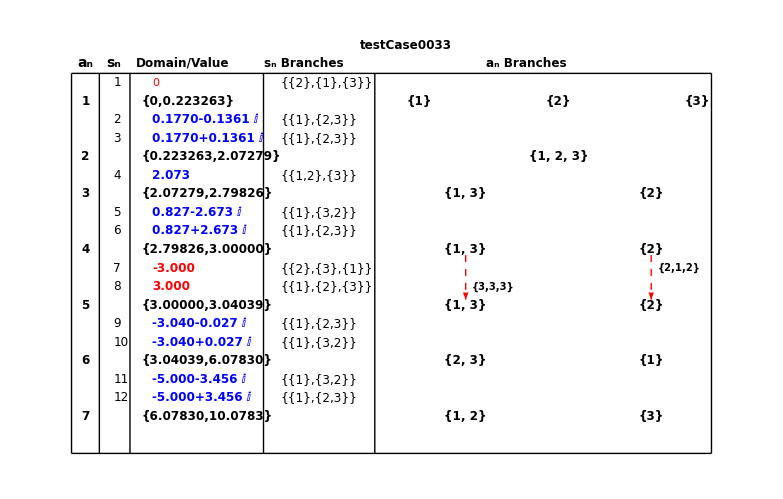

```mathematica
annularMonodromyOffSet=3.5;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.2,20.5},{5.2,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{3.5,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Section 8.4: Create Annular continuation diagram for testCase0035

#### Section 8.4.1: Set up annulus numbers

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3; (* offset of annular lines in table *)
sgIndex=1/3; (* offset of singular lines in table *)
yOffSet=20; (* begin annulus indexes at coordinate (0,20) and go down *)
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet;
Print["Coordinates for annular indexes: ",annuliLoc]
```

Coordinates for annular indexes: {{1,20},{2,19},{3,55/3},{4,52/3},{5,49/3},{6,46/3},{7,43/3},{8,40/3},{9,38/3},{10,35/3},{11,32/3},{12,10},{13,9},{14,8},{15,22/3},{16,19/3},{17,16/3},{18,13/3},{19,11/3},{20,8/3},{21,5/3},{22,2/3},{23,-1/3},{24,-4/3},{25,-7/3},{26,-10/3},{27,-4},{28,-5},{29,-17/3}}

#### Section 8.4.2: Set up the annular regions

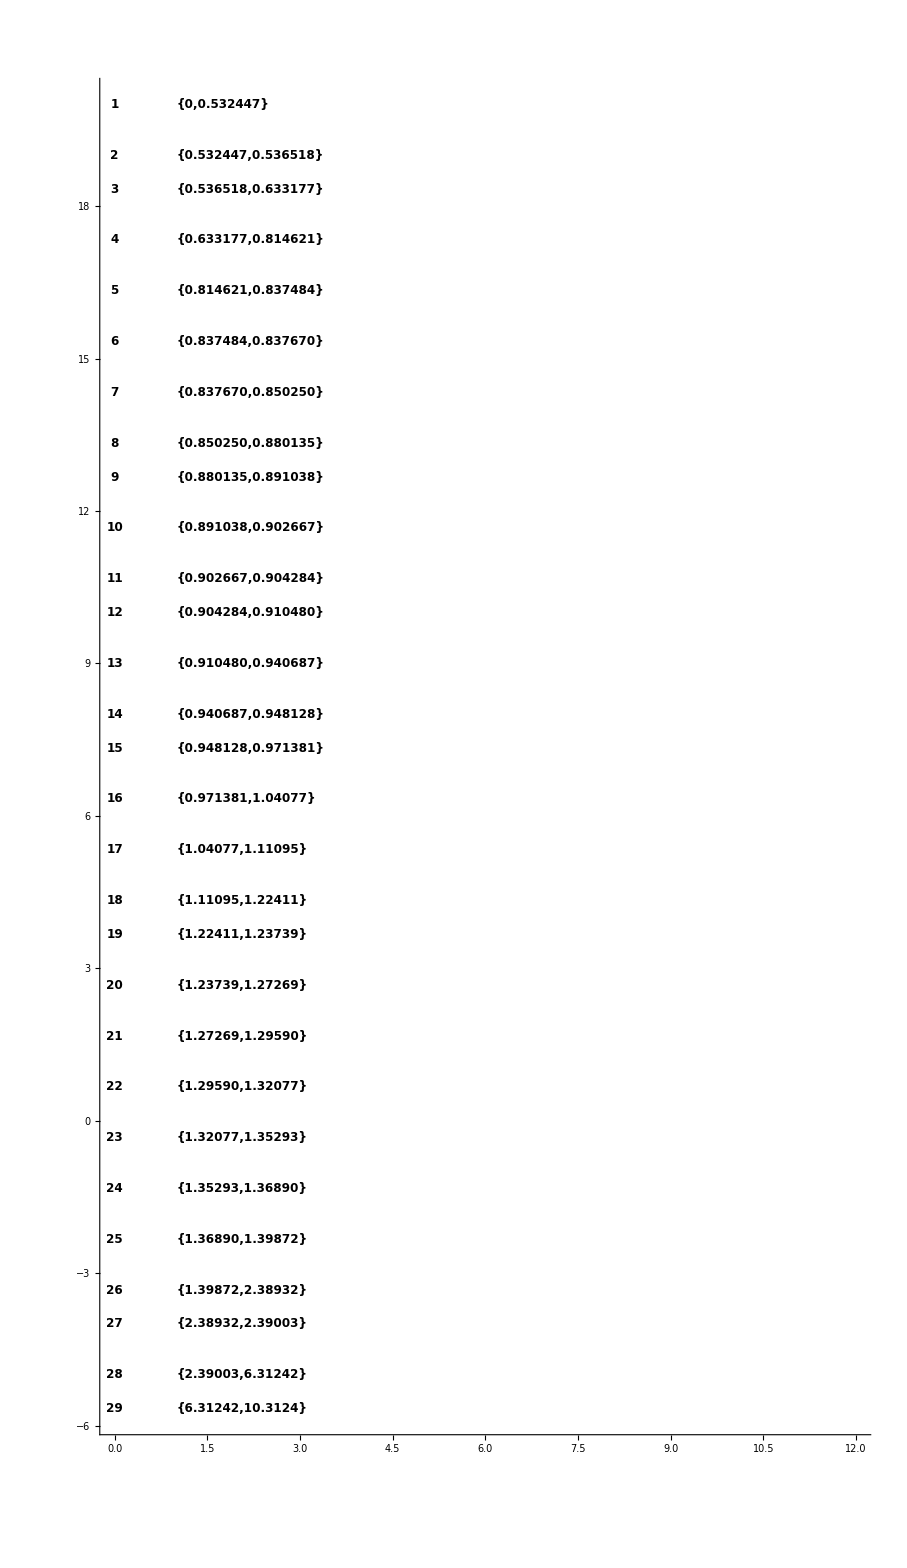

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];

Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.4.3: Set up singular points

Annulus 11 has a pole link

annulus monodromy: {{1},{2},{3},{4},{5}}

pole links: {{19,2,5,2}}

nextPoleLink: nextPoleLink

Processing pole link {19,2,5,2}

Annulus branch sheet: 2

annulusBranchIndex: 2

Singular point: 19

Sing pole links: {2,5,2}

y-offset for this sing: 31/3

Pole: -0.9043

Annulus 17 has a pole link

annulus monodromy: {{1,5},{2},{3},{4}}

pole links: {{29,2,5,2},{30,4,2,4}}

nextPoleLink: nextPoleLink

Processing pole link {29,2,5,2}

Annulus branch sheet: 2

annulusBranchIndex: 2

Singular point: 29

Sing pole links: {2,5,2}

y-offset for this sing: 5

nextPoleLink: nextPoleLink

Processing pole link {30,4,2,4}

Annulus branch sheet: 4

annulusBranchIndex: 4

Singular point: 30

Sing pole links: {4,2,4}

y-offset for this sing: 14/3

Pole: 0.4241-1.0268 ⅈ

Pole: 0.4241+1.0268 ⅈ

Annulus 26 has a pole link

annulus monodromy: {{1,2,5},{3},{4}}

pole links: {{46,2,5,2}}

nextPoleLink: nextPoleLink

Processing pole link {46,2,5,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 46

Sing pole links: {2,5,2}

y-offset for this sing: -11/3

Pole: 2.389

poleLinkGraphicsData: {{11,19,31/3,2,{2,5,2}},{17,29,5,2,{2,5,2}},{17,30,14/3,4,{4,2,4}},{26,46,-11/3,1,{2,5,2}}}

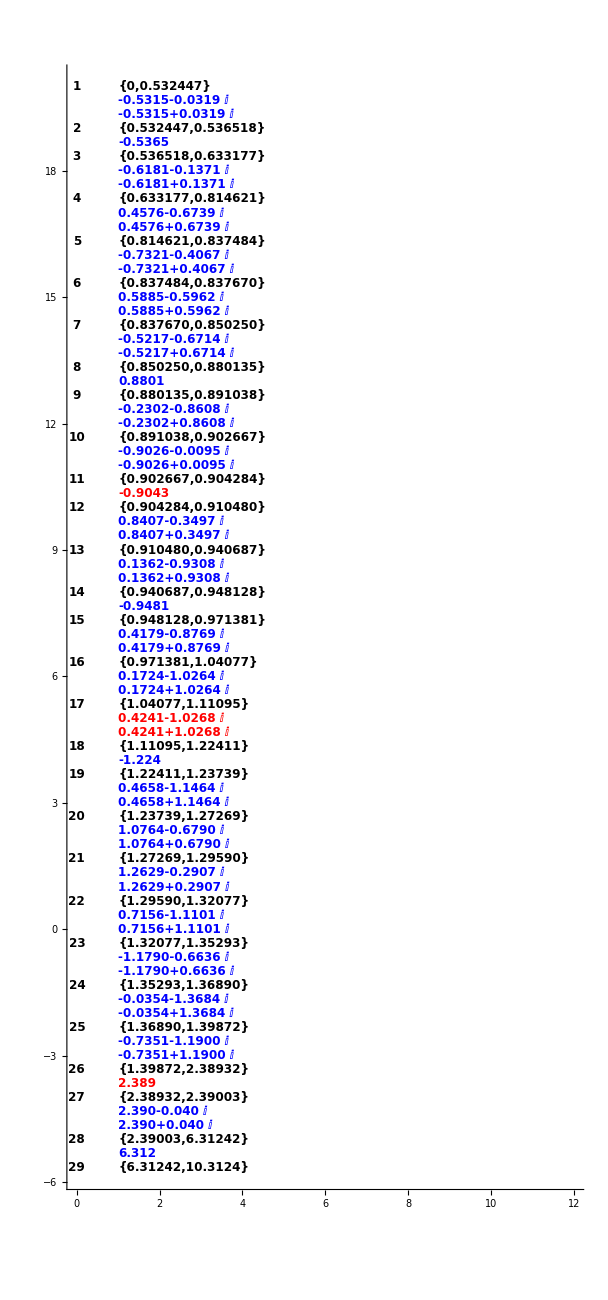

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];
];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.4.4: Create singular indexes

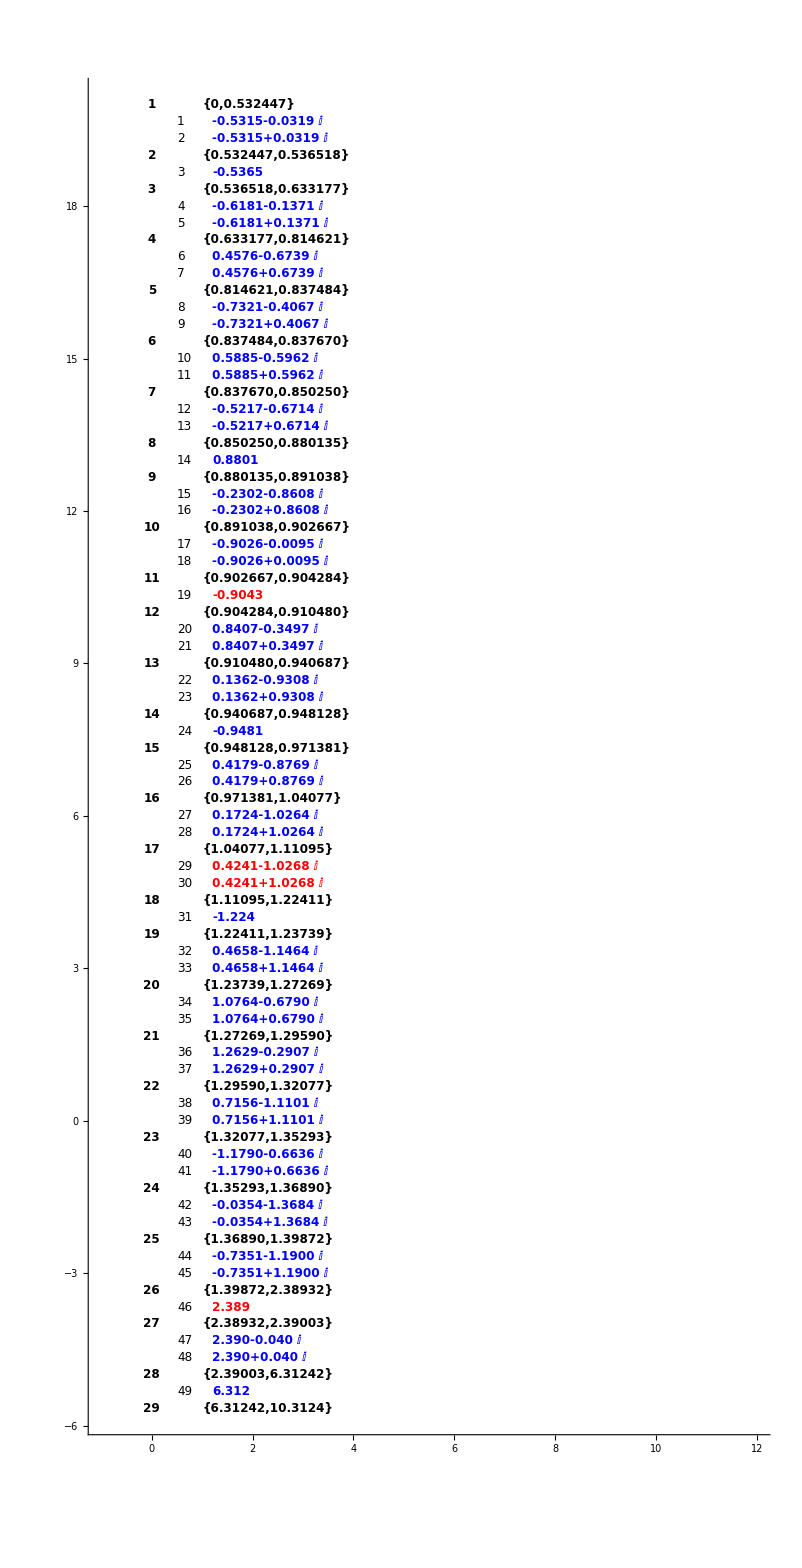

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["sIndex: ",sIndex];*)
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.4.5: Set up singular monodromies

(1 | {{2,3},{1},{4},{5}} | 0.010756
2 | {{2,4},{1},{3},{5}} | 0.010756
3 | {{1,2},{3},{4},{5}} | 0.010756
4 | {{4,5},{1},{2},{3}} | 0.0454477
5 | {{4,5},{1},{2},{3}} | 0.0454477
6 | {{3,5},{1},{2},{4}} | 0.0507449
7 | {{3,5},{1},{2},{4}} | 0.0507449
8 | {{3,4},{1},{2},{5}} | 0.0975567
9 | {{3,5},{1},{2},{4}} | 0.0975567
10 | {{3,5},{1},{2},{4}} | 0.0507449
11 | {{3,5},{1},{2},{4}} | 0.0507449
12 | {{2,3},{1},{4},{5}} | 0.112712
13 | {{2,3},{1},{4},{5}} | 0.112712
14 | {{1,2},{3},{4},{5}} | 0.117294
15 | {{1,2},{3},{4},{5}} | 0.115853
16 | {{1,2},{3},{4},{5}} | 0.115853
17 | {{2,5},{1},{3},{4}} | 0.00320006
18 | {{2,5},{1},{3},{4}} | 0.00320006
19 | {{1},{2},{3},{4},{5}} | 0.00320006
20 | {{2,3},{1},{4},{5}} | 0.117294
21 | {{2,3},{1},{4},{5}} | 0.117294
22 | {{2,4},{1},{3},{5}} | 0.0340866
23 | {{3,4},{1},{2},{5}} | 0.0340866
24 | {{1,2},{3},{4},{5}} | 0.0146144
25 | {{4,5},{1},{2},{3}} | 0.0500042
26 | {{4,5},{1},{2},{3}} | 0.0500042
27 | {{1,2},{3},{4},{5}} | 0.0340866
28 | {{1,2},{3},{4},{5}} | 0.0340866
29 | {{1},{2},{3},{4},{5}} | 0.0422057
30 | {{1},{2},{3},{4},{5}} | 0.0422057
31 | {{1,2},{3},{4},{5}} | 0.091993
32 | {{1,2},{3},{4},{5}} | 0.0422057
33 | {{1,2},{3},{4},{5}} | 0.0422057
34 | {{1,4},{2},{3},{5}} | 0.135011
35 | {{2,3},{1},{4},{5}} | 0.135011
36 | {{4,5},{1},{2},{3}} | 0.142098
37 | {{4,5},{1},{2},{3}} | 0.142098
38 | {{1,2},{3},{4},{5}} | 0.0841411
39 | {{1,2},{3},{4},{5}} | 0.0841411
40 | {{2,4},{1},{3},{5}} | 0.171827
41 | {{2,4},{1},{3},{5}} | 0.171827
42 | {{2,5},{1},{3},{4}} | 0.133418
43 | {{3,5},{1},{2},{4}} | 0.133418
44 | {{4,5},{1},{2},{3}} | 0.186929
45 | {{4,5},{1},{2},{3}} | 0.186929
46 | {{1},{2},{3},{4},{5}} | 0.0133534
47 | {{1,5},{2},{3},{4}} | 0.0133534
48 | {{1,5},{2},{3},{4}} | 0.0133534
49 | {{3,4},{1},{2},{5}} | 1.30764)

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,4},{1},{2},{5}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{2,5},{1},{3},{4}}

the sing monodromy: {{2,5},{1},{3},{4}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{3,4},{1},{2},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,4},{2},{3},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{2,5},{1},{3},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1,5},{2},{3},{4}}

the sing monodromy: {{1,5},{2},{3},{4}}

the sing monodromy: {{3,4},{1},{2},{5}}

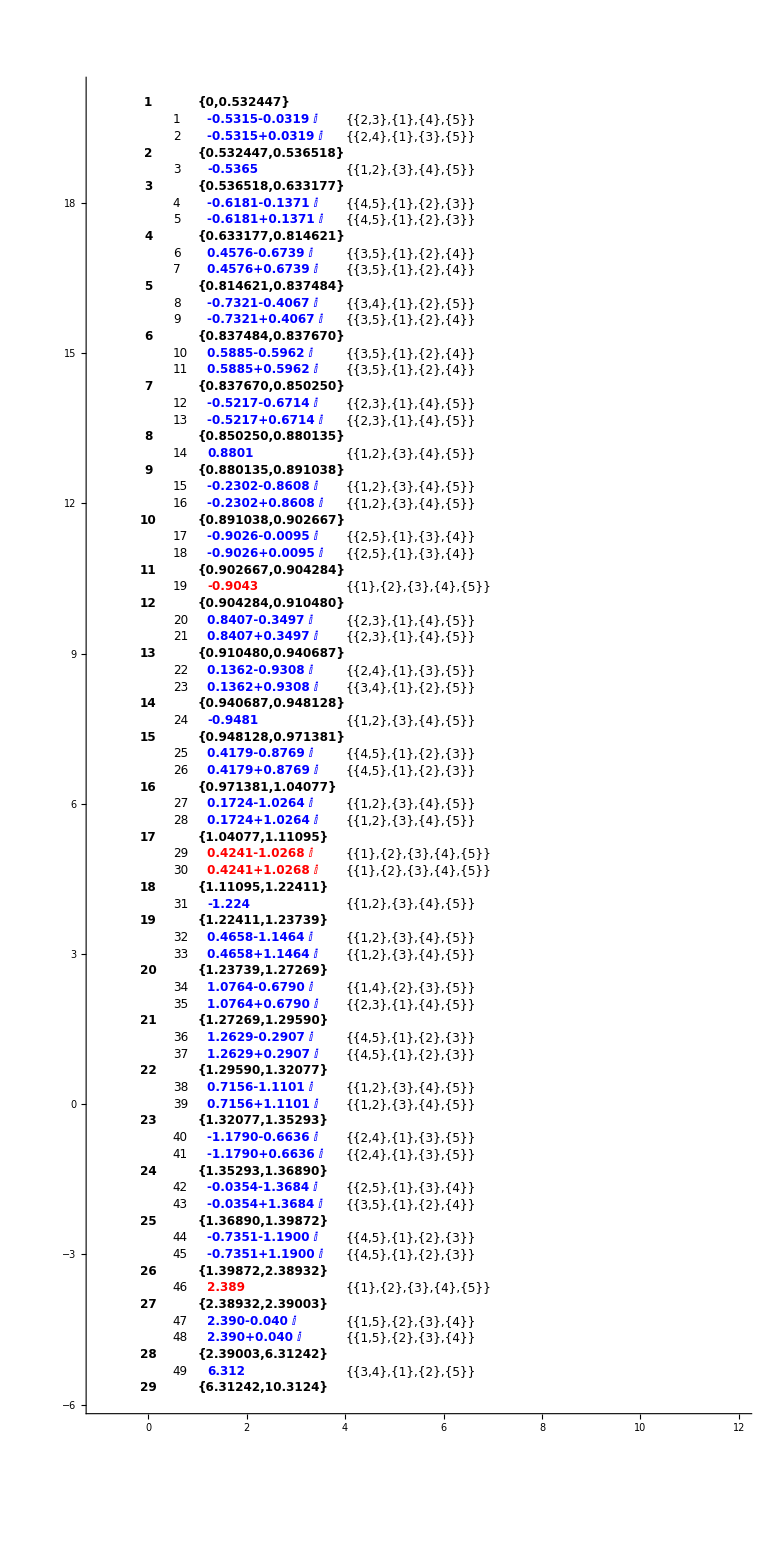

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm
yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.4.6: Set up annular monodromes

Adjust full size of the monodromy to fit all cycles without overlapping.  This is controlled by variable maxWidth.  Increase for larger-length monodromies.

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{1,4},{2,3},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,4,3,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,4,3,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,4,3,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4},{2},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{2,3,4},{1},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{2,4,3},{1},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,4},{3},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,5,4},{3}}

x-locations: {10/3,20/3}

Monodromy: {{1,5},{2},{3},{4}}

x-locations: {2,4,6,8}

Monodromy: {{1,5},{2},{3},{4}}

x-locations: {2,4,6,8}

Monodromy: {{1,5},{2},{3},{4}}

x-locations: {2,4,6,8}

Monodromy: {{1,5},{2,4},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,5},{2},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3},{2,5},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,5,2},{3},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,5,2},{3},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{1,3,5},{2},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,5},{3},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,5},{3},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{3,4},{1},{2},{5}}

x-locations: {2,4,6,8}

#### Section 8.4.7: Create the pole link graphics

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(11 | 19 | 31/3 | 2 | {2,5,2}
17 | 29 | 5 | 2 | {2,5,2}
17 | 30 | 14/3 | 4 | {4,2,4}
26 | 46 | -11/3 | 1 | {2,5,2})

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 19 | {5/2,5,15/2}
3 | 55/3 | {10/3,20/3}
4 | 52/3 | {10/3,20/3}
5 | 49/3 | {10/3,20/3}
6 | 46/3 | {10/3,20/3}
7 | 43/3 | {10/3,20/3}
8 | 40/3 | {10/3,20/3}
9 | 38/3 | {5/2,5,15/2}
10 | 35/3 | {5/2,5,15/2}
11 | 32/3 | {5/3,10/3,5,20/3,25/3}
12 | 10 | {5/3,10/3,5,20/3,25/3}
13 | 9 | {5/2,5,15/2}
14 | 8 | {5/2,5,15/2}
15 | 22/3 | {10/3,20/3}
16 | 19/3 | {2,4,6,8}
17 | 16/3 | {2,4,6,8}
18 | 13/3 | {2,4,6,8}
19 | 11/3 | {5/2,5,15/2}
20 | 8/3 | {5/2,5,15/2}
21 | 5/3 | {5/2,5,15/2}
22 | 2/3 | {5/2,5,15/2}
23 | -1/3 | {5/2,5,15/2}
24 | -4/3 | {5/3,10/3,5,20/3,25/3}
25 | -7/3 | {5/2,5,15/2}
26 | -10/3 | {5/2,5,15/2}
27 | -4 | {5/2,5,15/2}
28 | -5 | {5/3,10/3,5,20/3,25/3}
29 | -17/3 | {2,4,6,8})

currentBranchIndex: 2

currentAnnulus: 11

current sing index: 19

xLocationPos: 11

xLocationData: {11,32/3,{5/3,10/3,5,20/3,25/3}}

xLocation for this link: 10/3

yLocation for this link: 31/3

pole link string: {2,5,2}

currentBranchIndex: 2

currentAnnulus: 17

current sing index: 29

xLocationPos: 17

xLocationData: {17,16/3,{2,4,6,8}}

xLocation for this link: 4

yLocation for this link: 5

pole link string: {2,5,2}

currentBranchIndex: 4

currentAnnulus: 17

current sing index: 30

xLocationPos: 17

xLocationData: {17,16/3,{2,4,6,8}}

xLocation for this link: 8

yLocation for this link: 14/3

pole link string: {4,2,4}

currentBranchIndex: 1

currentAnnulus: 26

current sing index: 46

xLocationPos: 26

xLocationData: {26,-10/3,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: -11/3

pole link string: {2,5,2}

#### Section 8.4.8: Create continuation records

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
```

(1 | {{{5},{5}}}
2 | {{{5},{5}}}
5 | {{{5},{5}}}
8 | {{{5},{5}}}
9 | {{{5},{5}}}
10 | {{{1},{1}},{{5},{5}}}
11 | {{{1},{1}},{{2},{2}},{{3},{3}},{{4},{4}},{{5},{5}}}
12 | {{{1},{1}},{{5},{5}}}
13 | {{{5},{5}}}
14 | {{{3},{3}}}
15 | {{{3},{3}}}
16 | {{{1,5},{1,5}},{{3},{3}}}
17 | {{{1,5},{1,5}},{{2},{2}},{{3},{3}},{{4},{4}}}
18 | {{{1,5},{1,5}},{{3},{3}}}
19 | {{{3},{4}}}
20 | {{{4},{4}}}
21 | {{{4},{4}}}
22 | {{{4},{4}}}
23 | {{{3},{3}},{{4},{4}}}
24 | {{{2},{2}},{{4},{4}}}
25 | {{{4},{4}}}
26 | {{{1,2,5},{1,2,5}},{{3},{3}},{{4},{4}}}
27 | {{{3},{3}},{{4},{4}}}
28 | {{{1},{1}},{{2},{2}},{{5},{5}}})

{1,{{{5},{5}}}}

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 19 | {5/2,5,15/2}
3 | 55/3 | {10/3,20/3}
4 | 52/3 | {10/3,20/3}
5 | 49/3 | {10/3,20/3}
6 | 46/3 | {10/3,20/3}
7 | 43/3 | {10/3,20/3}
8 | 40/3 | {10/3,20/3}
9 | 38/3 | {5/2,5,15/2}
10 | 35/3 | {5/2,5,15/2}
11 | 32/3 | {5/3,10/3,5,20/3,25/3}
12 | 10 | {5/3,10/3,5,20/3,25/3}
13 | 9 | {5/2,5,15/2}
14 | 8 | {5/2,5,15/2}
15 | 22/3 | {10/3,20/3}
16 | 19/3 | {2,4,6,8}
17 | 16/3 | {2,4,6,8}
18 | 13/3 | {2,4,6,8}
19 | 11/3 | {5/2,5,15/2}
20 | 8/3 | {5/2,5,15/2}
21 | 5/3 | {5/2,5,15/2}
22 | 2/3 | {5/2,5,15/2}
23 | -1/3 | {5/2,5,15/2}
24 | -4/3 | {5/3,10/3,5,20/3,25/3}
25 | -7/3 | {5/2,5,15/2}
26 | -10/3 | {5/2,5,15/2}
27 | -4 | {5/2,5,15/2}
28 | -5 | {5/3,10/3,5,20/3,25/3}
29 | -17/3 | {2,4,6,8})

{1,{2,3}}

preMonodromy: {{1},{2},{3},{4},{5}}

{4,{5}}

postMonodromy: {{1,4},{2,3},{5}}

postMonodromy: {{1,4},{2,3},{5}}

5

3

1

2

20

19

25/3

15/2

0.1

#### Section 8.4.9: Create pole records

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
11 | {2} | 2 | 19 | L_-1 | {5} | 5 | True | {2} | 2 | True
17 | {2} | 2 | 29 | L_-1 | {5} | 5 | True | {2} | 2 | True
17 | {4} | 4 | 30 | L_-1 | {2} | 2 | True | {4} | 4 | True
26 | {1,2,5} | 2 | 46 | L_-1 | {5} | 5 | True | {1,2,5} | 2 | True

#### Section 8.4.10: Create arrows

```mathematica
(*
 do arrows
*)


  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,4},{2,3},{5}}

postMonodromy: {{1,4},{2,3},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{1,4},{2,3},{5}}

postMonodromy: {{1,4,3,2},{5}}

postMonodromy: {{1,4,3,2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{1,4,3,2},{5}}

postMonodromy: {{1,3,4,2},{5}}

postMonodromy: {{1,3,4,2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{1,3,4,2},{5}}

postMonodromy: {{1,3,4},{2},{5}}

postMonodromy: {{1,3,4},{2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{1,3,4},{2},{5}}

postMonodromy: {{2,3,4},{1},{5}}

postMonodromy: {{2,3,4},{1},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 10

currentContLink: 10

preMonodromy: {{2,3,4},{1},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 10

currentContLink: 10

preMonodromy: {{2,3,4},{1},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {2}

testa

testb

Creating dashed arrow

current pre branch: {2}

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 12

currentContLink: 12

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{2,4,3},{1},{5}}

postMonodromy: {{2,4,3},{1},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 12

currentContLink: 12

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{2,4,3},{1},{5}}

postMonodromy: {{2,4,3},{1},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 13

currentContLink: 13

preMonodromy: {{2,4,3},{1},{5}}

postMonodromy: {{1,2,4},{3},{5}}

postMonodromy: {{1,2,4},{3},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 14

currentContLink: 14

preMonodromy: {{1,2,4},{3},{5}}

postMonodromy: {{1,2,5,4},{3}}

postMonodromy: {{1,2,5,4},{3}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 15

currentContLink: 15

preMonodromy: {{1,2,5,4},{3}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 16

currentContLink: 16

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {1,5}

testa

testb

currentAnnulus: 16

currentContLink: 16

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {1,5}

testa

testb

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {2}

testa

testb

Creating dashed arrow

current pre branch: {2}

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2},{3},{4}}

currentPreBranch: {4}

testa

testb

Creating dashed arrow

current pre branch: {4}

currentAnnulus: 18

currentContLink: 18

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2,4},{3}}

postMonodromy: {{1,5},{2,4},{3}}

currentPreBranch: {1,5}

testa

testb

currentAnnulus: 18

currentContLink: 18

preMonodromy: {{1,5},{2},{3},{4}}

postMonodromy: {{1,5},{2,4},{3}}

postMonodromy: {{1,5},{2,4},{3}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 19

currentContLink: 19

preMonodromy: {{1,5},{2,4},{3}}

postMonodromy: {{1,3,5},{2},{4}}

postMonodromy: {{1,3,5},{2},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 20

currentContLink: 20

preMonodromy: {{1,3,5},{2},{4}}

postMonodromy: {{1,3},{2,5},{4}}

postMonodromy: {{1,3},{2,5},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 21

currentContLink: 21

preMonodromy: {{1,3},{2,5},{4}}

postMonodromy: {{1,5,2},{3},{4}}

postMonodromy: {{1,5,2},{3},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 22

currentContLink: 22

preMonodromy: {{1,5,2},{3},{4}}

postMonodromy: {{1,5,2},{3},{4}}

postMonodromy: {{1,5,2},{3},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 23

currentContLink: 23

preMonodromy: {{1,5,2},{3},{4}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 23

currentContLink: 23

preMonodromy: {{1,5,2},{3},{4}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,5},{2},{4}}

postMonodromy: {{1,3,5},{2},{4}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,5},{2},{4}}

postMonodromy: {{1,3,5},{2},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{1,3,5},{2},{4}}

postMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 26

currentContLink: 26

preMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

currentPreBranch: {1,2,5}

testa

testb

Creating dashed arrow

current pre branch: {1,2,5}

currentAnnulus: 26

currentContLink: 26

preMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 26

currentContLink: 26

preMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1,2,5},{3},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 27

currentContLink: 27

preMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 27

currentContLink: 27

preMonodromy: {{1,2,5},{3},{4}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 28

currentContLink: 28

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 28

currentContLink: 28

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 28

currentContLink: 28

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {5}

testa

testb

#### Section 8.4.11: Show annular table graphics with pole data

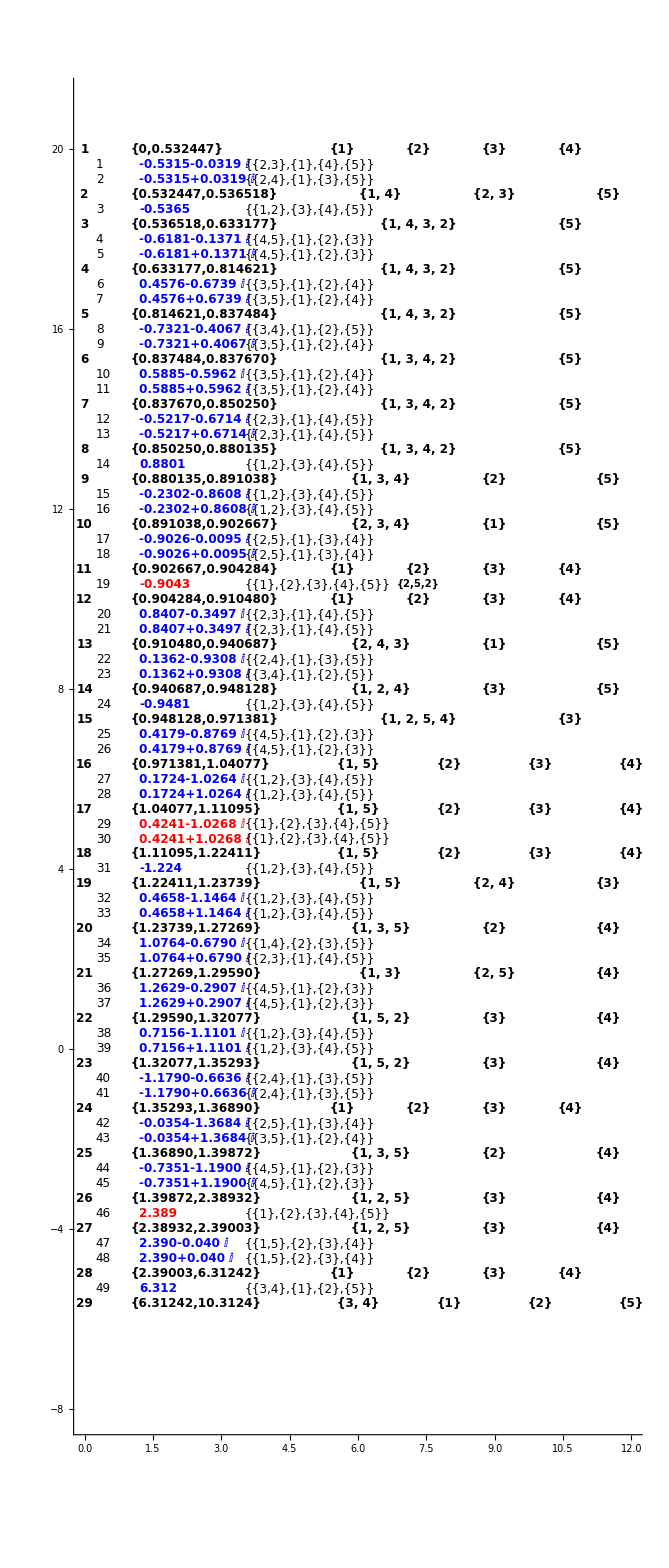

```mathematica
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{4,0}],
Graphics@Translate[poleLinkGraphics,{4,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
```

#### Section 8.4.12: Display full annular table graphics (note each graphics element is translated appropriately to fit on the page

151/12

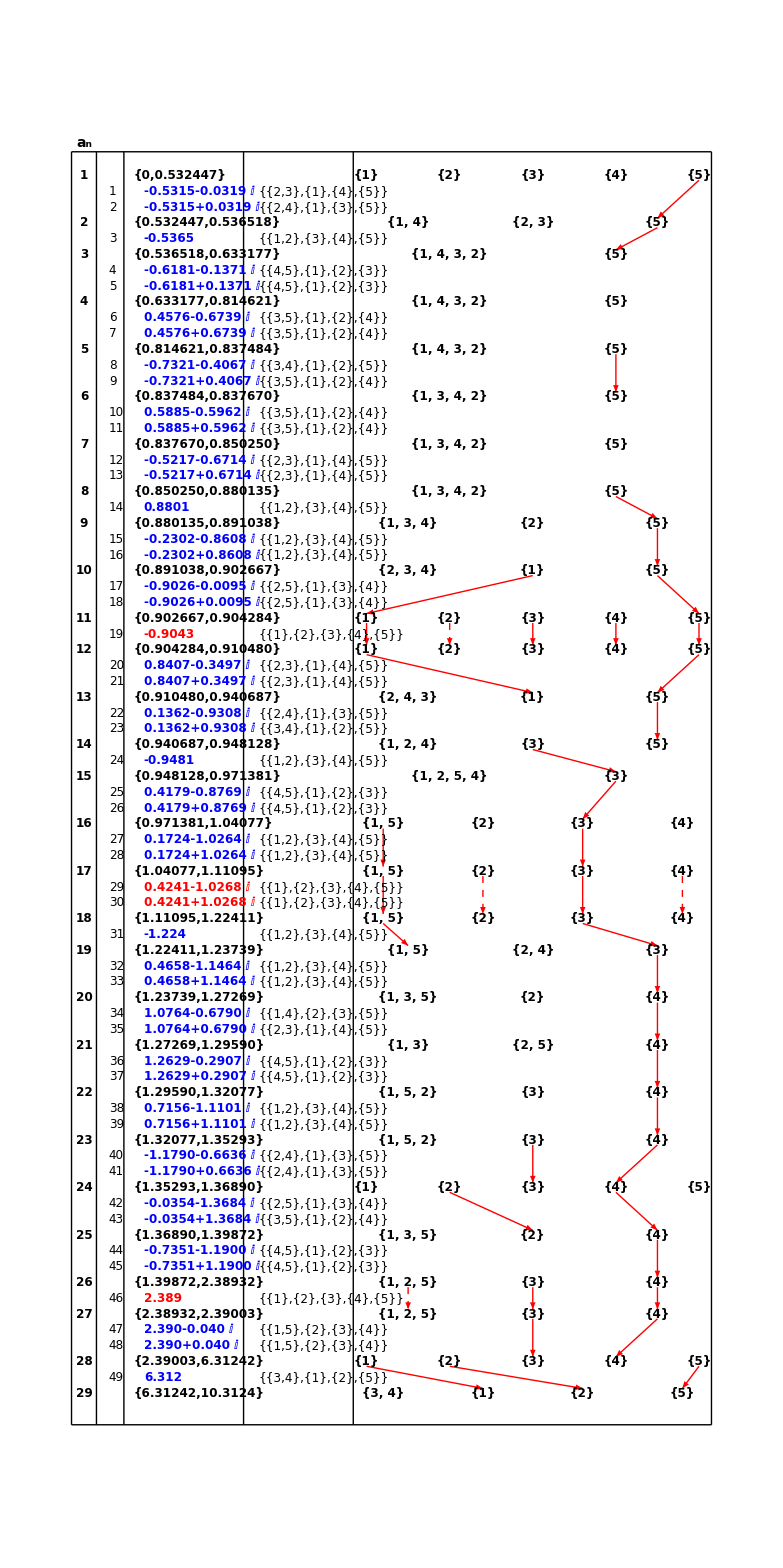

```mathematica
annularMonodromyOffSet=4;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.4,20.5},{5.4,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 

gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{annularMonodromyOffSet,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Section 8.5: Special case for testCase0016 with multiple pole records on a single line

```mathematica
(*
 do the annulus numbers
*)
annularMonodromyOffSet=0;
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
annuliStart=1;
annuliEnd=Length@theAnnuli;

For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet;
 (*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliGraphics,Inset[Style[ToString[N[annulusTable[[aIndex,3]],4]],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* 
print last annulus
*)
(*If[MemberQ[Range[annuliStart,annuliEnd],Length@theAnnuli],
AppendTo[annuliGraphics,Inset[Style[ToString[N[annulusTable[[-1,3]],4]],12,Black,Bold],{0,yOffSet},Left]];
];*)
  (*
 do the singular points
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[MemberQ[Range[annuliStart,annuliEnd],1],
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];
];

poleLinkGraphicData={};
For[k=annuliStart,k<=(annuliEnd)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
For[k2=1,k2<=Length@thePoleLinks,k2++,
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
singYOffset=yOffSet-k2 sgIndex;
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];
];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["pole arrow"];
AppendTo[singularPointGraphics,Inset[Style[ToString[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[ToString[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(*
 do the singular indexes
*)
(*Print["test1"];*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=(annuliEnd)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
 yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];
(*Print["test2"];*)

For[k=annuliStart,k<=(annuliEnd)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
(*AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

];
yOffSet-=agIndex;
];
 (*
 do annular monodromies
*)
(*Print["test3"];*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*Print["test4"];*)
```

pole arrow

pole arrow

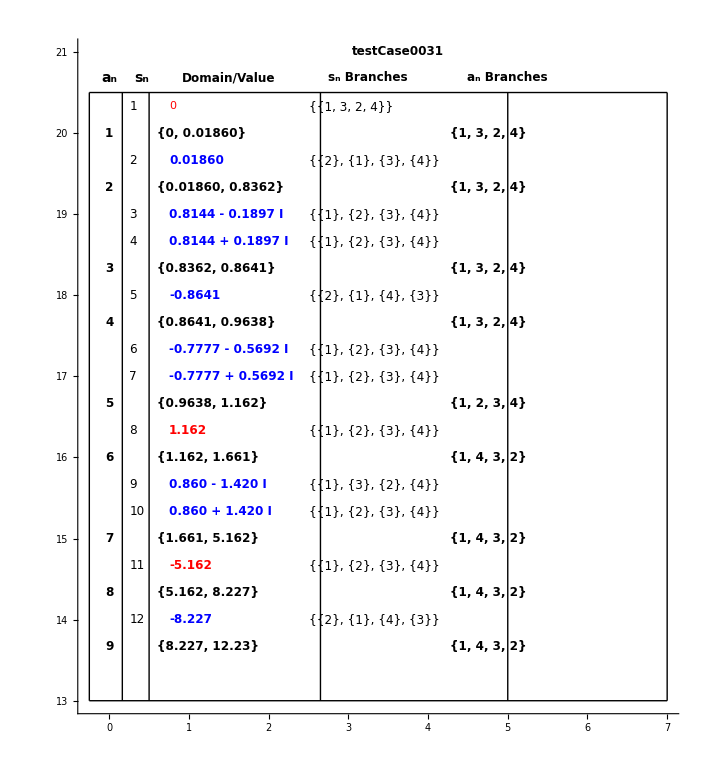

```mathematica
annularDataOffset=-0.25;
text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.4,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.5,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.25,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{5,20.68}];

annularContinuationDiagram=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{.6,0}],
Graphics@Translate[singularPointGraphics,{.75,0}],
Graphics@Translate[singularPointMonodromyGraphics,{2.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularDataOffset,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
(*
Graphics@Translate[arrowTable,{-0.25,0}],
Graphics@Translate[poleLinkGraphics,{0,0}],*)
Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]},Axes->True]
```

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
yLoc=poleLinkGraphicData[[i,3]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];
]
poleLinkGraphics[[1,2]]={5,49/3};
poleLinkGraphics[[2,2]]={5.5,49/3};
poleLinkGraphics[[3,2]]={6,49/3};
poleLinkGraphics[[4,2]]={6.5,49/3};

poleLinkGraphics[[5,2]]={5,44/3};
poleLinkGraphics[[6,2]]={5.5,44/3};
poleLinkGraphics[[7,2]]={6,44/3};
poleLinkGraphics[[8,2]]={6.5,44/3};
```

x1

1

contPos: {1,2,3,4,5,6,7,8}

currentContLink: {1,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 1

theCurrentPreBranch: {1,3,2,4}

currentContLink: {2,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 2

theCurrentPreBranch: {1,3,2,4}

currentContLink: {3,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 3

theCurrentPreBranch: {1,3,2,4}

currentContLink: {4,{{{1,3,2,4},{1,2,3,4}}}}

theCurrentAnnulus: 4

theCurrentPreBranch: {1,3,2,4}

currentContLink: {5,{{{1,2,3,4},{1,4,3,2}}}}

theCurrentAnnulus: 5

theCurrentPreBranch: {1,2,3,4}

dashed arrow

currentContLink: {6,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 6

theCurrentPreBranch: {1,4,3,2}

currentContLink: {7,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 7

theCurrentPreBranch: {1,4,3,2}

dashed arrow

currentContLink: {8,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 8

theCurrentPreBranch: {1,4,3,2}

16/3

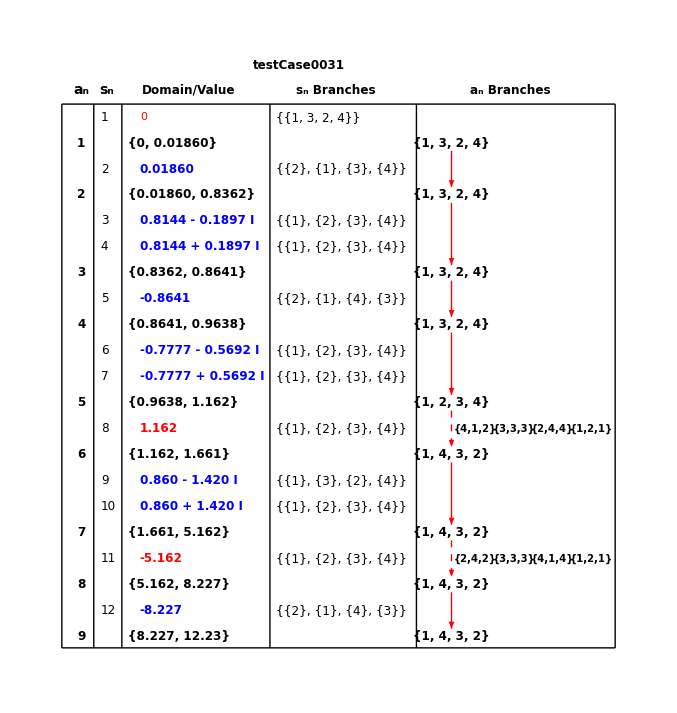

```mathematica
(*
 create a continuation diagram
*)
(*Print["test5"];*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
contLinks=continuationRecords[[All,{1,8}]];
currentContAIndex=2;

currentContLink=contLinks[[currentContAIndex]];


{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];

{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
currentBranchLink=1;
Print["x1"];
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
(*Print["x2"];*)
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
(*Print["temp"];*)
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];
(*Print["x3"];*)
dy=0.1;
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];

(*
 do arrows
*)
(*Print["test6"];*)
  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;

contRange=Intersection[contLinks[[All,1]],Range[annuliStart,annuliEnd-1]];
contPos=Position[contLinks[[All,1]],x_/;x==#]&/@ contRange//Flatten;
Print["contPos: ",contPos];



arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentContLink: ",currentContLink];
theCurrentAnnulus=currentContLink[[1]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arrow points
*)
(*Print["g1"];*)
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
(*Print["aa"];*)
prePos=Position[xLocationSave[[All,1]],x_/;x==preLocationNum][[1,1]];
preYVal=xLocationSave[[prePos,2]];
(*Print["bb"];*)

postPos=Position[xLocationSave[[All,1]],x_/;x==postLocationNum][[1,1]];
postYVal=xLocationSave[[postPos,2]];
(*Print["xx"];*)
preXVal=xLocationSave[[prePos,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postPos,3,currentPostBranchLoc]];
Print["theCurrentAnnulus: ",theCurrentAnnulus];
Print["theCurrentPreBranch: ",theCurrentPreBranch];
poleData=poleRecords[[All,{1,2}]];
If[MemberQ[poleData,{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print["dashed arrow"];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,contPos},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];


rightVerticalX=annularMonodromyOffSet+netMax+1/3
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{6.85,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,13.52},{6.85,13.52}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,13.52}}];

vLine2=Graphics@Line[{{0.16,20.5},{0.16,13.52}}];

vLine3=Graphics@Line[{{0.52,20.5},{0.52,13.52}}];

vLine4=Graphics@Line[{{2.42,20.5},{2.42,13.52}}];
vLine5=Graphics@Line[{{4.3,20.5},{4.3,13.52}}];
vLine6=Graphics@Line[{{6.85,20.5},{6.85,13.52}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.331,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.38,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.26,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{5.5,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)


annularDataOffset=-0.25;

annularContinuationDiagram=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{.6,0}],
Graphics@Translate[singularPointGraphics,{.75,0}],
Graphics@Translate[singularPointMonodromyGraphics,{2.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularDataOffset,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,

Graphics@Translate[arrowTable,{-0.25,0}],
Graphics@Translate[poleLinkGraphics,{0.05,0}],
Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Export the annular table with branch links to file (used by the Chapter 8 notebook)

```mathematica
(*
 export annular table with branch links to file for Chapter 8
*)
Export[annularTableWithBranchLinksFileName[$theTestCase],gFile];
```

### Section 8.6: Create Annular continuation diagram for testCase0001Inf

```mathematica
(*
 do the annulus numbers
*)
annulusIndexOffset=0;
annuliOffset=0.5;
singularOffset=0.5;
singularIndexOffset=1/5;
singularMonodromyOffset=2.3;


agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
annuliStart=1;
annuliEnd=Length@theAnnuli;



For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

-4

{{1,20},{2,58/3},{3,56/3},{4,18},{5,17},{6,49/3},{7,46/3},{8,44/3},{9,41/3},{10,38/3},{11,35/3},{12,32/3},{13,29/3},{14,26/3},{15,23/3},{16,20/3},{17,17/3},{18,14/3},{19,11/3},{20,8/3},{21,5/3},{22,2/3},{23,-1/3},{24,-4/3},{25,-7/3},{26,-10/3}}

0.

-4

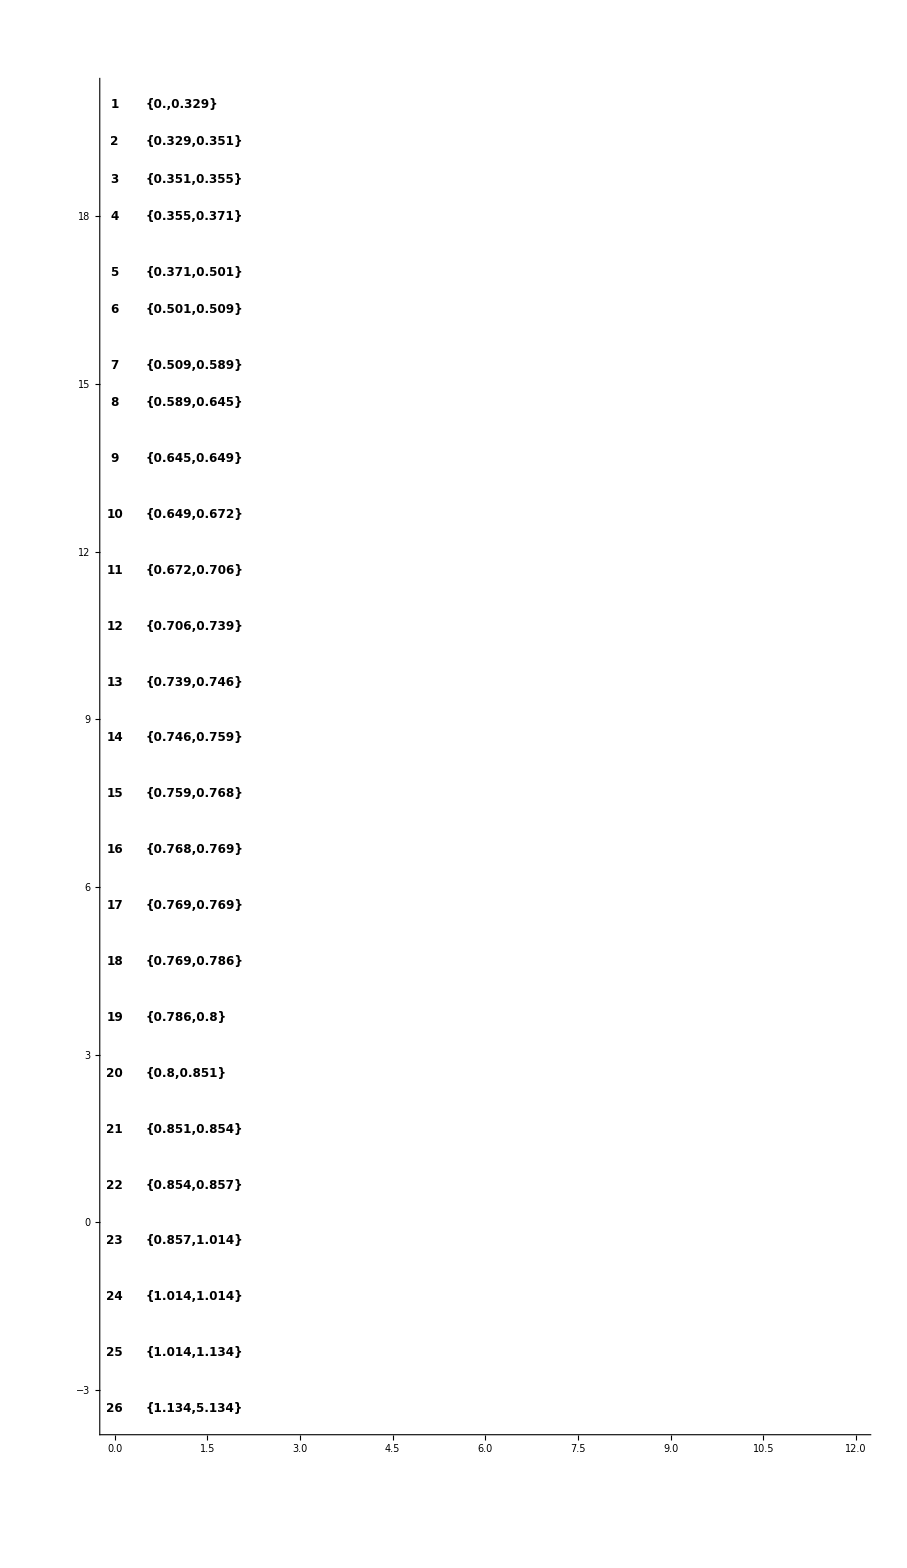

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["k: ",k," domain: ",SetAccuracy[annulusTable[[aIndex,3]],3]];*)
AppendTo[annuliGraphics,Inset[Style[SetAccuracy[annulusTable[[aIndex,3]],4],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
(*AppendTo[annuliGraphics,Inset[Style[SetAccuracy[annulusTable[[-1,3]],4],12,Black,Bold],{0,yOffSet},Left]];*)
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

Annulus 7 has a pole link

annulus monodromy: {{1,3,2},{4},{5}}

pole links: {{9,3,5,3}}

Processing pole link {9,3,5,3}

Annulus branch sheet: 3

annulusBranchIndex: 1

Singular point: 9

Sing pole links: {3,5,3}

y-offset for this sing: 15

Pole: -0.5885

Annulus 9 has a pole link

annulus monodromy: {{1,3,2},{4},{5}}

pole links: {{12,4,3,4},{13,5,1,5}}

Processing pole link {12,4,3,4}

Annulus branch sheet: 4

annulusBranchIndex: 2

Singular point: 12

Sing pole links: {4,3,4}

y-offset for this sing: 40/3

Processing pole link {13,5,1,5}

Annulus branch sheet: 5

annulusBranchIndex: 3

Singular point: 13

Sing pole links: {5,1,5}

y-offset for this sing: 13

Pole: 0.4428-0.4742 ⅈ

Pole: 0.4428+0.4742 ⅈ

Annulus 22 has a pole link

annulus monodromy: {{1,2,3},{4},{5}}

pole links: {{38,2,5,2},{39,2,1,2}}

Processing pole link {38,2,5,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 38

Sing pole links: {2,5,2}

y-offset for this sing: 1/3

Processing pole link {39,2,1,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 39

Sing pole links: {2,1,2}

y-offset for this sing: 0

Pole: -0.1485-0.8437 ⅈ

Pole: -0.1485+0.8437 ⅈ

poleLinkGraphicsData: {{7,9,15,1,{3,5,3}},{9,12,40/3,2,{4,3,4}},{9,13,13,3,{5,1,5}},{22,38,1/3,1,{2,5,2}},{22,39,0,1,{2,1,2}}}

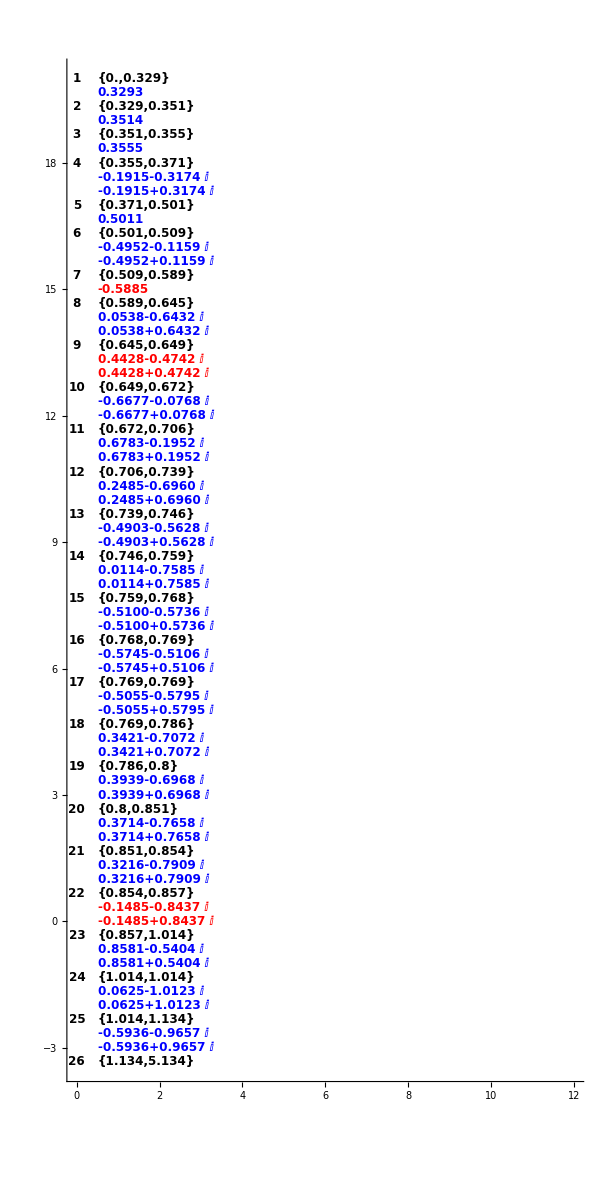

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=annuliStart,k<=annuliEnd-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

sIndex: {2}

sIndex: {4}

sIndex: {6}

sIndex: {8,9}

sIndex: {11}

sIndex: {13,14}

sIndex: {16}

sIndex: {18,19}

sIndex: {21,22}

sIndex: {24,25}

sIndex: {27,28}

sIndex: {30,31}

sIndex: {33,34}

sIndex: {36,37}

sIndex: {39,40}

sIndex: {42,43}

sIndex: {45,46}

sIndex: {48,49}

sIndex: {51,52}

sIndex: {54,55}

sIndex: {57,58}

sIndex: {60,61}

sIndex: {63,64}

sIndex: {66,67}

sIndex: {69,70}

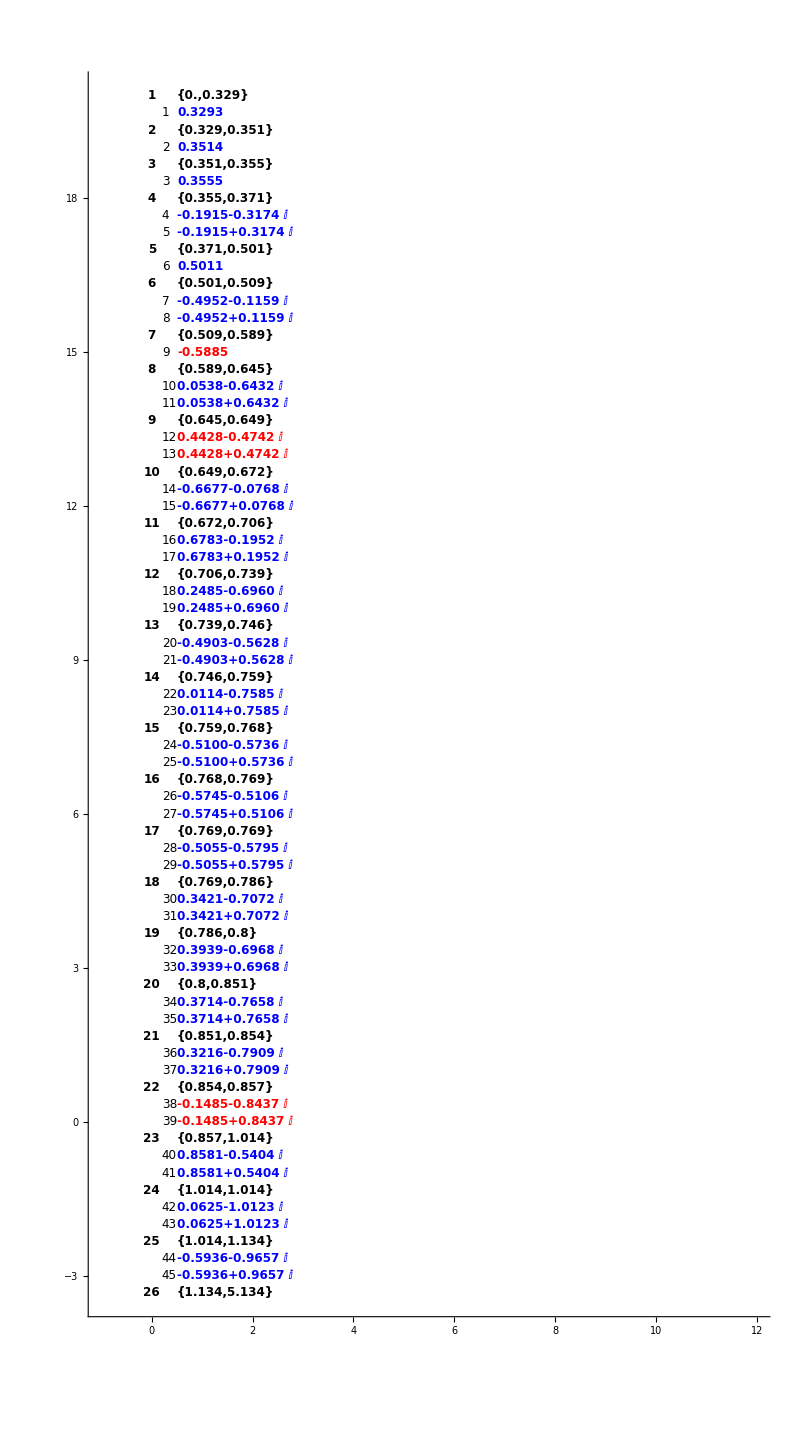

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}]},PlotRange->{{-1,12},All},Axes->True]
```

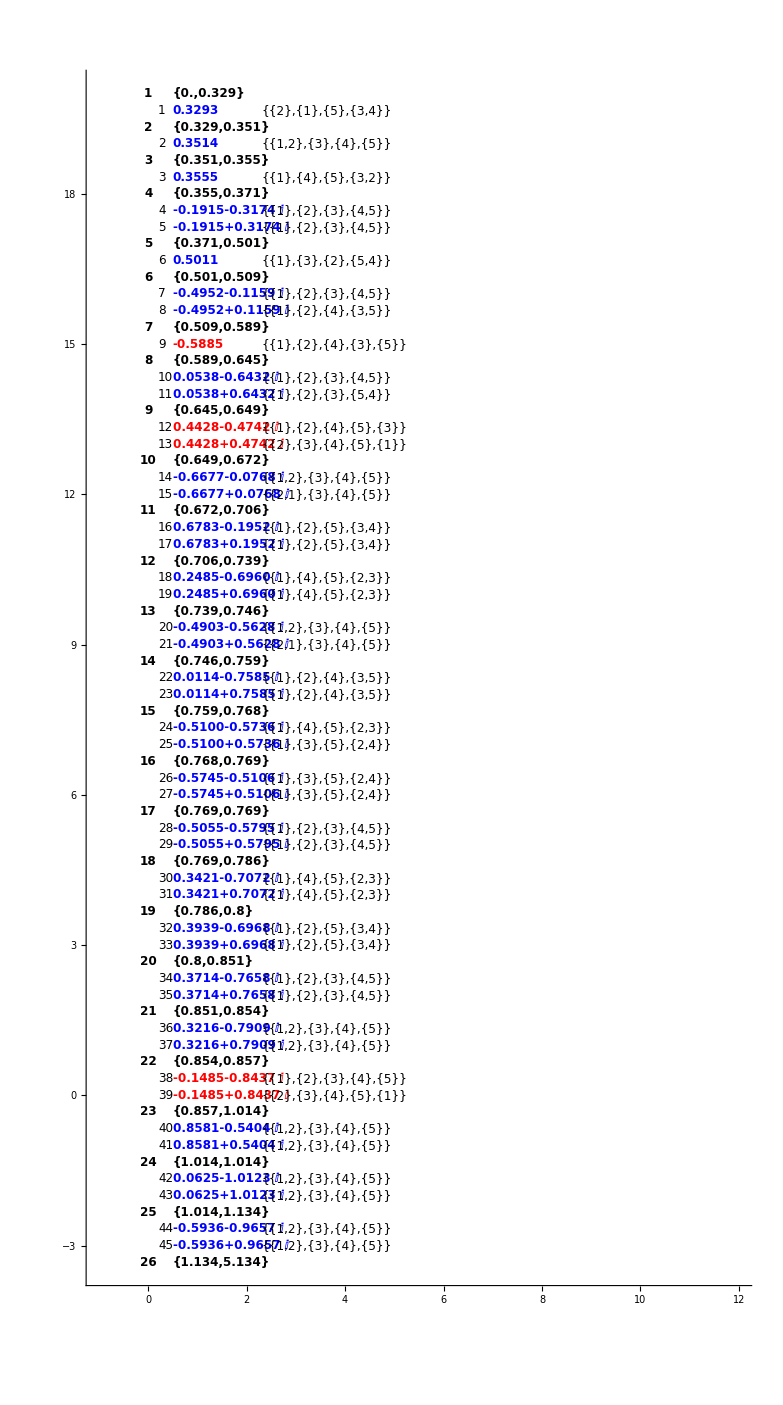

```mathematica
(*
 do singular monodromies
*)
If[FileExistsQ[singularMonodromyFileName[$theTestCase]],
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
 (*MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromiesR,$minRadiusArray//N}]//MatrixForm
*)
 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
(*Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];*)
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Print[Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{2.3,0}]},PlotRange->{{-1,12},All},Axes->True]];
,
Print[Style[singularMonodromyFileName[$theTestCase]<>" not found during import.",Red]];
];
```

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{3,4},{1},{2},{5}}

x-locations: {2,4,6,8}

Monodromy: {{1,2},{3,4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,4,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,5,2},{4}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4,5,2}}

x-locations: {5}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{2,5},{3,4},{1}}

x-locations: {5/2,5,15/2}

Monodromy: {{2,4},{3,5},{1}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,3},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,3},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

)

```mathematica
continuationList
```

{{1,{4},{4}},{1,{5},{5}},{2,{4},{4}},{2,{5},{5}},{3,{4},{4}},{3,{5},{5}},{4,{1,2,3},{1,2,3}},{4,{4},{4}},{4,{5},{5}},{5,{4},{4}},{5,{5},{5}},{6,{1,3,2},{1,3,2}},{14,{1},{1}},{15,{1},{1}},{16,{4},{5}},{16,{5},{4}},{17,{1,3,2},{1,3,2}},{17,{4},{4}},{17,{5},{5}},{18,{1,3,2},{1,3,2}},{19,{1,3,2},{1,3,2}},{19,{4},{4}},{19,{5},{5}},{23,{5},{5}},{24,{3,4},{3,4}},{24,{5},{5}},{25,{1},{1}},{25,{2},{2}},{25,{5},{5}}}

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(7 | 9 | 15 | 1 | {3,5,3}
9 | 12 | 40/3 | 2 | {4,3,4}
9 | 13 | 13 | 3 | {5,1,5}
22 | 38 | 1/3 | 1 | {2,5,2}
22 | 39 | 0 | 1 | {2,1,2})

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 58/3 | {2,4,6,8}
3 | 56/3 | {5/2,5,15/2}
4 | 18 | {10/3,20/3}
5 | 17 | {10/3,20/3}
6 | 49/3 | {5}
7 | 46/3 | {5/2,5,15/2}
8 | 44/3 | {5/2,5,15/2}
9 | 41/3 | {5/2,5,15/2}
10 | 38/3 | {5/2,5,15/2}
11 | 35/3 | {5/3,10/3,5,20/3,25/3}
12 | 32/3 | {5/2,5,15/2}
13 | 29/3 | {5/2,5,15/2}
14 | 26/3 | {5}
15 | 23/3 | {5}
16 | 20/3 | {5}
17 | 17/3 | {5}
18 | 14/3 | {5}
19 | 11/3 | {5}
20 | 8/3 | {5/2,5,15/2}
21 | 5/3 | {5/2,5,15/2}
22 | 2/3 | {5/2,5,15/2}
23 | -1/3 | {5/2,5,15/2}
24 | -4/3 | {5/2,5,15/2}
25 | -7/3 | {5/2,5,15/2}
26 | -10/3 | {5/3,10/3,5,20/3,25/3})

currentBranchIndex: 1

currentAnnulus: 7

current sing index: 9

xLocationPos: 7

xLocationData: {7,46/3,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 15

pole link string: {3,5,3}

currentBranchIndex: 2

currentAnnulus: 9

current sing index: 12

xLocationPos: 9

xLocationData: {9,41/3,{5/2,5,15/2}}

xLocation for this link: 5

yLocation for this link: 40/3

pole link string: {4,3,4}

currentBranchIndex: 3

currentAnnulus: 9

current sing index: 13

xLocationPos: 9

xLocationData: {9,41/3,{5/2,5,15/2}}

xLocation for this link: 15/2

yLocation for this link: 13

pole link string: {5,1,5}

currentBranchIndex: 1

currentAnnulus: 22

current sing index: 38

xLocationPos: 22

xLocationData: {22,2/3,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 1/3

pole link string: {2,5,2}

currentBranchIndex: 1

currentAnnulus: 22

current sing index: 39

xLocationPos: 22

xLocationData: {22,2/3,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 0

pole link string: {2,1,2}

```mathematica
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]]
```

(1 | {{{1},{1}},{{2},{2}},{{5},{5}}}
2 | {{{3,4},{3,4}},{{5},{5}}}
3 | {{{5},{5}}}
7 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
8 | {{{1,3,2},{1,3,2}}}
9 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
10 | {{{4},{5}},{{5},{4}}}
11 | {{{1},{1}}}
12 | {{{1},{1}}}
20 | {{{1,3,2},{1,3,2}}}
21 | {{{4},{4}},{{5},{5}}}
22 | {{{1,2,3},{1,2,3}},{{4},{4}},{{5},{5}}}
23 | {{{4},{4}},{{5},{5}}}
24 | {{{4},{4}},{{5},{5}}}
25 | {{{4},{4}},{{5},{5}}})

{{1,{{{1},{1}},{{2},{2}},{{5},{5}}}},{2,{{{3,4},{3,4}},{{5},{5}}}},{3,{{{5},{5}}}},{7,{{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}},{8,{{{1,3,2},{1,3,2}}}},{9,{{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}},{10,{{{4},{5}},{{5},{4}}}},{11,{{{1},{1}}}},{12,{{{1},{1}}}},{20,{{{1,3,2},{1,3,2}}}},{21,{{{4},{4}},{{5},{5}}}},{22,{{{1,2,3},{1,2,3}},{{4},{4}},{{5},{5}}}},{23,{{{4},{4}},{{5},{5}}}},{24,{{{4},{4}},{{5},{5}}}},{25,{{{4},{4}},{{5},{5}}}}}

(1 | {{{1},{1}},{{2},{2}},{{5},{5}}}
2 | {{{3,4},{3,4}},{{5},{5}}}
3 | {{{5},{5}}}
7 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
8 | {{{1,3,2},{1,3,2}}}
9 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
10 | {{{4},{5}},{{5},{4}}}
11 | {{{1},{1}}}
12 | {{{1},{1}}}
20 | {{{1,3,2},{1,3,2}}}
21 | {{{4},{4}},{{5},{5}}}
22 | {{{1,2,3},{1,2,3}},{{4},{4}},{{5},{5}}}
23 | {{{4},{4}},{{5},{5}}}
24 | {{{4},{4}},{{5},{5}}}
25 | {{{4},{4}},{{5},{5}}})

{1,{{{1},{1}},{{2},{2}},{{5},{5}}}}

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 58/3 | {2,4,6,8}
3 | 56/3 | {5/2,5,15/2}
4 | 18 | {10/3,20/3}
5 | 17 | {10/3,20/3}
6 | 49/3 | {5}
7 | 46/3 | {5/2,5,15/2}
8 | 44/3 | {5/2,5,15/2}
9 | 41/3 | {5/2,5,15/2}
10 | 38/3 | {5/2,5,15/2}
11 | 35/3 | {5/3,10/3,5,20/3,25/3}
12 | 32/3 | {5/2,5,15/2}
13 | 29/3 | {5/2,5,15/2}
14 | 26/3 | {5}
15 | 23/3 | {5}
16 | 20/3 | {5}
17 | 17/3 | {5}
18 | 14/3 | {5}
19 | 11/3 | {5}
20 | 8/3 | {5/2,5,15/2}
21 | 5/3 | {5/2,5,15/2}
22 | 2/3 | {5/2,5,15/2}
23 | -1/3 | {5/2,5,15/2}
24 | -4/3 | {5/2,5,15/2}
25 | -7/3 | {5/2,5,15/2}
26 | -10/3 | {5/3,10/3,5,20/3,25/3})

{1,{2}}

preMonodromy: {{1},{2},{3},{4},{5}}

{3,{4}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

1

2

1

2

20

58/3

5/3

4

0.1

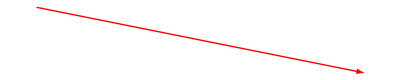

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}]
```

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
7 | {1,3,2} | 3 | 9 | L_-1 | {5} | 5 | True | {1,3,2} | 3 | True
9 | {4} | 4 | 12 | L_-1 | {3} | 3 | True | {4} | 4 | True
9 | {5} | 5 | 13 | L_-1 | {1} | 1 | True | {5} | 5 | True
22 | {1,2,3} | 2 | 38 | L_-1 | {5} | 5 | True | {1,2,3} | 2 | True
22 | {1,2,3} | 2 | 39 | L_-1 | {1} | 1 | True | {1,2,3} | 2 | True

```mathematica
contLinks//MatrixForm
```

(1 | {{{1},{1}},{{2},{2}},{{5},{5}}}
2 | {{{3,4},{3,4}},{{5},{5}}}
3 | {{{5},{5}}}
7 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
8 | {{{1,3,2},{1,3,2}}}
9 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
10 | {{{4},{5}},{{5},{4}}}
11 | {{{1},{1}}}
12 | {{{1},{1}}}
20 | {{{1,3,2},{1,3,2}}}
21 | {{{4},{4}},{{5},{5}}}
22 | {{{1,2,3},{1,2,3}},{{4},{4}},{{5},{5}}}
23 | {{{4},{4}},{{5},{5}}}
24 | {{{4},{4}},{{5},{5}}}
25 | {{{4},{4}},{{5},{5}}})

```mathematica
(*
 do arrows
*)


(*  contLinks=continuationRecords[[annuliStart;;annuliEnd,{1,8}]];*)
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{1,2},{3,4},{5}}

currentPreBranch: {3,4}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{1,2},{3,4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{1,3,4,2},{5}}

postMonodromy: {{1,3,4,2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

Creating dashed arrow

current pre branch: {1,3,2}

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

Creating dashed arrow

current pre branch: {4}

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

Creating dashed arrow

current pre branch: {5}

currentAnnulus: 10

currentContLink: 10

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 10

currentContLink: 10

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{2,5},{3,4},{1}}

postMonodromy: {{2,5},{3,4},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 12

currentContLink: 12

preMonodromy: {{2,5},{3,4},{1}}

postMonodromy: {{2,4},{3,5},{1}}

postMonodromy: {{2,4},{3,5},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 20

currentContLink: 20

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 21

currentContLink: 21

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 21

currentContLink: 21

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 22

currentContLink: 22

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {1,2,3}

testa

testb

Creating dashed arrow

current pre branch: {1,2,3}

currentAnnulus: 22

currentContLink: 22

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 22

currentContLink: 22

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 23

currentContLink: 23

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 23

currentContLink: 23

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {5}

testa

testb

2.75

3.3

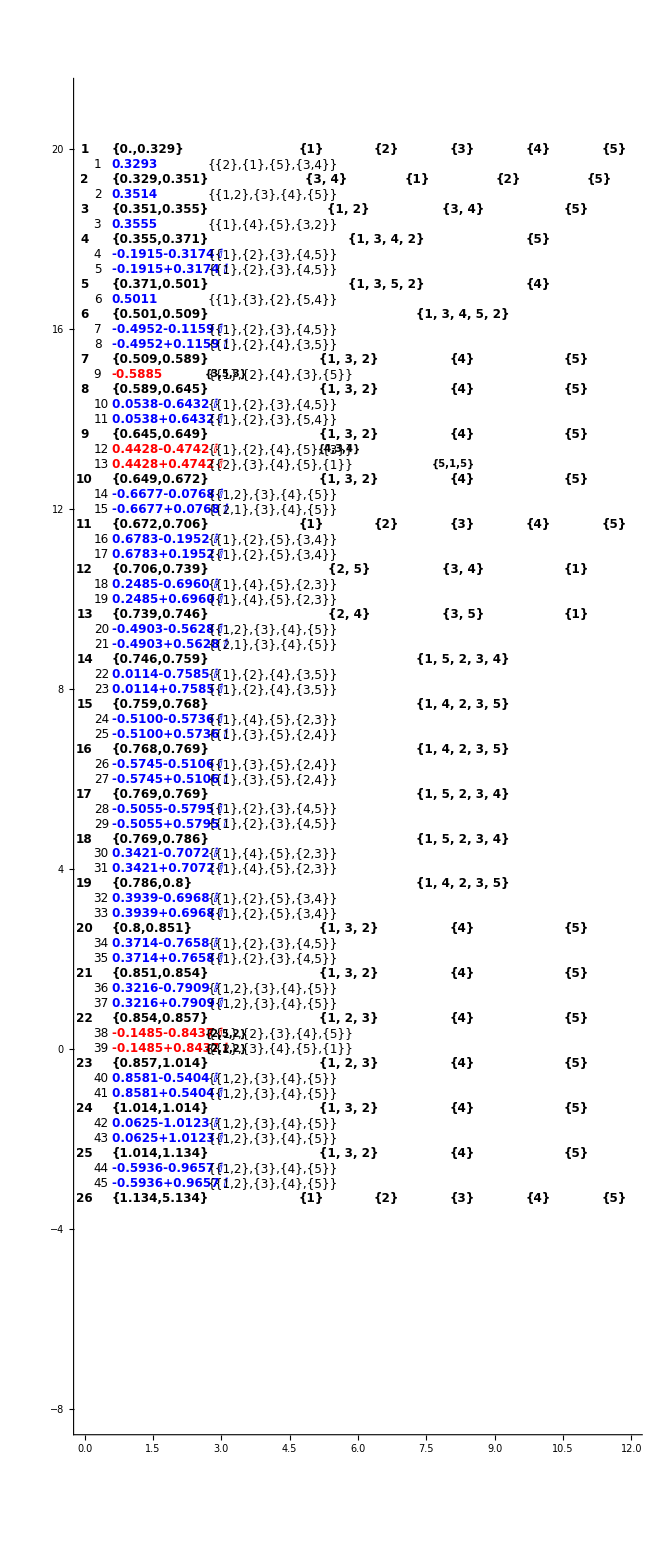

```mathematica
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],Graphics@Translate[annuliMonodromyGraphics,{3.3,0}],
Graphics@Translate[poleLinkGraphics,{annuliOffset,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
```

```mathematica
annulusIndexOffset=0;
annuliOffset=0.6;
singularOffset=0.6;
singularIndexOffset=1/5;
singularMonodromyOffset=2.7;
```

12.0833

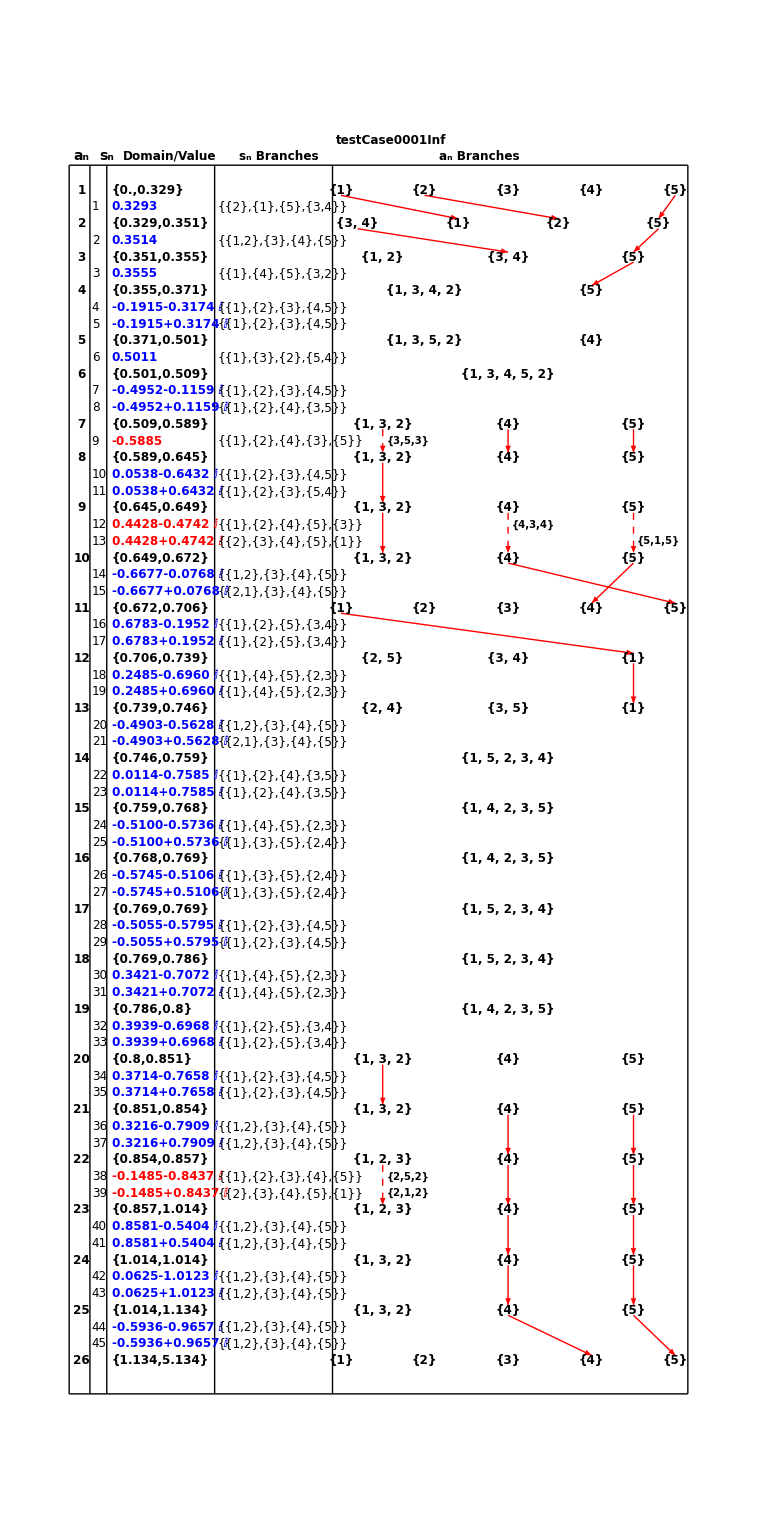

```mathematica
annularMonodromyOffSet=3.5;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.164,20.5},{0.164,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.5,20.5},{0.5,yOffsetFinal}}];
vLine4=Graphics@Line[{{2.65,20.5},{2.65,yOffsetFinal}}];
vLine5=Graphics@Line[{{5,20.5},{5,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{annuliOffset,0}],
Graphics@Translate[singularPointGraphics,{singularOffset,0}],
Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{3.5,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

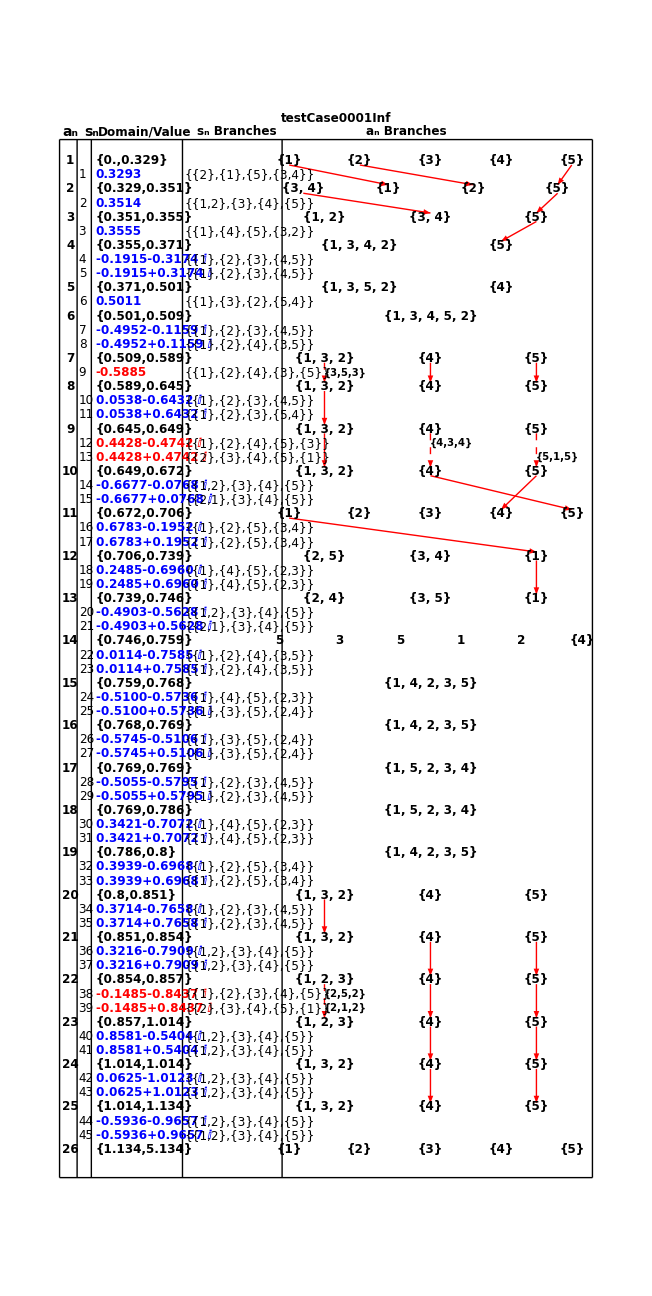

```mathematica
Show[gFile,Background->White]
```

### Section 8.7: Create Annular continuation diagram for testCase0002

This graphics is better done in sections  determined by the annuliStart and annuliEnd variables below

```mathematica
(*
 do the annulus numbers
*)
annulusIndexOffset=0;
annuliOffset=0.5;
singularOffset=0.5;
singularIndexOffset=1/5;
singularMonodromyOffset=2.3;


agIndex=1/2;
sgIndex=1/2;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
annuliStart=1;
annuliEnd=10;



For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

11/2

{{1,20},{2,37/2},{3,17},{4,16},{5,29/2},{6,13},{7,23/2},{8,10},{9,17/2},{10,7}}

```mathematica
SetPrecision[annulusTable[[2,3]],4]
```

{0,0.1668}

11/2

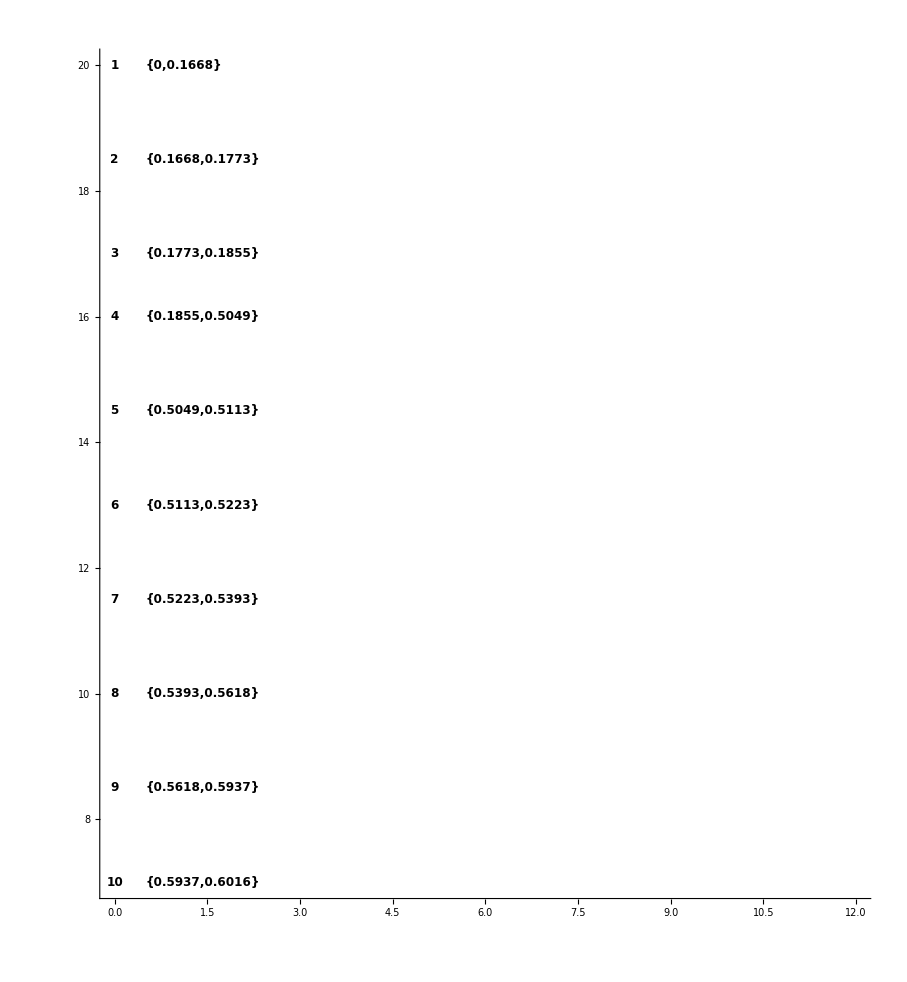

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["k: ",k," domain: ",SetAccuracy[annulusTable[[aIndex,3]],3]];*)
AppendTo[annuliGraphics,Inset[Style[SetPrecision[annulusTable[[aIndex,3]],4],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
(*AppendTo[annuliGraphics,Inset[Style[SetAccuracy[annulusTable[[-1,3]],4],12,Black,Bold],{0,yOffSet},Left]];*)
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

poleLinkGraphicsData: {}

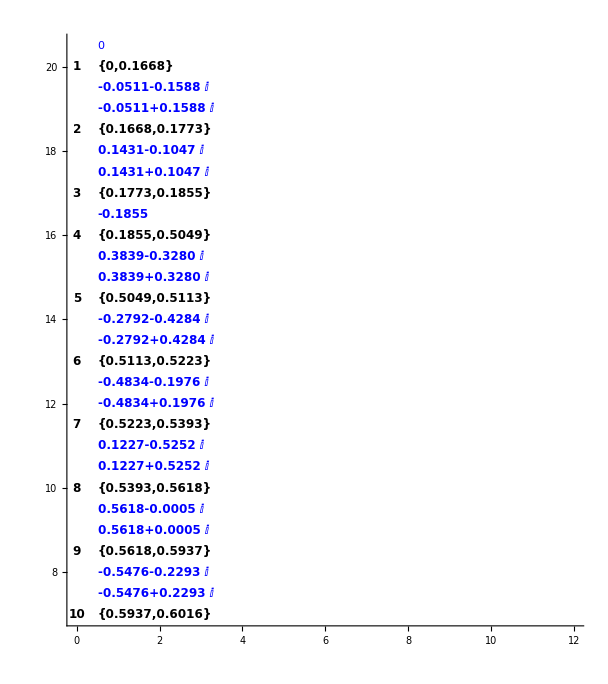

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=annuliStart,k<=annuliEnd-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

sIndex: {3,4}

sIndex: {6,7}

sIndex: {9}

sIndex: {11,12}

sIndex: {14,15}

sIndex: {17,18}

sIndex: {20,21}

sIndex: {23,24}

sIndex: {26,27}

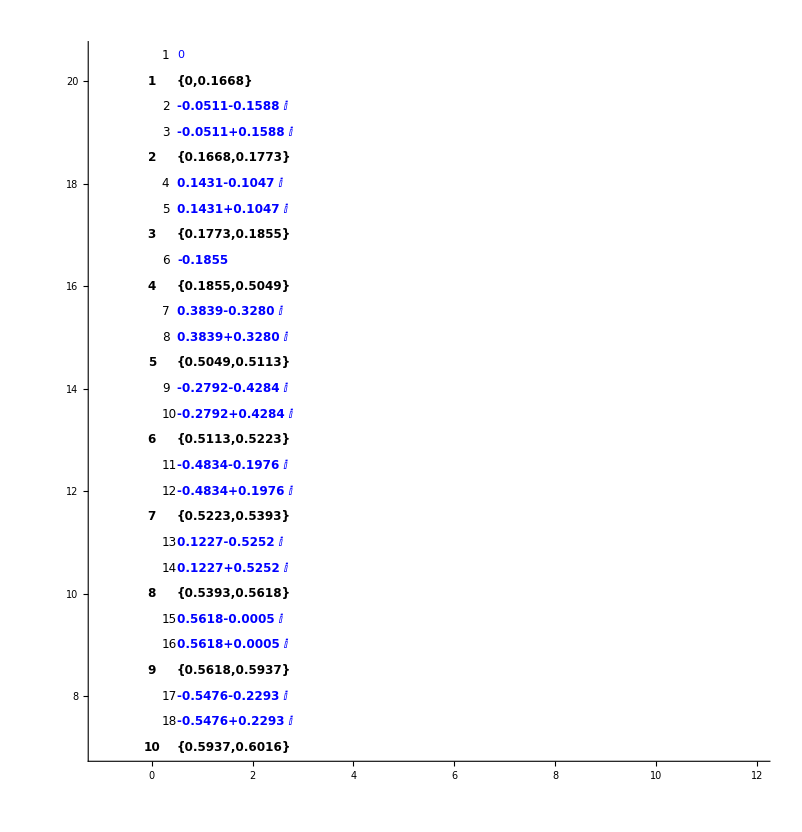

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}]},PlotRange->{{-1,12},All},Axes->True]
```

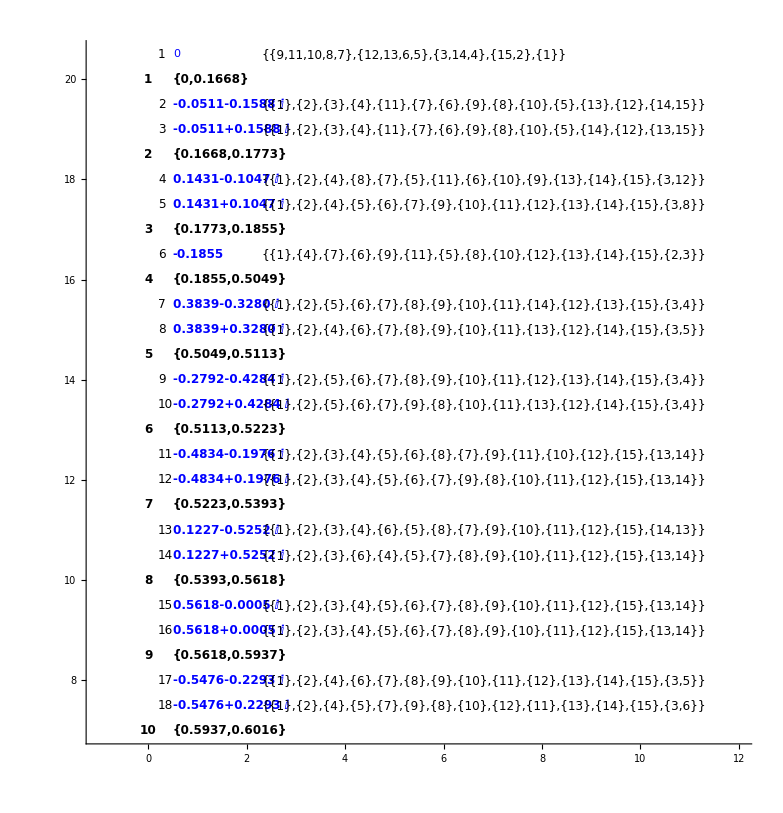

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
(*MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromiesR,$minRadiusArray//N}]//MatrixForm
*)
 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
(*Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];*)
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{2.3,0}]},PlotRange->{{-1,12},All},Axes->True]
```

```mathematica
{aIndex,sIndex}=getSingTableIndexes[annulusTable,7];
Show[Graphics[{LightGreen,Disk[{locations[[1]],yOffSet},{1.72,0.3}],Inset[Style[ToString[annulusTable[[1aIndex,6,j]]],12,Black,Bold],{locations[[1]],yOffSet},Center]}],Axes->True,PlotRange->7]
```

Part::partw: Part 5 of {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}} does not exist.

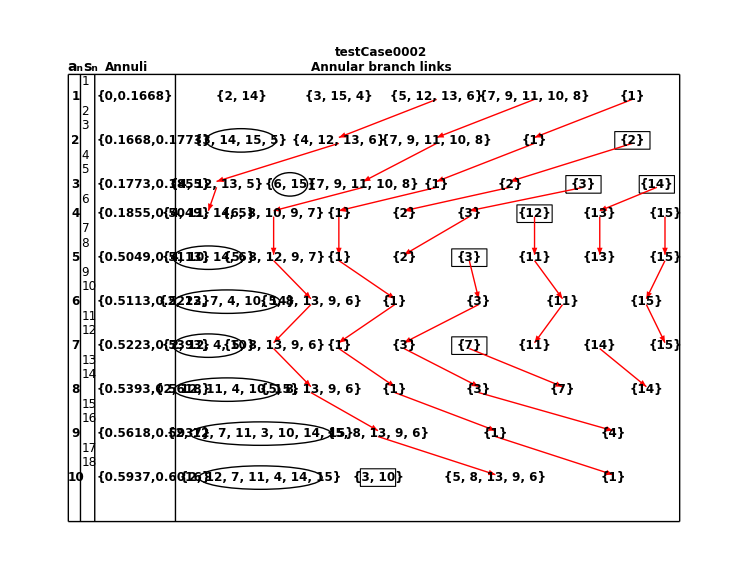

```mathematica
gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{annuliOffset,0}],
(*Graphics@Translate[singularPointGraphics,{singularOffset,0}],*)
(*Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],*)Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text5,vLine1,vLine2,vLine3,vLine4,(*vLine5,*)vLine6,
Graphics@Translate[arrowTable,{annularMonodromyOffSet,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21.5}]}]
```

```mathematica
MemberQ[shortCutCodes,{2,1,_,_}]
```

True

```mathematica
(*
 do annular monodromies with short cut codes (0 for ellipse, 1 for square)
*)
shortCutCodes={{2,1,0,4},{2,5,1,0},
{3,2,0,2},{3,6,1,0},{3,7,1,0},
{4,6,1,0},
{5,1,0,4},{5,5,1,0},
{6,1,0,6},
{7,1,0,4},{7,5,1,0},{7,5,7,0},
{8,1,0,6},
{9,1,0,8},
{10,1,0,7},{10,2,1,0}};

ellipseFactor=0.3;


xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=20;
netMax=0;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];

For[j=1,j<=numBranches,j++,
If[MemberQ[shortCutCodes,{k,j,_,_}],
pos=Position[shortCutCodes,{a_,b_,_,_}/;a==k && b==j][[1,1]];
Print["pos: ",pos];
shortCut=shortCutCodes[[pos,3]];
If[shortCut==0,
eFactor=shortCutCodes[[pos,4]];
Print["ellipse val: ",eFactor ellipseFactor];
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],Circle[{locations[[j]],yOffSet},{eFactor ellipseFactor,0.4}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]}];
,
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],EdgeForm[Black],Rectangle[{locations[[j]]-0.6,yOffSet-0.3},{locations[[j]]+0.6,yOffSet+0.3}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]}];
];
,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
```

Monodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

x-locations: {10/3,20/3,10,40/3,50/3}

Monodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

x-locations: {10/3,20/3,10,40/3,50/3}

pos: 1

ellipse val: 1.2

pos: 2

Monodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

x-locations: {5/2,5,15/2,10,25/2,15,35/2}

pos: 3

ellipse val: 0.6

pos: 4

pos: 5

Monodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

pos: 6

Monodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

pos: 7

ellipse val: 1.2

pos: 8

Monodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

x-locations: {20/7,40/7,60/7,80/7,100/7,120/7}

pos: 9

ellipse val: 1.8

Monodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

pos: 10

ellipse val: 1.2

pos: 11

Monodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

x-locations: {20/7,40/7,60/7,80/7,100/7,120/7}

pos: 13

ellipse val: 1.8

Monodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

x-locations: {4,8,12,16}

pos: 14

ellipse val: 2.4

Monodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

x-locations: {4,8,12,16}

pos: 15

ellipse val: 2.1

pos: 16

```mathematica
(*
 0 for ellipse, 1 for square
*)
currentA=3;
currentB=6;

shortCutCodes={{2,1,0},{2,5,1},{3,1,0},{3,2,1},{3,6,1},{3,7,1}}
If[MemberQ[shortCutCodes,{currentA,currentB,_}],
pos=Position[shortCutCodes,{a_,b_,_}/;a==currentA && b==currentB][[1,1]];
Print["pos: ",pos];
shortCut=shortCutCodes[[pos,3]];
Print["shortCut: ",shortCut];
If[shortCut==0,
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],Circle[{locations[[j]],yOffSet},{1.1,0.4}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[1]],yOffSet},Center]}];
,
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],EdgeForm[Black],Rectangle[{locations[[j]]-0.4,yOffSet-0.4},{locations[[j]]+0.4,yOffSet+0.4}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]}];
];
,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
```

{{2,1,0},{2,5,1},{3,1,0},{3,2,1},{3,6,1},{3,7,1}}

pos: 5

shortCut: 1

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=20;
netMax=0;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];

For[j=1,j<=numBranches,j++,
If[k==7 && j==1,
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],Circle[{locations[[1]],yOffSet},{1.1,0.4}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[1]],yOffSet},Center]}];
,
If[k==7 && (j==5 || j==7),
AppendTo[annuliMonodromyGraphics,{Black,FaceForm[],EdgeForm[Black],Rectangle[{locations[[j]]-0.4,yOffSet-0.4},{locations[[j]]+0.4,yOffSet+0.4}],Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]}];
,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

x-locations: {10/3,20/3,10,40/3,50/3}

Monodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

x-locations: {10/3,20/3,10,40/3,50/3}

Monodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

x-locations: {5/2,5,15/2,10,25/2,15,35/2}

Monodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

Monodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

Monodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

x-locations: {20/7,40/7,60/7,80/7,100/7,120/7}

Monodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

x-locations: {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}

Monodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

x-locations: {20/7,40/7,60/7,80/7,100/7,120/7}

Monodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

x-locations: {4,8,12,16}

Monodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

x-locations: {4,8,12,16}

)

```mathematica
continuationList
```

{{1,{4},{4}},{1,{5},{5}},{2,{4},{4}},{2,{5},{5}},{3,{4},{4}},{3,{5},{5}},{4,{1,2,3},{1,2,3}},{4,{4},{4}},{4,{5},{5}},{5,{4},{4}},{5,{5},{5}},{6,{1,3,2},{1,3,2}},{14,{1},{1}},{15,{1},{1}},{16,{4},{5}},{16,{5},{4}},{17,{1,3,2},{1,3,2}},{17,{4},{4}},{17,{5},{5}},{18,{1,3,2},{1,3,2}},{19,{1,3,2},{1,3,2}},{19,{4},{4}},{19,{5},{5}},{23,{5},{5}},{24,{3,4},{3,4}},{24,{5},{5}},{25,{1},{1}},{25,{2},{2}},{25,{5},{5}}}

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

{}

(1 | 20 | {10/3,20/3,10,40/3,50/3}
2 | 37/2 | {10/3,20/3,10,40/3,50/3}
3 | 17 | {5/2,5,15/2,10,25/2,15,35/2}
4 | 16 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
5 | 29/2 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
6 | 13 | {20/7,40/7,60/7,80/7,100/7,120/7}
7 | 23/2 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
8 | 10 | {20/7,40/7,60/7,80/7,100/7,120/7}
9 | 17/2 | {4,8,12,16}
10 | 7 | {4,8,12,16})

```mathematica
contLinks
```

{{4,{{{1,3},{1,3}},{{2},{2}}}}}

(1 | {{{5,12,13,6},{4,12,13,6}},{{7,9,11,10,8},{7,9,11,10,8}},{{1},{1}}}
2 | {{{4,12,13,6},{4,12,13,5}},{{7,9,11,10,8},{7,9,11,10,8}},{{1},{1}},{{2},{2}}}
3 | {{{4,12,13,5},{4,11,14,5}},{{7,9,11,10,8},{6,8,10,9,7}},{{1},{1}},{{2},{2}},{{3},{3}},{{14},{13}}}
4 | {{{6,8,10,9,7},{5,8,12,9,7}},{{1},{1}},{{3},{2}},{{12},{11}},{{13},{13}},{{15},{15}}}
5 | {{{5,8,12,9,7},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{11},{11}},{{15},{15}}}
6 | {{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{11},{11}},{{15},{15}}}
7 | {{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{7},{7}},{{14},{14}}}
8 | {{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{4}}}
9 | {{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}}}
10 | {{{3,10},{3,10}},{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}}})

{1,{{{5,12,13,6},{4,12,13,6}},{{7,9,11,10,8},{7,9,11,10,8}},{{1},{1}}}}

(1 | 20 | {10/3,20/3,10,40/3,50/3}
2 | 37/2 | {10/3,20/3,10,40/3,50/3}
3 | 17 | {5/2,5,15/2,10,25/2,15,35/2}
4 | 16 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
5 | 29/2 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
6 | 13 | {20/7,40/7,60/7,80/7,100/7,120/7}
7 | 23/2 | {20/9,40/9,20/3,80/9,100/9,40/3,140/9,160/9}
8 | 10 | {20/7,40/7,60/7,80/7,100/7,120/7}
9 | 17/2 | {4,8,12,16}
10 | 7 | {4,8,12,16})

{2,{3,4}}

preMonodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

{5,{6,7}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

3

2

1

2

20

37/2

10

20/3

0.1

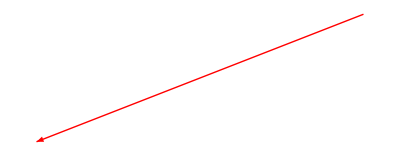

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}]
```

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag

```mathematica
contLinks
```

{{5,{{{5,8,12,9,7},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{11},{11}},{{15},{15}}}},{6,{{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{11},{11}},{{15},{15}}}},{7,{{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{3}},{{7},{7}},{{14},{14}}}},{8,{{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}},{{3},{4}}}},{9,{{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}}}},{10,{{{3,10},{3,10}},{{5,8,13,9,6},{5,8,13,9,6}},{{1},{1}}}}}

```mathematica
(*
 do arrows
*)


  contLinks=continuationRecords[[annuliStart;;annuliEnd,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks-1},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

currentPreBranch: {5,12,13,6}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

currentPreBranch: {7,9,11,10,8}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{2,14},{3,15,4},{5,12,13,6},{7,9,11,10,8},{1}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

currentPreBranch: {4,12,13,6}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

currentPreBranch: {7,9,11,10,8}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{3,14,15,5},{4,12,13,6},{7,9,11,10,8},{1},{2}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {4,12,13,5}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {7,9,11,10,8}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{4,12,13,5},{6,15},{7,9,11,10,8},{1},{2},{3},{14}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

currentPreBranch: {14}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {6,8,10,9,7}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {12}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {13}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{4,11,14,5},{6,8,10,9,7},{1},{2},{3},{12},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

currentPreBranch: {15}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

currentPreBranch: {5,8,12,9,7}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

currentPreBranch: {11}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{4,10,14,6},{5,8,12,9,7},{1},{2},{3},{11},{13},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

currentPreBranch: {15}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

currentPreBranch: {5,8,13,9,6}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

currentPreBranch: {11}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{2,12,7,4,10,14},{5,8,13,9,6},{1},{3},{11},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

currentPreBranch: {15}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

currentPreBranch: {5,8,13,9,6}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

currentPreBranch: {7}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{2,12,4,10},{5,8,13,9,6},{1},{3},{7},{11},{14},{15}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

currentPreBranch: {14}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

currentPreBranch: {5,8,13,9,6}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{2,12,11,4,10,15},{5,8,13,9,6},{1},{3},{7},{14}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

postMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

postMonodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

postMonodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

currentPreBranch: {5,8,13,9,6}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{2,12,7,11,3,10,14,15},{5,8,13,9,6},{1},{4}}

postMonodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

postMonodromy: {{2,12,7,11,4,14,15},{3,10},{5,8,13,9,6},{1}}

currentPreBranch: {1}

testa

testb

2.75

3.3

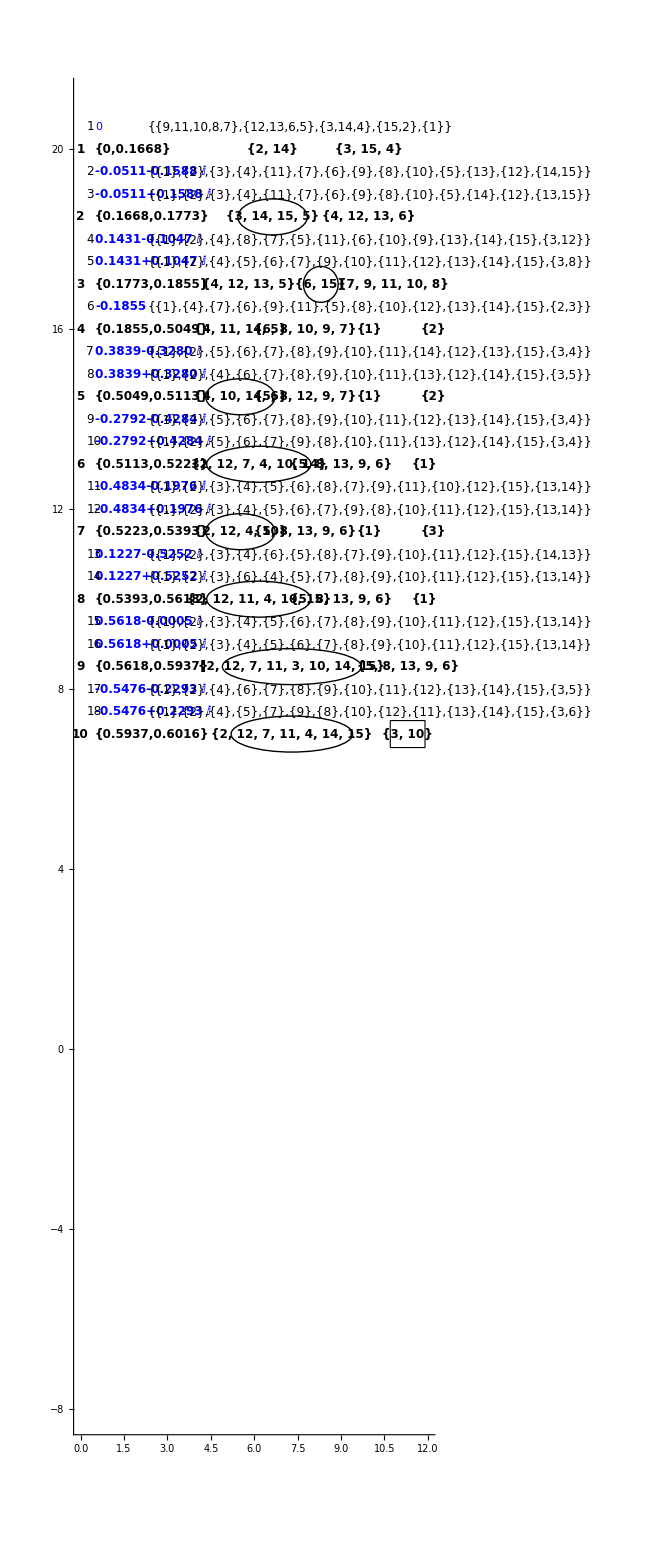

```mathematica
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],Graphics@Translate[annuliMonodromyGraphics,{3.3,0}],
Graphics@Translate[poleLinkGraphics,{annuliOffset,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
```

```mathematica
yOffsetFinal//N
```

5.5

```mathematica
annulusIndexOffset=0;
annuliOffset=0.7;
singularOffset=0.6;
singularIndexOffset=1/5;
singularMonodromyOffset=2.7;
yOffsetFinal=5.5
```

5.5

5.5

18.0778

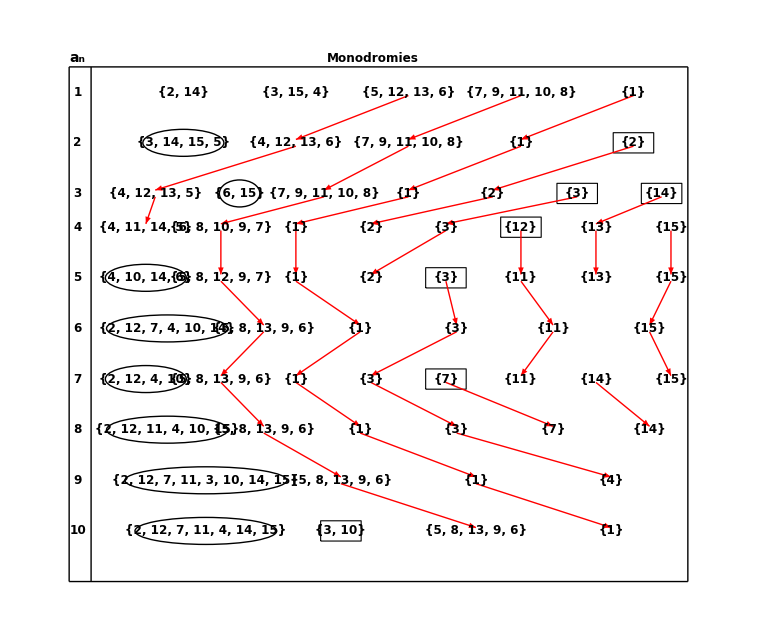

```mathematica
annulusIndexOffset=0;
annuliOffset=0.7;
singularOffset=0.6;
singularIndexOffset=1/5;
singularMonodromyOffset=2.7;
yOffsetFinal=5.5

annularMonodromyOffSet=-0.2;
rightVerticalX=annularMonodromyOffSet+netMax+1/2
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.75},{rightVerticalX,20.75}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.75},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.4,20.75},{0.4,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.65,20.75},{0.65,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.4,20.75},{3.4,yOffsetFinal}}];
vLine5=Graphics@Line[{{5,20.75},{5,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.75},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,21}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,21}];
text3=Graphics@Text[Style["Monodromies",12,Bold,Black],{8.75,21}];

text5=Graphics@Text[Style["Annular branch links with short cuts",12,Bold,Black],{centerX,21}];
 
gFile=Show[{Graphics@annulusIndexGraphics,
(*Graphics@Translate[annuliGraphics,{annuliOffset,0}],*)
(*Graphics@Translate[singularPointGraphics,{singularOffset,0}],*)
(*Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],*)Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],(*Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],*)
topHorizLine,bottomHorizLine,
(*hline1,*)text1,text3,(*text5,*)vLine1,vLine2,(*vLine3,vLine4,*)(*vLine5,*)vLine6,
Graphics@Translate[arrowTable,{annularMonodromyOffSet,0}],
Graphics@Translate[poleLinkGraphics,{4,0}](*,
Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21.5}]*)}]
```

### Export the annular table with branch links to file (used by the Chapter 8 notebook)

```mathematica
(*
 export annular table with branch links to file for Chapter 8
*)
Export[annularTableWithBranchLinksFileName[$theTestCase],gFile];
```

### Section 8.8: Create Annular continuation diagram for testCase0055

```mathematica
(*
 do the annulus numbers
*)
annulusIndexOffset=0;
annuliOffset=0.5;
singularOffset=0.5;
singularIndexOffset=1/5;
singularMonodromyOffset=2.3;


agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
annuliStart=1
annuliEnd=Length@theAnnuli



For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

1

13

9

{{1,20},{2,19},{3,55/3},{4,52/3},{5,49/3},{6,46/3},{7,44/3},{8,41/3},{9,38/3},{10,12},{11,11},{12,31/3},{13,29/3}}

0.

9

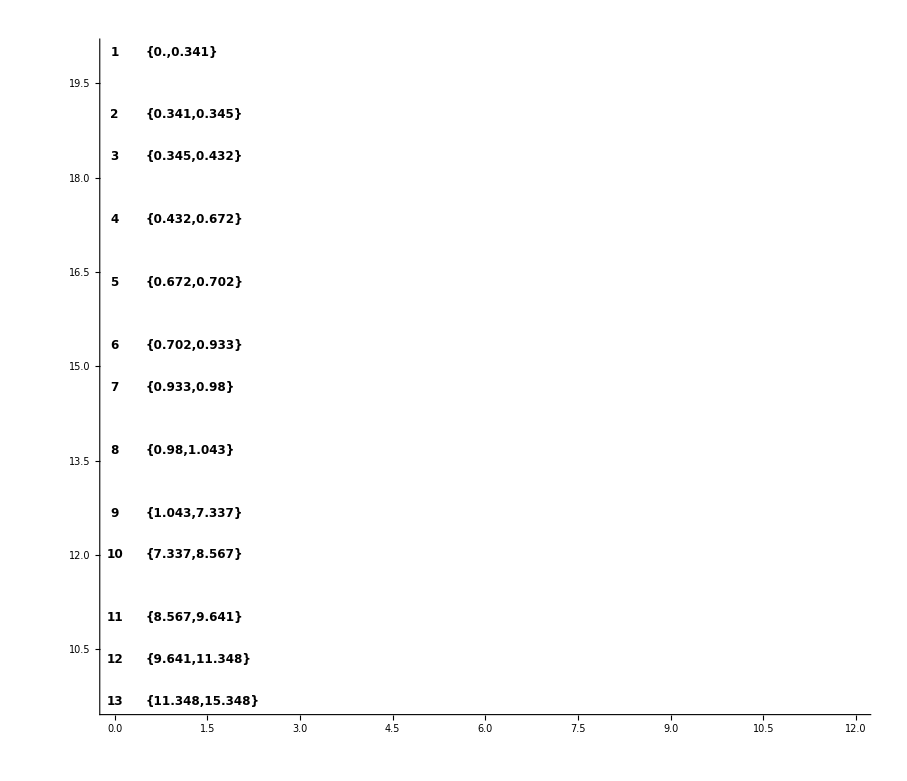

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
(*Print["k: ",k," domain: ",SetAccuracy[annulusTable[[aIndex,3]],3]];*)
AppendTo[annuliGraphics,Inset[Style[SetAccuracy[annulusTable[[aIndex,3]],4],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
(*AppendTo[annuliGraphics,Inset[Style[SetAccuracy[annulusTable[[-1,3]],4],12,Black,Bold],{0,yOffSet},Left]];*)
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

poleLinkGraphicsData: {}

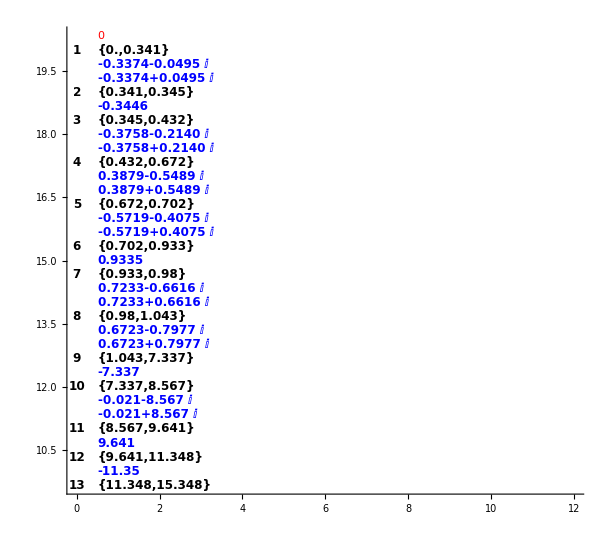

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=annuliStart,k<=annuliEnd-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}]},Axes->True,PlotRange->{{0,12},All}]
```

sIndex: {3,4}

sIndex: {6}

sIndex: {8,9}

sIndex: {11,12}

sIndex: {14,15}

sIndex: {17}

sIndex: {19,20}

sIndex: {22,23}

sIndex: {25}

sIndex: {27,28}

sIndex: {30}

sIndex: {32}

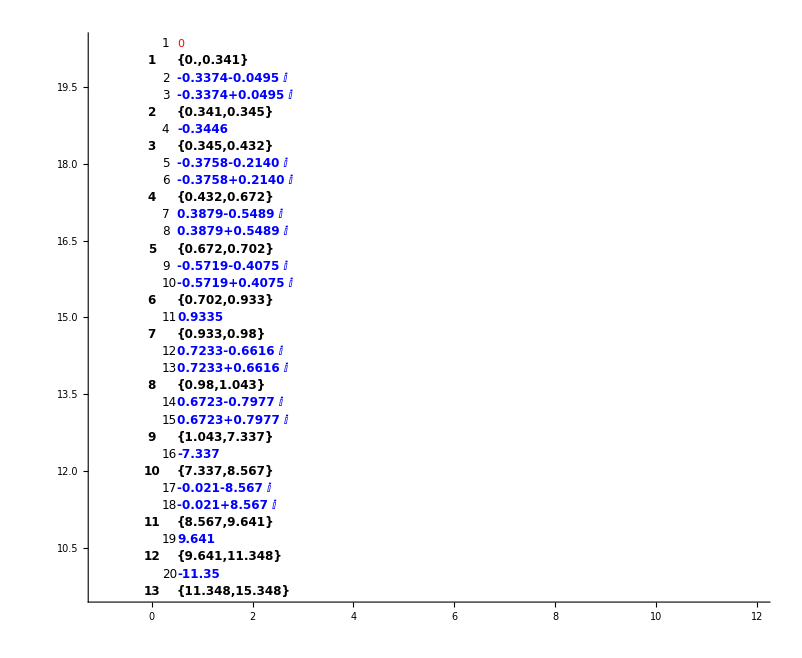

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}]},PlotRange->{{-1,12},All},Axes->True]
```

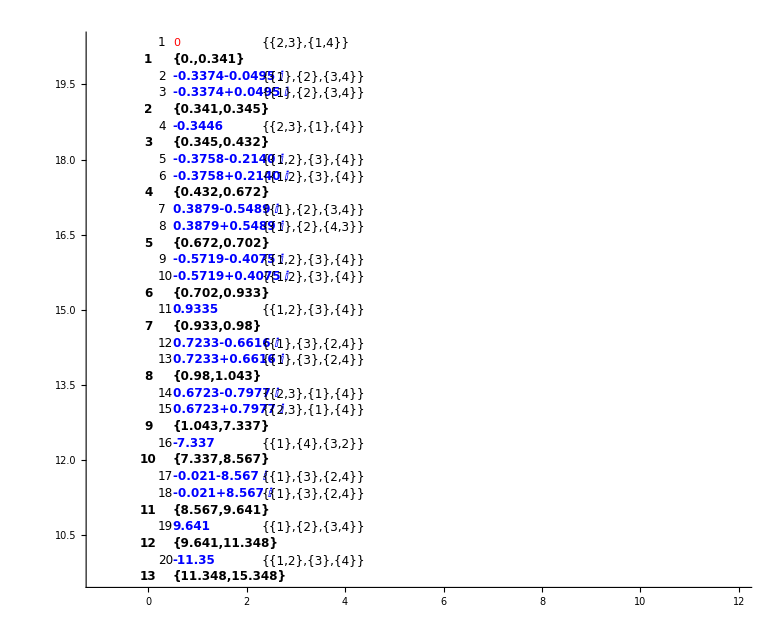

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
(*MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromiesR,$minRadiusArray//N}]//MatrixForm
*)
 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=annuliEnd-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
(*Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];*)
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{2.3,0}]},PlotRange->{{-1,12},All},Axes->True]
```

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=annuliStart,k<=annuliEnd,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1,4},{2,3}}

x-locations: {10/3,20/3}

Monodromy: {{1,4},{2,3}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,2,4}}

x-locations: {5}

Monodromy: {{2,4},{1},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,4,2}}

x-locations: {5}

Monodromy: {{1,2},{3},{4}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4}}

x-locations: {2,4,6,8}

Monodromy: {{2,4,3},{1}}

x-locations: {10/3,20/3}

Monodromy: {{2,4,3},{1}}

x-locations: {10/3,20/3}

Monodromy: {{3,4},{1},{2}}

x-locations: {5/2,5,15/2}

Monodromy: {{3,4},{1},{2}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4}}

x-locations: {2,4,6,8}

Monodromy: {{1,4},{2},{3}}

x-locations: {5/2,5,15/2}

)

```mathematica
continuationList
```

{{1,{4},{4}},{1,{5},{5}},{2,{4},{4}},{2,{5},{5}},{3,{4},{4}},{3,{5},{5}},{4,{1,2,3},{1,2,3}},{4,{4},{4}},{4,{5},{5}},{5,{4},{4}},{5,{5},{5}},{6,{1,3,2},{1,3,2}},{14,{1},{1}},{15,{1},{1}},{16,{4},{5}},{16,{5},{4}},{17,{1,3,2},{1,3,2}},{17,{4},{4}},{17,{5},{5}},{18,{1,3,2},{1,3,2}},{19,{1,3,2},{1,3,2}},{19,{4},{4}},{19,{5},{5}},{23,{5},{5}},{24,{3,4},{3,4}},{24,{5},{5}},{25,{1},{1}},{25,{2},{2}},{25,{5},{5}}}

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

{}

(1 | 20 | {10/3,20/3}
2 | 19 | {10/3,20/3}
3 | 55/3 | {5}
4 | 52/3 | {5/2,5,15/2}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2}
7 | 44/3 | {2,4,6,8}
8 | 41/3 | {10/3,20/3}
9 | 38/3 | {10/3,20/3}
10 | 12 | {5/2,5,15/2}
11 | 11 | {5/2,5,15/2}
12 | 31/3 | {2,4,6,8}
13 | 29/3 | {5/2,5,15/2})

```mathematica
contLinks
```

{{6,{{{3},{3}},{{4},{4}}}},{7,{{{1},{1}}}},{8,{{{1},{1}}}},{9,{{{1},{1}}}},{10,{{{1},{1}}}},{11,{{{1},{1}},{{2},{2}}}},{12,{{{2},{2}},{{3},{3}}}}}

(6 | {{{3},{3}},{{4},{4}}}
7 | {{{1},{1}}}
8 | {{{1},{1}}}
9 | {{{1},{1}}}
10 | {{{1},{1}}}
11 | {{{1},{1}},{{2},{2}}}
12 | {{{2},{2}},{{3},{3}}})

{6,{{{3},{3}},{{4},{4}}}}

(1 | 20 | {10/3,20/3}
2 | 19 | {10/3,20/3}
3 | 55/3 | {5}
4 | 52/3 | {5/2,5,15/2}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2}
7 | 44/3 | {2,4,6,8}
8 | 41/3 | {10/3,20/3}
9 | 38/3 | {10/3,20/3}
10 | 12 | {5/2,5,15/2}
11 | 11 | {5/2,5,15/2}
12 | 31/3 | {2,4,6,8}
13 | 29/3 | {5/2,5,15/2})

{16,{17}}

preMonodromy: {{1,2},{3},{4}}

{18,{19,20}}

postMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

2

3

6

7

46/3

44/3

5

6

0.1

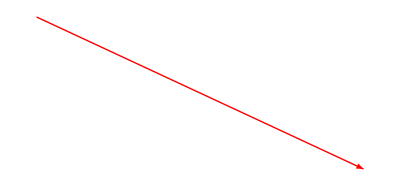

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}]
```

```mathematica
contLinks
Length@contLinks
```

{{6,{{{3},{3}},{{4},{4}}}},{7,{{{1},{1}}}},{8,{{{1},{1}}}},{9,{{{1},{1}}}},{10,{{{1},{1}}}},{11,{{{1},{1}},{{2},{2}}}},{12,{{{2},{2}},{{3},{3}}}}}

7

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag

```mathematica
contLinks
```

{{6,{{{3},{3}},{{4},{4}}}},{7,{{{1},{1}}}},{8,{{{1},{1}}}},{9,{{{1},{1}}}},{10,{{{1},{1}}}},{11,{{{1},{1}},{{2},{2}}}},{12,{{{2},{2}},{{3},{3}}}}}

```mathematica
(*
 do arrows
*)


(*  contLinks=continuationRecords[[annuliStart;;annuliEnd,{1,8}]];*)
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks-1},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{1,2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

currentPreBranch: {3}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{1,2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 7

currentContLink: 7

preMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{2,4,3},{1}}

postMonodromy: {{2,4,3},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 8

currentContLink: 8

preMonodromy: {{2,4,3},{1}}

postMonodromy: {{2,4,3},{1}}

postMonodromy: {{2,4,3},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 9

currentContLink: 9

preMonodromy: {{2,4,3},{1}}

postMonodromy: {{3,4},{1},{2}}

postMonodromy: {{3,4},{1},{2}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 10

currentContLink: 10

preMonodromy: {{3,4},{1},{2}}

postMonodromy: {{3,4},{1},{2}}

postMonodromy: {{3,4},{1},{2}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{3,4},{1},{2}}

postMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 11

currentContLink: 11

preMonodromy: {{3,4},{1},{2}}

postMonodromy: {{1},{2},{3},{4}}

postMonodromy: {{1},{2},{3},{4}}

currentPreBranch: {2}

testa

testb

2.75

3.3

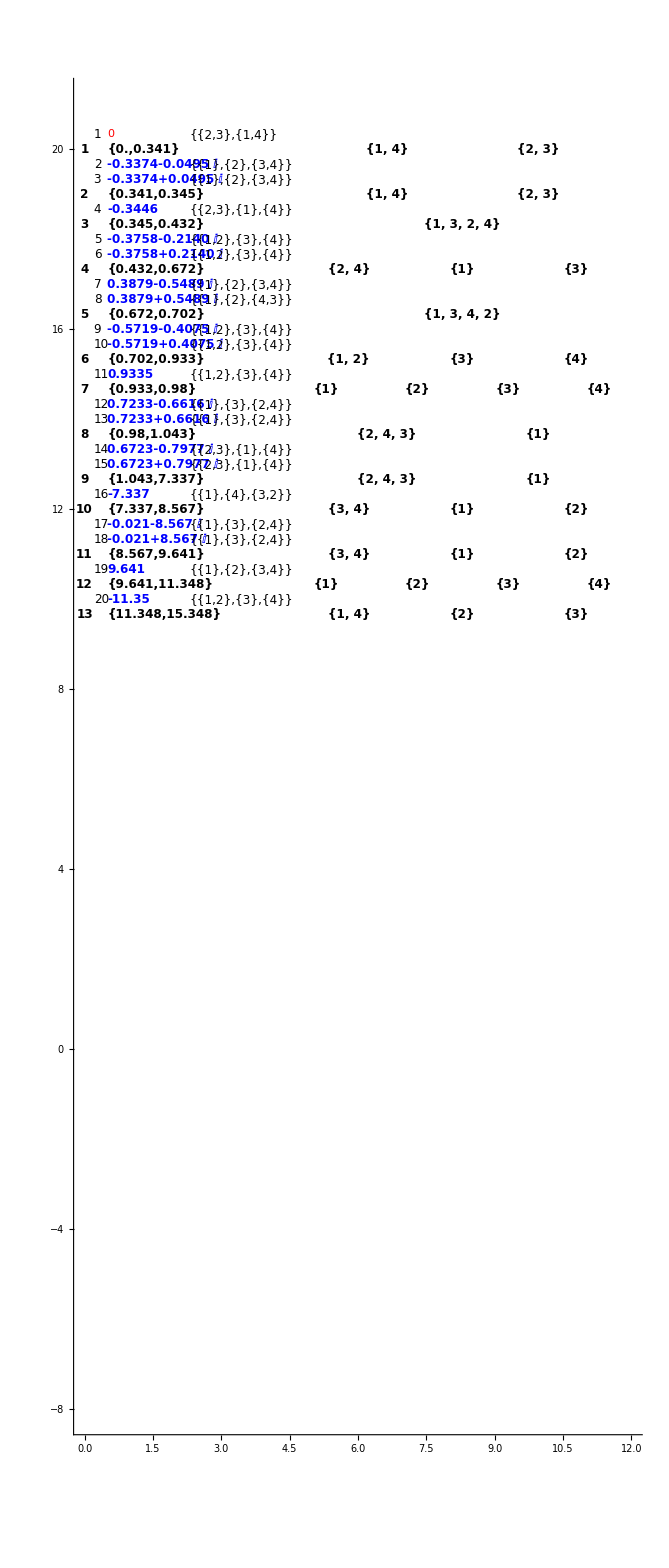

```mathematica
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{annuliOffset,0}],Graphics@Translate[singularPointGraphics,{singularOffset,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],Graphics@Translate[annuliMonodromyGraphics,{3.3,0}],
Graphics@Translate[poleLinkGraphics,{annuliOffset,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
```

```mathematica
annulusIndexOffset=0;
annuliOffset=0.6;
singularOffset=0.6;
singularIndexOffset=1/5;
singularMonodromyOffset=2.7;
```

11.75

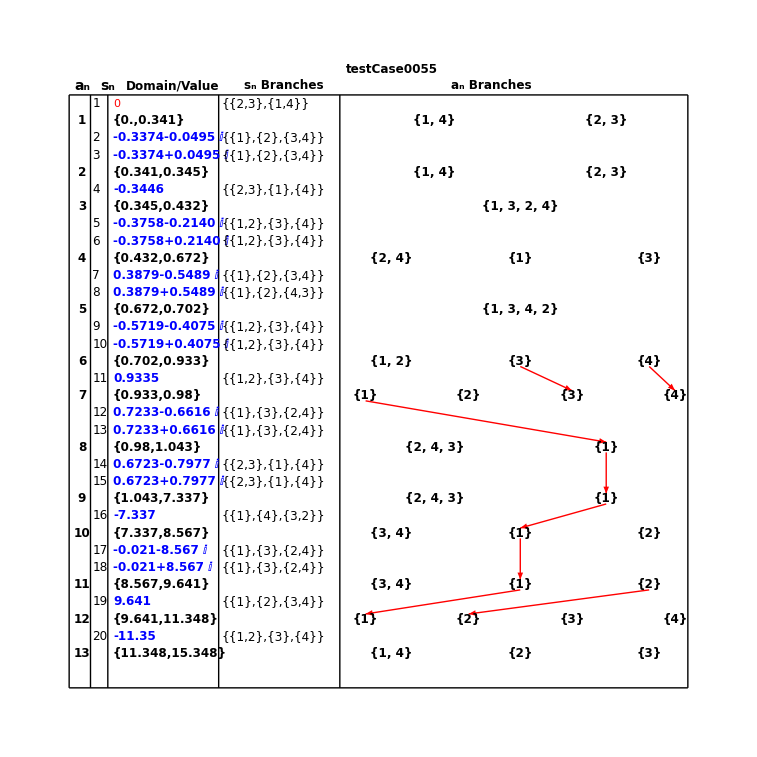

```mathematica
annularMonodromyOffSet=3.5;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.164,20.5},{0.164,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.5,20.5},{0.5,yOffsetFinal}}];
vLine4=Graphics@Line[{{2.65,20.5},{2.65,yOffsetFinal}}];
vLine5=Graphics@Line[{{5,20.5},{5,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{annuliOffset,0}],
Graphics@Translate[singularPointGraphics,{singularOffset,0}],
Graphics@Translate[singularPointMonodromyGraphics,{singularMonodromyOffset,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{singularIndexOffset,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{3.5,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Export the annular table to file (used by the Chapter 8 notebook)

```mathematica
(*
 export annular table with branch links to file for Chapter 8
*)
Export[annularTableWithBranchLinksFileName[$theTestCase],gFile];
```

### Section 8.9: Special case for testCase0031 with multiple pole records on one line

```mathematica
(*
 do the annulus numbers
*)
annularMonodromyOffSet=0;
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
annuliStart=1;
annuliEnd=Length@theAnnuli;

For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet;
 (*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliGraphics,Inset[Style[ToString[N[annulusTable[[aIndex,3]],4]],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* 
print last annulus
*)
(*If[MemberQ[Range[annuliStart,annuliEnd],Length@theAnnuli],
AppendTo[annuliGraphics,Inset[Style[ToString[N[annulusTable[[-1,3]],4]],12,Black,Bold],{0,yOffSet},Left]];
];*)
  (*
 do the singular points
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[MemberQ[Range[annuliStart,annuliEnd],1],
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];
];

poleLinkGraphicData={};
For[k=annuliStart,k<=(annuliEnd)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
For[k2=1,k2<=Length@thePoleLinks,k2++,
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
singYOffset=yOffSet-k2 sgIndex;
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];
];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["pole arrow"];
AppendTo[singularPointGraphics,Inset[Style[ToString[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[ToString[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(*
 do the singular indexes
*)
(*Print["test1"];*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=annuliStart,k<=(annuliEnd)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];
(*Print["test2"];*)

For[k=annuliStart,k<=(annuliEnd)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
(*AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

];
yOffSet-=agIndex;
];
 (*
 do annular monodromies
*)
(*Print["test3"];*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=annuliStart,k<=(annuliEnd),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*Print["test4"];*)
```

pole arrow

pole arrow

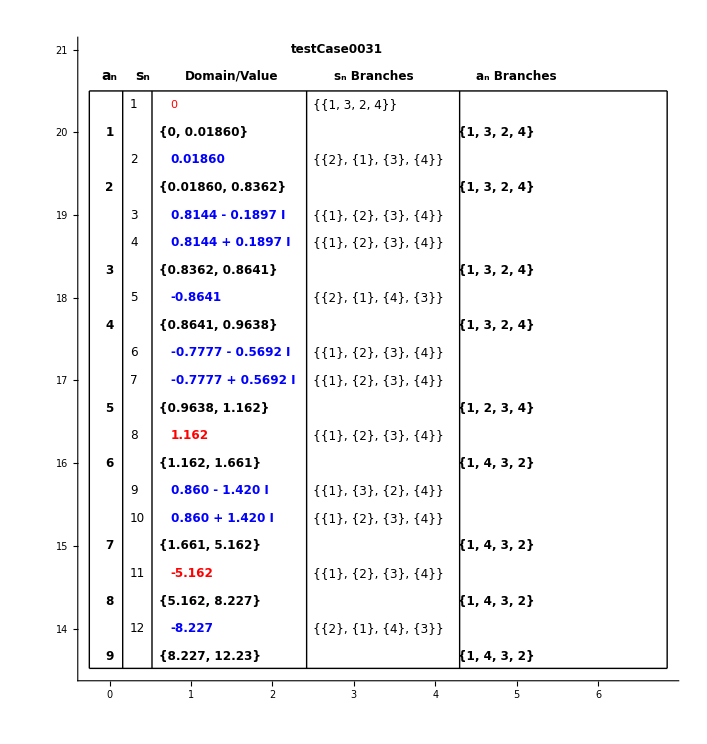

```mathematica
annularDataOffset=-0.25;
text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.4,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.5,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.25,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{5,20.68}];

annularContinuationDiagram=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{.6,0}],
Graphics@Translate[singularPointGraphics,{.75,0}],
Graphics@Translate[singularPointMonodromyGraphics,{2.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularDataOffset,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
(*
Graphics@Translate[arrowTable,{-0.25,0}],
Graphics@Translate[poleLinkGraphics,{0,0}],*)
Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]},Axes->True]
```

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
yLoc=poleLinkGraphicData[[i,3]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];
]
poleLinkGraphics[[1,2]]={5,49/3};
poleLinkGraphics[[2,2]]={5.5,49/3};
poleLinkGraphics[[3,2]]={6,49/3};
poleLinkGraphics[[4,2]]={6.5,49/3};

poleLinkGraphics[[5,2]]={5,44/3};
poleLinkGraphics[[6,2]]={5.5,44/3};
poleLinkGraphics[[7,2]]={6,44/3};
poleLinkGraphics[[8,2]]={6.5,44/3};
```

```mathematica
(*
 create a continuation diagram
*)
(*Print["test5"];*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
contLinks=continuationRecords[[All,{1,8}]];
currentContAIndex=2;

currentContLink=contLinks[[currentContAIndex]];


{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];

{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
currentBranchLink=1;
Print["x1"];
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
(*Print["x2"];*)
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
(*Print["temp"];*)
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];
(*Print["x3"];*)
dy=0.1;
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];

(*
 do arrows
*)
(*Print["test6"];*)
  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;

contRange=Intersection[contLinks[[All,1]],Range[annuliStart,annuliEnd-1]];
contPos=Position[contLinks[[All,1]],x_/;x==#]&/@ contRange//Flatten;
Print["contPos: ",contPos];



arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentContLink: ",currentContLink];
theCurrentAnnulus=currentContLink[[1]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arrow points
*)
(*Print["g1"];*)
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
(*Print["aa"];*)
prePos=Position[xLocationSave[[All,1]],x_/;x==preLocationNum][[1,1]];
preYVal=xLocationSave[[prePos,2]];
(*Print["bb"];*)

postPos=Position[xLocationSave[[All,1]],x_/;x==postLocationNum][[1,1]];
postYVal=xLocationSave[[postPos,2]];
(*Print["xx"];*)
preXVal=xLocationSave[[prePos,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postPos,3,currentPostBranchLoc]];
Print["theCurrentAnnulus: ",theCurrentAnnulus];
Print["theCurrentPreBranch: ",theCurrentPreBranch];
poleData=poleRecords[[All,{1,2}]];
If[MemberQ[poleData,{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print["dashed arrow"];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,contPos},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];


rightVerticalX=annularMonodromyOffSet+netMax+1/3
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{6.85,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,13.52},{6.85,13.52}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,13.52}}];

vLine2=Graphics@Line[{{0.16,20.5},{0.16,13.52}}];

vLine3=Graphics@Line[{{0.52,20.5},{0.52,13.52}}];

vLine4=Graphics@Line[{{2.42,20.5},{2.42,13.52}}];
vLine5=Graphics@Line[{{4.3,20.5},{4.3,13.52}}];
vLine6=Graphics@Line[{{6.85,20.5},{6.85,13.52}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.331,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.38,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.26,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{5.5,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)


annularDataOffset=-0.25;

annularContinuationDiagram=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{.6,0}],
Graphics@Translate[singularPointGraphics,{.75,0}],
Graphics@Translate[singularPointMonodromyGraphics,{2.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularDataOffset,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,

Graphics@Translate[arrowTable,{-0.25,0}],
Graphics@Translate[poleLinkGraphics,{0.05,0}],
Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

x1

1

contPos: {1,2,3,4,5,6,7,8}

currentContLink: {1,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 1

theCurrentPreBranch: {1,3,2,4}

currentContLink: {2,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 2

theCurrentPreBranch: {1,3,2,4}

currentContLink: {3,{{{1,3,2,4},{1,3,2,4}}}}

theCurrentAnnulus: 3

theCurrentPreBranch: {1,3,2,4}

currentContLink: {4,{{{1,3,2,4},{1,2,3,4}}}}

theCurrentAnnulus: 4

theCurrentPreBranch: {1,3,2,4}

currentContLink: {5,{{{1,2,3,4},{1,4,3,2}}}}

theCurrentAnnulus: 5

theCurrentPreBranch: {1,2,3,4}

dashed arrow

currentContLink: {6,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 6

theCurrentPreBranch: {1,4,3,2}

currentContLink: {7,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 7

theCurrentPreBranch: {1,4,3,2}

dashed arrow

currentContLink: {8,{{{1,4,3,2},{1,4,3,2}}}}

theCurrentAnnulus: 8

theCurrentPreBranch: {1,4,3,2}

16/3

-Graphics-

### Export the annular table with branch links to file (used by the Chapter 8 notebook)

```mathematica
(*
 export annular table with branch links to file for Chapter 8
*)
Export[annularTableWithBranchLinksFileName[$theTestCase],gFile];
```

### Section 8.10: Create Annular continuation diagram for testCase0001

#### Section 8.10.1: Set up annuli indexes

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

-4

{{1,20},{2,19},{3,18},{4,17},{5,16},{6,15},{7,14},{8,13},{9,12},{10,11},{11,10},{12,9},{13,8},{14,7},{15,6},{16,5},{17,4},{18,3},{19,2},{20,4/3},{21,1/3},{22,-1/3},{23,-4/3},{24,-2},{25,-8/3},{26,-10/3}}

#### Section 8.10.2: Set up annuli

k: 1 domain: {0.,0.882183}

k: 2 domain: {0.882183,0.985943}

k: 3 domain: {0.985943,0.986175}

k: 4 domain: {0.986175,1.16729}

k: 5 domain: {1.16729,1.17131}

k: 6 domain: {1.17131,1.17494}

k: 7 domain: {1.17494,1.24932}

k: 8 domain: {1.24932,1.27293}

k: 9 domain: {1.27293,1.30049}

k: 10 domain: {1.30049,1.30107}

k: 11 domain: {1.30107,1.30283}

k: 12 domain: {1.30283,1.31832}

k: 13 domain: {1.31832,1.33968}

k: 14 domain: {1.33968,1.35302}

k: 15 domain: {1.35302,1.41679}

k: 16 domain: {1.41679,1.48796}

k: 17 domain: {1.48796,1.54133}

k: 18 domain: {1.54133,1.54922}

k: 19 domain: {1.54922,1.69909}

k: 20 domain: {1.69909,1.96623}

k: 21 domain: {1.96623,1.99578}

k: 22 domain: {1.99578,2.698}

k: 23 domain: {2.698,2.81327}

k: 24 domain: {2.81327,2.84583}

k: 25 domain: {2.84583,3.03663}

-10/3

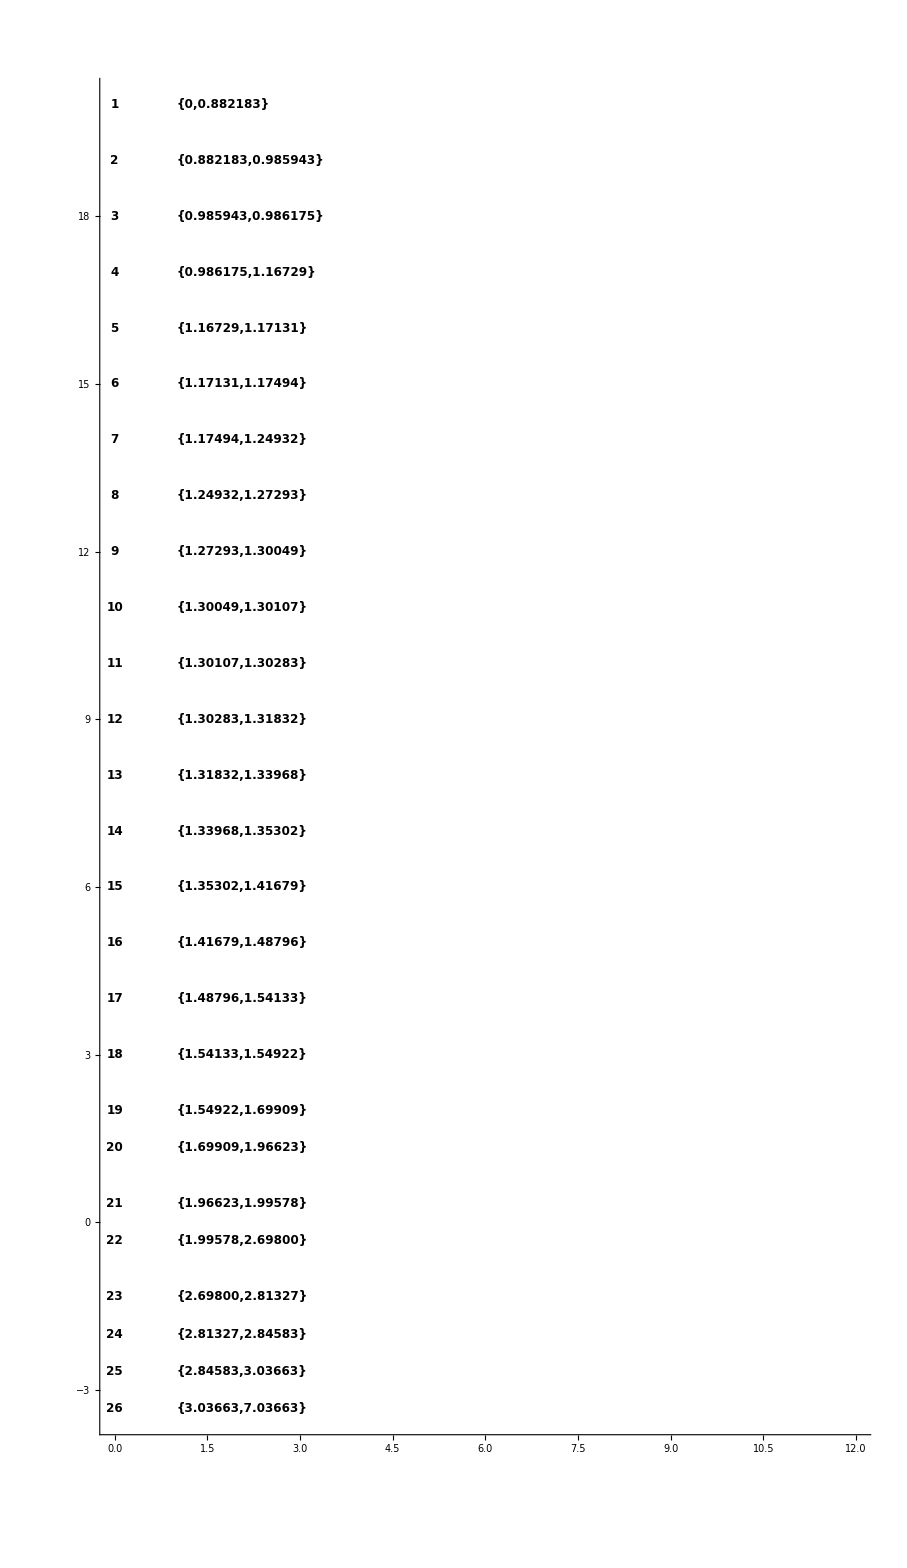

```mathematica
(*
 do the annuli
*)
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.10.3: Set up singular points

Annulus 4 has a pole link

annulus monodromy: {{1,2,3},{4},{5}}

pole links: {{7,2,1,2},{8,2,5,2}}

nextPoleLink: nextPoleLink

Processing pole link {7,2,1,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 7

Sing pole links: {2,1,2}

y-offset for this sing: 50/3

nextPoleLink: nextPoleLink

Processing pole link {8,2,5,2}

Annulus branch sheet: 2

annulusBranchIndex: 1

Singular point: 8

Sing pole links: {2,5,2}

y-offset for this sing: 49/3

Pole: -0.2023-1.1496 ⅈ

Pole: -0.2023+1.1496 ⅈ

Annulus 17 has a pole link

annulus monodromy: {{1,3,2},{4},{5}}

pole links: {{33,4,5,4},{34,5,5,5}}

nextPoleLink: nextPoleLink

Processing pole link {33,4,5,4}

Annulus branch sheet: 4

annulusBranchIndex: 2

Singular point: 33

Sing pole links: {4,5,4}

y-offset for this sing: 11/3

nextPoleLink: nextPoleLink

Processing pole link {34,5,5,5}

Annulus branch sheet: 5

annulusBranchIndex: 3

Singular point: 34

Sing pole links: {5,5,5}

y-offset for this sing: 10/3

Pole: 1.052-1.127 ⅈ

Pole: 1.052+1.127 ⅈ

Annulus 19 has a pole link

annulus monodromy: {{1,3,2},{4},{5}}

pole links: {{37,3,1,3}}

nextPoleLink: nextPoleLink

Processing pole link {37,3,1,3}

Annulus branch sheet: 3

annulusBranchIndex: 1

Singular point: 37

Sing pole links: {3,1,3}

y-offset for this sing: 5/3

Pole: -1.699

poleLinkGraphicsData: {{4,7,50/3,1,{2,1,2}},{4,8,49/3,1,{2,5,2}},{17,33,11/3,2,{4,5,4}},{17,34,10/3,3,{5,5,5}},{19,37,5/3,1,{3,1,3}}}

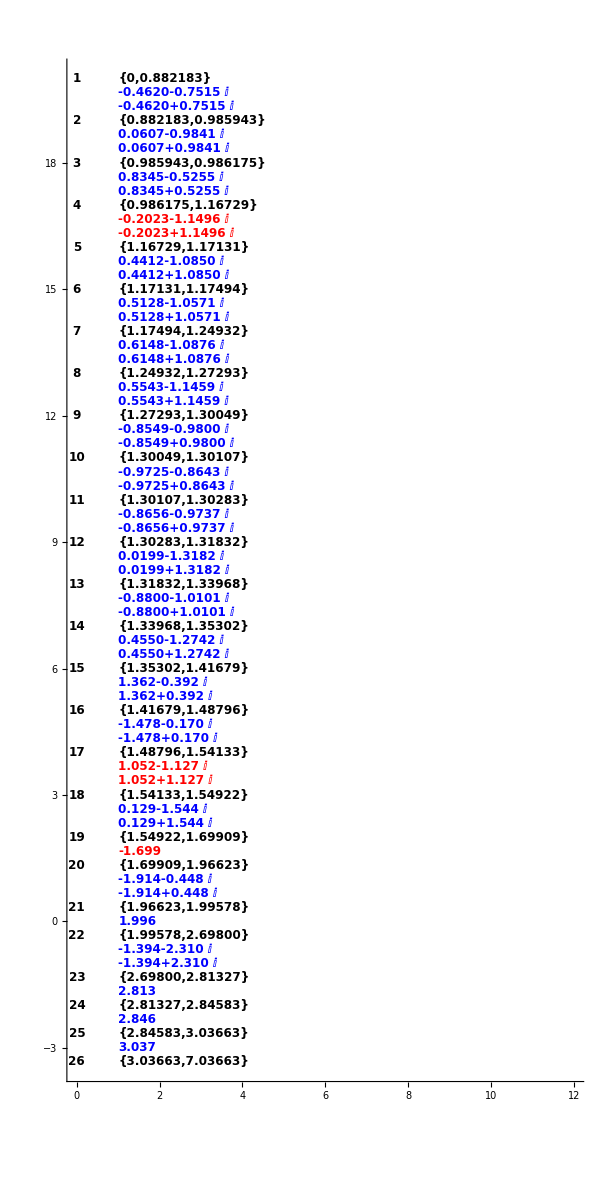

```mathematica
(*
 do the singular points
*)
(*starRecords=Select[updatedPoleAnalysisReport,#[[8]]=="*"&];
starRecords//N//MatrixForm
*)
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.10.3: Set up singular indexes

sIndex: {2,3}

sIndex: {5,6}

sIndex: {8,9}

sIndex: {11,12}

sIndex: {14,15}

sIndex: {17,18}

sIndex: {20,21}

sIndex: {23,24}

sIndex: {26,27}

sIndex: {29,30}

sIndex: {32,33}

sIndex: {35,36}

sIndex: {38,39}

sIndex: {41,42}

sIndex: {44,45}

sIndex: {47,48}

sIndex: {50,51}

sIndex: {53,54}

sIndex: {56}

sIndex: {58,59}

sIndex: {61}

sIndex: {63,64}

sIndex: {66}

sIndex: {68}

sIndex: {70}

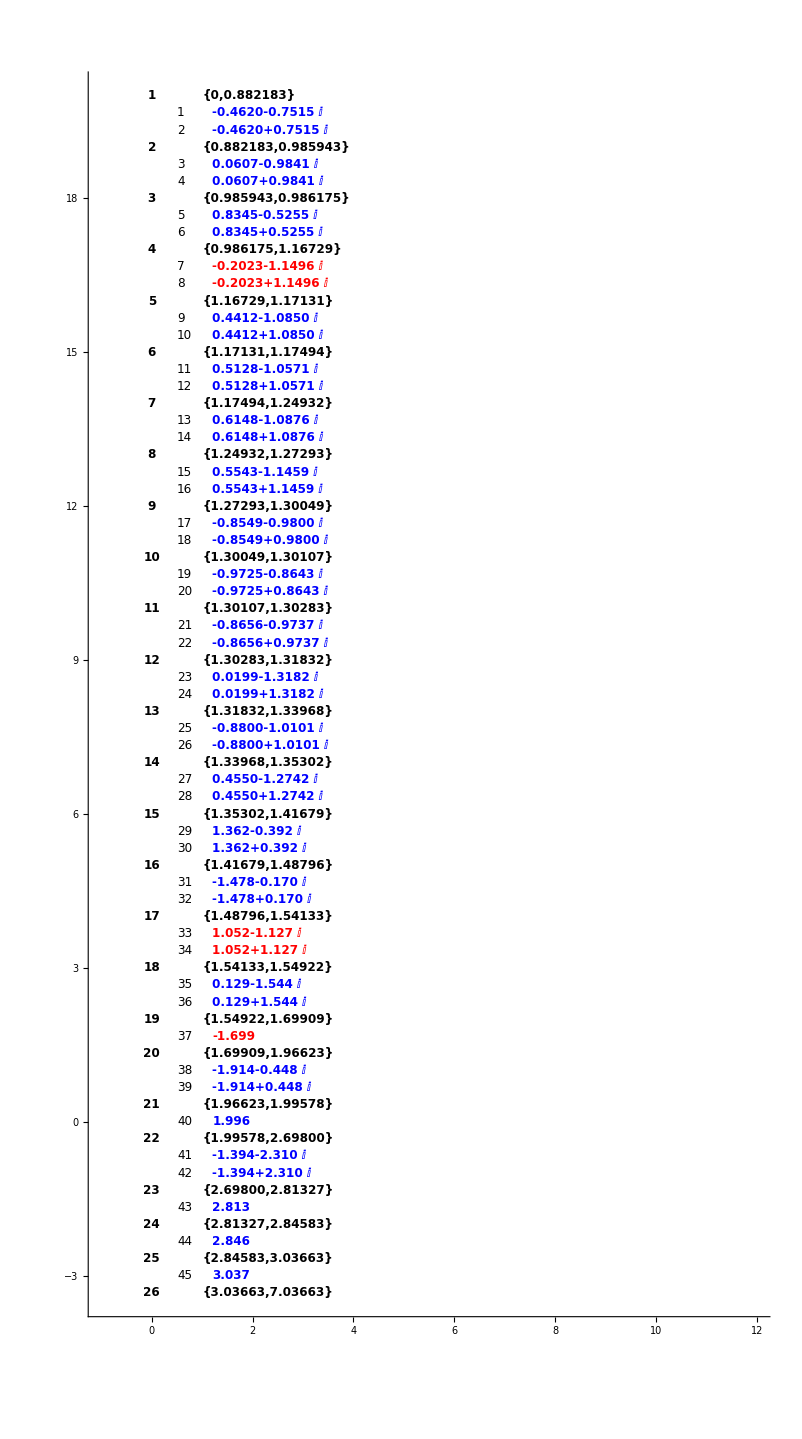

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.10.4: Set up singular monodromies

(1 | {{1,2},{3},{4},{5}} | 0.1515
2 | {{1,2},{3},{4},{5}} | 0.1515
3 | {{1,2},{3},{4},{5}} | 0.103608
4 | {{1,3},{2},{4},{5}} | 0.103608
5 | {{1,2},{3},{4},{5}} | 0.181262
6 | {{1,2},{3},{4},{5}} | 0.181262
7 | {{1},{2},{3},{4},{5}} | 0.0929628
8 | {{1},{2},{3},{4},{5}} | 0.0929628
9 | {{1,2},{3},{4},{5}} | 0.0255969
10 | {{1,2},{3},{4},{5}} | 0.0255969
11 | {{4,5},{1},{2},{3}} | 0.0255969
12 | {{4,5},{1},{2},{3}} | 0.0255969
13 | {{3,4},{1},{2},{5}} | 0.0280212
14 | {{3,4},{1},{2},{5}} | 0.0280212
15 | {{2,3},{1},{4},{5}} | 0.0280212
16 | {{2,3},{1},{4},{5}} | 0.0280212
17 | {{4,5},{1},{2},{3}} | 0.00416089
18 | {{4,5},{1},{2},{3}} | 0.00416089
19 | {{2,4},{1},{3},{5}} | 0.0509919
20 | {{3,4},{1},{2},{5}} | 0.0509919
21 | {{2,4},{1},{3},{5}} | 0.00416089
22 | {{2,4},{1},{3},{5}} | 0.00416089
23 | {{3,5},{1},{2},{4}} | 0.0835795
24 | {{3,5},{1},{2},{4}} | 0.0835795
25 | {{1,2},{3},{4},{5}} | 0.0130509
26 | {{1,2},{3},{4},{5}} | 0.0130509
27 | {{2,3},{1},{4},{5}} | 0.0540883
28 | {{2,3},{1},{4},{5}} | 0.0540883
29 | {{3,5},{1},{2},{4}} | 0.181262
30 | {{3,5},{1},{2},{4}} | 0.181262
31 | {{1,2},{3},{4},{5}} | 0.0929202
32 | {{1,2},{3},{4},{5}} | 0.0929202
33 | {{1},{2},{3},{4},{5}} | 0.146267
34 | {{1},{2},{3},{4},{5}} | 0.146267
35 | {{4,5},{1},{2},{3}} | 0.0835795
36 | {{4,5},{1},{2},{3}} | 0.0835795
37 | {{1},{2},{3},{4},{5}} | 0.0929202
38 | {{4,5},{1},{2},{3}} | 0.165765
39 | {{3,5},{1},{2},{4}} | 0.165765
40 | {{4,5},{1},{2},{3}} | 0.248482
41 | {{4,5},{1},{2},{3}} | 0.465952
42 | {{4,5},{1},{2},{3}} | 0.465952
43 | {{2,3},{1},{4},{5}} | 0.0108537
44 | {{1,2},{3},{4},{5}} | 0.0108537
45 | {{3,4},{1},{2},{5}} | 0.0635991)

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,3},{2},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{3,4},{1},{2},{5}}

the sing monodromy: {{3,4},{1},{2},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{3,4},{1},{2},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{2,4},{1},{3},{5}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{1},{2},{3},{4},{5}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{3,5},{1},{2},{4}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{4,5},{1},{2},{3}}

the sing monodromy: {{2,3},{1},{4},{5}}

the sing monodromy: {{1,2},{3},{4},{5}}

the sing monodromy: {{3,4},{1},{2},{5}}

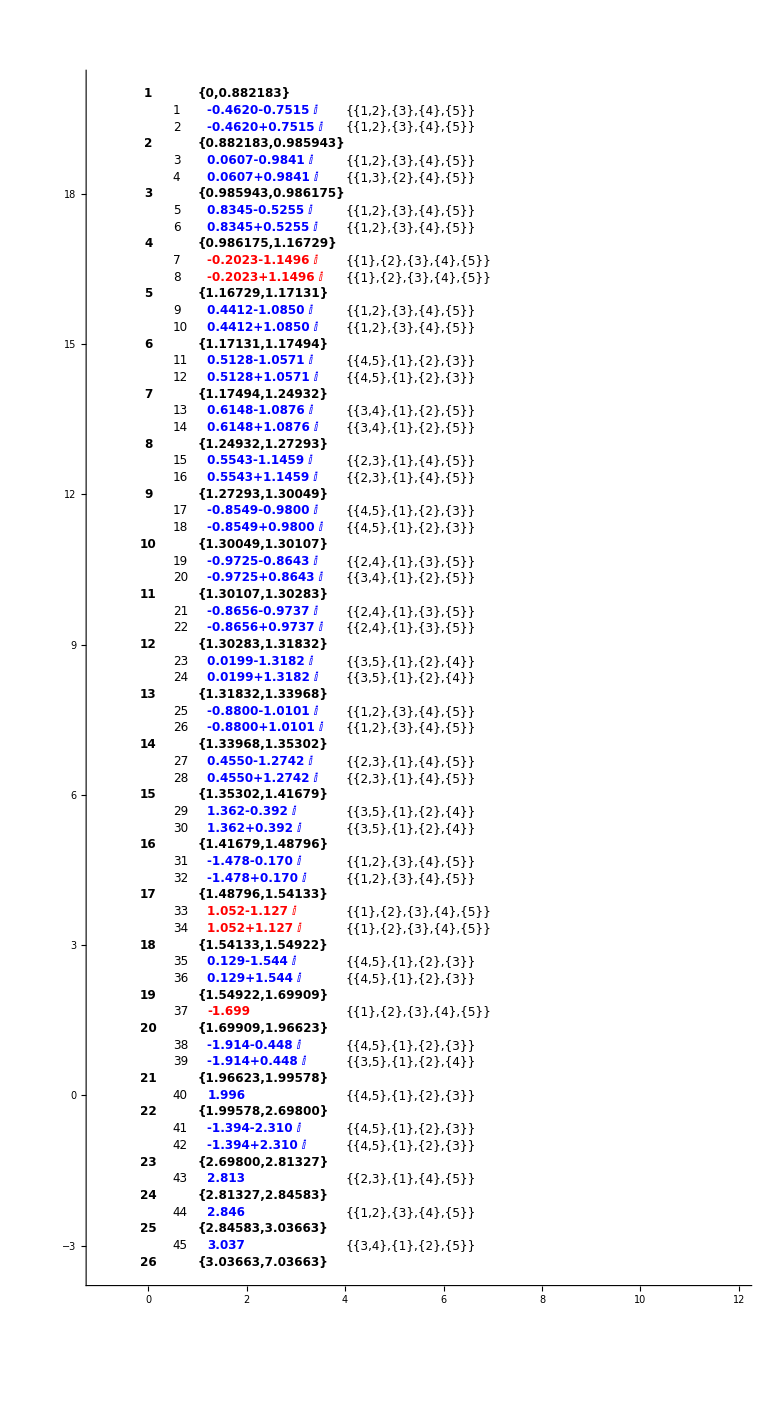

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm

 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.10.5: Set up annular monodromies

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,3},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,2,3},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,4,2,3,5}}

x-locations: {5}

Monodromy: {{1,5,2,3,4}}

x-locations: {5}

Monodromy: {{2,4},{3,5},{1}}

x-locations: {5/2,5,15/2}

Monodromy: {{2,5},{3,4},{1}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2},{4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,4,5,2}}

x-locations: {5}

Monodromy: {{1,3,5,2},{4}}

x-locations: {10/3,20/3}

Monodromy: {{1,3,4,2},{5}}

x-locations: {10/3,20/3}

Monodromy: {{1,2},{3,4},{5}}

x-locations: {5/2,5,15/2}

Monodromy: {{3,4},{1},{2},{5}}

x-locations: {2,4,6,8}

Monodromy: {{1},{2},{3},{4},{5}}

x-locations: {5/3,10/3,5,20/3,25/3}

#### Section 8.10.6: Set up pole links

```mathematica
(*
 do the pole link graphics here
*)
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(4 | 7 | 50/3 | 1 | {2,1,2}
4 | 8 | 49/3 | 1 | {2,5,2}
17 | 33 | 11/3 | 2 | {4,5,4}
17 | 34 | 10/3 | 3 | {5,5,5}
19 | 37 | 5/3 | 1 | {3,1,3})

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5/2,5,15/2}
4 | 17 | {5/2,5,15/2}
5 | 16 | {5/2,5,15/2}
6 | 15 | {5/2,5,15/2}
7 | 14 | {5/2,5,15/2}
8 | 13 | {5}
9 | 12 | {5}
10 | 11 | {5}
11 | 10 | {5}
12 | 9 | {5}
13 | 8 | {5}
14 | 7 | {5/2,5,15/2}
15 | 6 | {5/2,5,15/2}
16 | 5 | {5/3,10/3,5,20/3,25/3}
17 | 4 | {5/2,5,15/2}
18 | 3 | {5/2,5,15/2}
19 | 2 | {5/2,5,15/2}
20 | 4/3 | {5/2,5,15/2}
21 | 1/3 | {5}
22 | -1/3 | {10/3,20/3}
23 | -4/3 | {10/3,20/3}
24 | -2 | {5/2,5,15/2}
25 | -8/3 | {2,4,6,8}
26 | -10/3 | {5/3,10/3,5,20/3,25/3})

currentBranchIndex: 1

currentAnnulus: 4

current sing index: 7

xLocationPos: 4

xLocationData: {4,17,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 50/3

pole link string: {2,1,2}

currentBranchIndex: 1

currentAnnulus: 4

current sing index: 8

xLocationPos: 4

xLocationData: {4,17,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 49/3

pole link string: {2,5,2}

currentBranchIndex: 2

currentAnnulus: 17

current sing index: 33

xLocationPos: 17

xLocationData: {17,4,{5/2,5,15/2}}

xLocation for this link: 5

yLocation for this link: 11/3

pole link string: {4,5,4}

currentBranchIndex: 3

currentAnnulus: 17

current sing index: 34

xLocationPos: 17

xLocationData: {17,4,{5/2,5,15/2}}

xLocation for this link: 15/2

yLocation for this link: 10/3

pole link string: {5,5,5}

currentBranchIndex: 1

currentAnnulus: 19

current sing index: 37

xLocationPos: 19

xLocationData: {19,2,{5/2,5,15/2}}

xLocation for this link: 5/2

yLocation for this link: 5/3

pole link string: {3,1,3}

#### Section 8.10.7: Set up continuation diagram

```mathematica
(*
 create a continuation diagram
*)
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
(* Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/4,0}],Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{4,0}],
Graphics@Translate[poleLinkGraphics,{4,0}]},

Axes->True,PlotRange->{{0,12},{-8,21}}]
*)
```

(1 | {{{4},{4}},{{5},{5}}}
2 | {{{4},{4}},{{5},{5}}}
3 | {{{4},{4}},{{5},{5}}}
4 | {{{1,2,3},{1,2,3}},{{4},{4}},{{5},{5}}}
5 | {{{4},{4}},{{5},{5}}}
6 | {{{1,3,2},{1,3,2}}}
14 | {{{1},{1}}}
15 | {{{1},{1}}}
16 | {{{4},{5}},{{5},{4}}}
17 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
18 | {{{1,3,2},{1,3,2}}}
19 | {{{1,3,2},{1,3,2}},{{4},{4}},{{5},{5}}}
23 | {{{5},{5}}}
24 | {{{3,4},{3,4}},{{5},{5}}}
25 | {{{1},{1}},{{2},{2}},{{5},{5}}})

{1,{{{4},{4}},{{5},{5}}}}

(1 | 20 | {5/3,10/3,5,20/3,25/3}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5/2,5,15/2}
4 | 17 | {5/2,5,15/2}
5 | 16 | {5/2,5,15/2}
6 | 15 | {5/2,5,15/2}
7 | 14 | {5/2,5,15/2}
8 | 13 | {5}
9 | 12 | {5}
10 | 11 | {5}
11 | 10 | {5}
12 | 9 | {5}
13 | 8 | {5}
14 | 7 | {5/2,5,15/2}
15 | 6 | {5/2,5,15/2}
16 | 5 | {5/3,10/3,5,20/3,25/3}
17 | 4 | {5/2,5,15/2}
18 | 3 | {5/2,5,15/2}
19 | 2 | {5/2,5,15/2}
20 | 4/3 | {5/2,5,15/2}
21 | 1/3 | {5}
22 | -1/3 | {10/3,20/3}
23 | -4/3 | {10/3,20/3}
24 | -2 | {5/2,5,15/2}
25 | -8/3 | {2,4,6,8}
26 | -10/3 | {5/3,10/3,5,20/3,25/3})

{1,{2,3}}

preMonodromy: {{1},{2},{3},{4},{5}}

{4,{5,6}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

4

2

1

2

20

19

20/3

5

0.1

#### Section 8.10.9: Set up pole records

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
4 | {1,2,3} | 2 | 7 | L_-1 | {1} | 1 | True | {1,2,3} | 2 | True
4 | {1,2,3} | 2 | 8 | L_-1 | {5} | 5 | True | {1,2,3} | 2 | True
17 | {4} | 4 | 33 | L_-1 | {5} | 5 | True | {4} | 4 | True
17 | {5} | 5 | 34 | L_-1 | {5} | 5 | True | {5} | 5 | True
19 | {1,3,2} | 3 | 37 | L_-1 | {1} | 1 | True | {1,3,2} | 3 | True

#### Section 8.10.10: Set up arrows

```mathematica
(*
 do arrows
*)


  contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 2

currentContLink: 2

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 3

currentContLink: 3

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {1,2,3}

testa

testb

Creating dashed arrow

current pre branch: {1,2,3}

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,2,3},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 5

currentContLink: 5

preMonodromy: {{1,2,3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 6

currentContLink: 6

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 14

currentContLink: 14

preMonodromy: {{2,4},{3,5},{1}}

postMonodromy: {{2,5},{3,4},{1}}

postMonodromy: {{2,5},{3,4},{1}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 15

currentContLink: 15

preMonodromy: {{2,5},{3,4},{1}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 16

currentContLink: 16

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 16

currentContLink: 16

preMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

Creating dashed arrow

current pre branch: {4}

currentAnnulus: 17

currentContLink: 17

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

Creating dashed arrow

current pre branch: {5}

currentAnnulus: 18

currentContLink: 18

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

currentAnnulus: 19

currentContLink: 19

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {1,3,2}

testa

testb

Creating dashed arrow

current pre branch: {1,3,2}

currentAnnulus: 19

currentContLink: 19

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {4}

testa

testb

currentAnnulus: 19

currentContLink: 19

preMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

postMonodromy: {{1,3,2},{4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 23

currentContLink: 23

preMonodromy: {{1,3,4,2},{5}}

postMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{1,2},{3,4},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {3,4}

testa

testb

currentAnnulus: 24

currentContLink: 24

preMonodromy: {{1,2},{3,4},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{3,4},{1},{2},{5}}

currentPreBranch: {5}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {2}

testa

testb

currentAnnulus: 25

currentContLink: 25

preMonodromy: {{3,4},{1},{2},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

postMonodromy: {{1},{2},{3},{4},{5}}

currentPreBranch: {5}

testa

testb

#### Section 8.10.8: Create annular table with branch link graphics

151/12

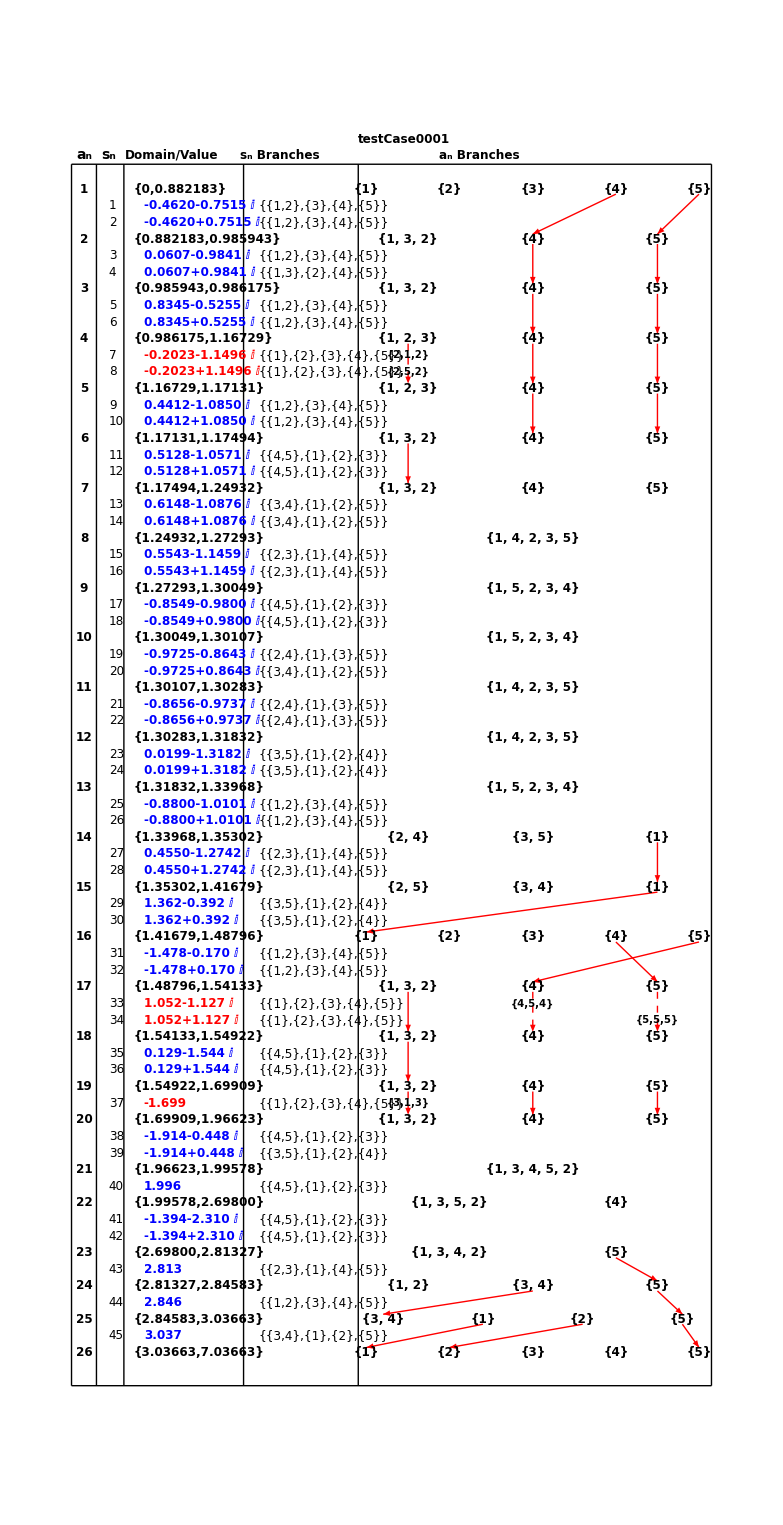

```mathematica
annularMonodromyOffSet=4;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.5,20.5},{5.5,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{annularMonodromyOffSet,0}],
Graphics@Translate[poleLinkGraphics,{annularMonodromyOffSet,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

### Section 8.11: Create Annular continuation diagram for testCase0017

#### Section 8.1.1: Set up annulus numbers

```mathematica
(*
 do the annulus numbers
*)
agIndex=1/3;
sgIndex=1/3;
yOffSet=20;
annuliLoc={};
annulusIndexGraphics={};
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
AppendTo[annuliLoc,{k,yOffSet}];
AppendTo[annulusIndexGraphics,Inset[Style[ToString[annulusTable[[aIndex,1]]],12,Black,Bold],{0,yOffSet}]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
yOffsetFinal=yOffSet
annuliLoc
```

44/3

{{1,20},{2,19},{3,18},{4,17},{5,49/3},{6,46/3}}

#### Section 8.1.2: Setup annular regions

k: 1 domain: {0.,0.5}

k: 2 domain: {0.5,0.624261}

k: 3 domain: {0.624261,0.954195}

k: 4 domain: {0.954195,1.33333}

k: 5 domain: {1.33333,1.7028}

46/3

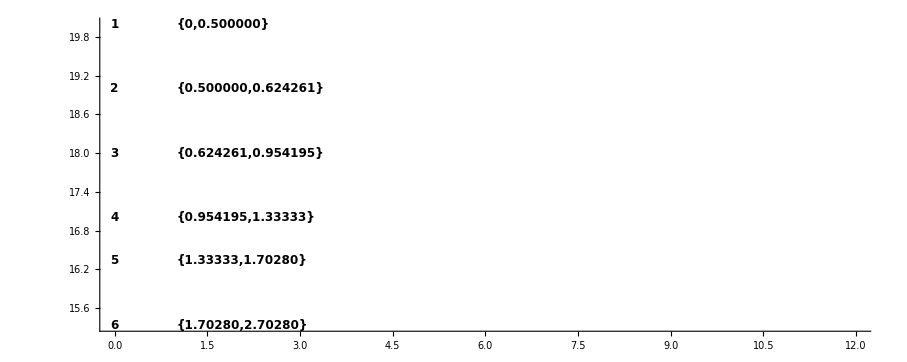

```mathematica
annuliGraphics={};

yOffSet=20;
For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["k: ",k," domain: ",N[annulusTable[[aIndex,3]]]];
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[aIndex,3]],6],12,Black,Bold],{0,yOffSet},Left]];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;
];
(* print last annulus
*)
AppendTo[annuliGraphics,Inset[Style[AccountingForm@N[annulusTable[[-1,3]],6],12,Black,Bold],{0,yOffSet},Left]];
yOffSet
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.1.3: Set up singular points

Annulus 4 has a pole link

annulus monodromy: {{1,3,2}}

pole links: {{8,1,3,1}}

nextPoleLink: nextPoleLink

Processing pole link {8,1,3,1}

Annulus branch sheet: 1

annulusBranchIndex: 1

Singular point: 8

Sing pole links: {1,3,1}

y-offset for this sing: 50/3

Pole: 1.333

poleLinkGraphicsData: {{4,8,50/3,1,{1,3,1}}}

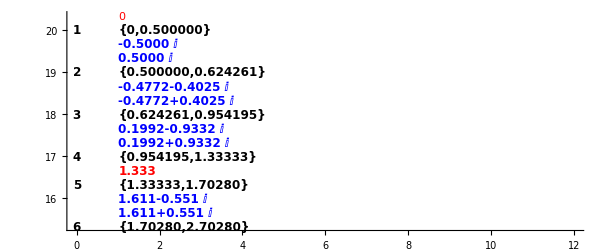

```mathematica
singularLoc={};
singularPointGraphics={};
yOffSet=20;

(* do singular point at zero if necessary *)
If[annulusTable[[1,1]]==" ",
(* do singular point in blue *)
AppendTo[singularPointGraphics,Inset[Style[annulusTable[[1,3]]],{0,yOffSet+sgIndex},Left]];
];

poleLinkGraphicData={};
For[k=1,k<=(Length@theAnnuli)-1,k++,
(*
 check if this annulus has a pole link
*)
If[MemberQ[newPoleLinkTable[[All,1]],k],
Print["Annulus ",k," has a pole link"];
{aIndex2,sIndex2}=getSingTableIndexes[annulusTable,k];
theCurrentMonodromy=annulusTable[[aIndex2,6]];
Print["  annulus monodromy: ",theCurrentMonodromy];
poleLinkPos=Position[newPoleLinkTable[[All,1]],x_/;x==k][[1,1]];
thePoleLinks=Sort[newPoleLinkTable[[poleLinkPos,2]],#1[[1]]<#2[[1]]&];
Print["   pole links: ",thePoleLinks];

For[k2=1,k2<=Length@thePoleLinks,k2++,

Print["nextPoleLink: ",nextPoleLink];
Print["     Processing pole link ",thePoleLinks[[k2]]];
Print["      Annulus branch sheet: ",thePoleLinks[[k2,2]]];
annulusBranchIndex=Position[theCurrentMonodromy,x_/;x==thePoleLinks[[k2,2]]][[1,1]];
Print["       annulusBranchIndex: ",annulusBranchIndex];
singPole=thePoleLinks[[k2,1]];
poleData=thePoleLinks[[k2,2;;]];
Print["       Singular point: ",singPole];
Print["       Sing pole links: ",poleData];
singYOffset=yOffSet-k2 sgIndex;
Print["       y-offset for this sing: ",singYOffset];
AppendTo[poleLinkGraphicData,{k,singPole,singYOffset,annulusBranchIndex,poleData}];
];



];


{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];

If[MemberQ[$poleIndexes,singIndexes[[j]]],
Print["Pole: ",Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold]];
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Red,Bold],{0,yOffSet},Left]];
,
AppendTo[singularPointGraphics,Inset[Style[NumberForm[N[annulusTable[[sIndex[[j]],3]],4]],12,Blue,Bold],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];

(* print last annulus
*)
Print["poleLinkGraphicsData: ",poleLinkGraphicData];
Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1,0}]},Axes->True,PlotRange->{{0,12},All}]
```

#### Section 8.1.4: Set up singular indexes

sIndex: {3,4}

sIndex: {6,7}

sIndex: {9,10}

sIndex: {12}

sIndex: {14,15}

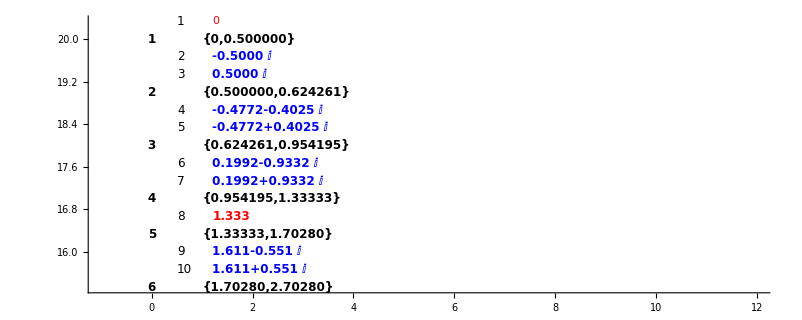

```mathematica
(*
 do the singular indexes
*)
singularPointIndexGraphics={};

yOffSet=20;
(*
 first do singular point at origin if needed
*)
If[$theSingularList[[1]]==0,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[1],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["sIndex: ",sIndex];
For[j=1,j<=Length@sIndex,j++,
yOffSet-=sgIndex;
singIndexes=ringMemberSingularIndexes[[k]];
If[MemberQ[$poleIndexes,singIndexes[[j]]],
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
,
AppendTo[singularPointIndexGraphics,Inset[Style[ToString[annulusTable[[sIndex[[j]],2]]],12],{0,yOffSet},Left]];
];
];
yOffSet-=agIndex;
];
(* print last annulus
*)


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}]},PlotRange->{{-1,12},All},Axes->True]
```

#### Section 8.1.5: Set up singular monodromies

```mathematica
(*
 do singular monodromies
*)
sData=Import[singularMonodromyFileName[$theTestCase]];
singularMonodromies=sData[[1]];
MapThread[{#1,#2,#3}&,{Range[Length@$theSingularList],singularMonodromies,$minRadiusArray//N}]//MatrixForm

 

yOffSet=20;
(*
 first do singular point at origin if needed
*)
singularPointMonodromyGraphics={};
If[$theSingularList[[1]]==0,
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@singularMonodromies[[1]],12],{0,yOffSet+sgIndex},Left]];
];

For[k=1,k<=(Length@theAnnuli)-1,k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
For[j=1,j<=Length@sIndex,j++,
singIndexes=ringMemberSingularIndexes[[k]];
yOffSet-=sgIndex;
AppendTo[singularLoc,{singIndexes[[j]],yOffSet}];
Print["the sing monodromy: ",Style[annulusTableR[[sIndex[[j]],6]],12]];
AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];

(*AppendTo[singularPointMonodromyGraphics,Inset[Style[ToString@annulusTableR[[sIndex[[j]],6]],12],{0,yOffSet},Left]];*)

];
yOffSet-=agIndex;
];


Show[{Graphics@annulusIndexGraphics,Graphics@Translate[annuliGraphics,{1,0}],Graphics@Translate[singularPointGraphics,{1.2,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],Graphics@Translate[singularPointMonodromyGraphics,{4,0}]},PlotRange->{{-1,12},All},Axes->True]
```

(1 | {{1},{2},{3}} | 0.166667
2 | {{2,3},{1}} | 0.158927
3 | {{2,3},{1}} | 0.158927
4 | {{2,3},{1}} | 0.162353
5 | {{2,3},{1}} | 0.162353
6 | {{1,2},{3}} | 0.158927
7 | {{1,2},{3}} | 0.158927
8 | {{1},{2},{3}} | 0.205603
9 | {{2,3},{1}} | 0.205603
10 | {{1,3},{2}} | 0.205603)

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{2,3},{1}}

«1 more identical outputs»

the sing monodromy: {{1,2},{3}}

the sing monodromy: {{1,2},{3}}

the sing monodromy: {{1},{2},{3}}

the sing monodromy: {{2,3},{1}}

the sing monodromy: {{1,3},{2}}

-Graphics-

#### Section 8.1.6: Set up annular monodromies

```mathematica
(*
 do annular monodromies
*)
xLocationSave={};
annuliMonodromyGraphics={};
yOffSet=20;
maxWidth=10;
netMax=0;
For[k=1,k<=(Length@theAnnuli),k++,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,k];
Print["Monodromy: ",annulusTable[[aIndex,6]]];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];
AppendTo[xLocationSave,{k,yOffSet,locations}];
Print["x-locations: ",locations];
maxX=locations[[-1]];
If[maxX>netMax,
netMax=maxX;
];
For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[aIndex,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
For[i=1,i<=Length@sIndex,i++,
yOffSet-=sgIndex;
];
yOffSet-=agIndex;

];
(*
 now do last annulus 
*)

(*{aIndex,sIndex}=getSingTableIndexes[annulusTable,Length@theAnnuli];

numBranches=Length@annulusTable[[aIndex,6]];
locations=(Array[#&,numBranches+2,{0,maxWidth}])[[2;;-2]];

For[j=1,j<=numBranches,j++,
AppendTo[annuliMonodromyGraphics,Inset[Style[ToString[annulusTable[[-1,6,j]]],12,Black,Bold],{locations[[j]],yOffSet},Center]];
];
Print["netMax: ",netMax]
*)
```

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1,3,2}}

x-locations: {5}

Monodromy: {{1},{2},{3}}

x-locations: {5/2,5,15/2}

#### Section 8.1.7: Set up pole link graphics

```mathematica
poleLinkGraphicData//MatrixForm
xLocationSave//MatrixForm
poleLinkGraphics={};
For[i=1,i<=Length@poleLinkGraphicData,i++,
currentAnnulus=poleLinkGraphicData[[i,1]];
singIndex=poleLinkGraphicData[[i,2]];
currentBranchIndex=poleLinkGraphicData[[i,4]];
Print["  currentBranchIndex: ",currentBranchIndex];
Print["    currentAnnulus: ",currentAnnulus];
Print["    current sing index: ",singIndex];
xLocationPos=Position[xLocationSave[[All,1]],x_/;x==currentAnnulus][[1,1]];
Print["  xLocationPos: ",xLocationPos];
Print["  xLocationData: ",xLocationSave[[xLocationPos]]];
xLoc=xLocationSave[[xLocationPos,3,currentBranchIndex]];
Print["  xLocation for this link: ",xLoc];
yLoc=poleLinkGraphicData[[i,3]];
Print["  yLocation for this link: ",yLoc];
Print["  pole link string: ",poleLinkGraphicData[[i,5]]];
AppendTo[poleLinkGraphics,Inset[Style[poleLinkGraphicData[[i,5]],10,Black,Bold],{xLoc,yLoc}]];

]
```

(4 | 8 | 50/3 | 1 | {1,3,1})

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5}
4 | 17 | {5}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2})

currentBranchIndex: 1

currentAnnulus: 4

current sing index: 8

xLocationPos: 4

xLocationData: {4,17,{5}}

xLocation for this link: 5

yLocation for this link: 50/3

pole link string: {1,3,1}

#### Section 8.1.8: Create the continuation diagram

```mathematica
continuationRecords=Select[annulusTable,#[[8]]!={}&];
continuationRecords[[All,{1,8}]]//MatrixForm
contLinks=continuationRecords[[All,{1,8}]];

(*
 may need to set currentContLinAIndex to 2
*)

currentContAIndex=1;

currentContLink=contLinks[[currentContAIndex]]
xLocationSave//MatrixForm
{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]]
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1]
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];
currentBranchLink=1;
currentPreBranch=currentContLink[[2,currentBranchLink,1]];
currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]]
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]]
(*
 now create arror points
*)
preLocationNum=currentContLink[[1]]
postLocationNum=preLocationNum+1
preYVal=xLocationSave[[preLocationNum,2]]
postYVal=xLocationSave[[preLocationNum+1,2]]

preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]]
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]]

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
```

(1 | {{{1},{1}}}
4 | {{{1,3,2},{1,3,2}}})

{1,{{{1},{1}}}}

(1 | 20 | {5/2,5,15/2}
2 | 19 | {5/2,5,15/2}
3 | 18 | {5}
4 | 17 | {5}
5 | 49/3 | {5}
6 | 46/3 | {5/2,5,15/2})

{2,{3,4}}

preMonodromy: {{1},{2},{3}}

{5,{6,7}}

postMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

1

1

1

2

20

19

5/2

5/2

0.1

#### Section 8.1.9: Create pole records

```mathematica
poleRecords=Select[continuedAnnuliRecords,#[[8]]==True&];
poleRecordsGrid=Grid[Prepend[poleRecords,{"a_n","Branch","Sheet","s_n",Column[{"Impinging","Branch","name"}],Column[{"Impinging","Branch"}],Column[{"Impinging","sheet"}],Column[{"Impinging","pole","status"}],Column[{"Post","branch"}],Column[{"Post","sheet"}],Column[{"Same","Cycle","flag"}]}],Dividers->{{{True}},{True,True,{False},True}}]
```

a_n | Branch | Sheet | s_n | Impinging
Branch
name | Impinging
Branch | Impinging
sheet | Impinging
pole
status | Post
branch | Post
sheet | Same
Cycle
flag
4 | {1,3,2} | 1 | 8 | L_-1 | {3} | 3 | True | {1,3,2} | 1 | True

#### Section 8.1.10: Create continuation arrows

```mathematica
contLinks=continuationRecords[[All,{1,8}]];
dy=0.1;
arrowTranslationFactor=3.5 (* default *)
arrowTranslationFactor=2;
arrowTable=Table[

currentContLink=contLinks[[currentContAIndex]];
Print["currentAnnulus: ",currentContLink[[1]]];
theCurrentAnnulus=currentContLink[[1]];
Print["currentContLink: ",currentContLink[[1]]];

{preAIndex,preSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]];
preMonodromy=annulusTable[[preAIndex,6]];
Print["preMonodromy: ",preMonodromy];
{postAIndex,postSIndex}=getSingTableIndexes[annulusTable,currentContLink[[1]]+1];
postMonodromy=annulusTable[[postAIndex,6]];
Print["postMonodromy: ",postMonodromy];

Print["postMonodromy: ",annulusTable[[postAIndex,6]]];

currentPreBranch=currentContLink[[2,currentBranchLink,1]];
Print["currentPreBranch: ",currentPreBranch];
theCurrentPreBranch=currentPreBranch;

currentPreBranchLoc=Position[preMonodromy,x_/;x==currentPreBranch][[1,1]];
currentPostBranch=currentContLink[[2,currentBranchLink,2]];
currentPostBranchLoc=Position[postMonodromy,x_/;x==currentPostBranch][[1,1]];
(*
 now create arror points
*)
Print["testa"];
preLocationNum=currentContLink[[1]];
postLocationNum=preLocationNum+1;
preYVal=xLocationSave[[preLocationNum,2]];
postYVal=xLocationSave[[preLocationNum+1,2]];
Print["testb"];
preXVal=xLocationSave[[preLocationNum,3,currentPreBranchLoc]];
postXVal=xLocationSave[[postLocationNum,3,currentPostBranchLoc]];

If[MemberQ[poleRecords[[All,{1,2}]],{theCurrentAnnulus,theCurrentPreBranch}],
(*If[MemberQ[poleRecords[[All,1]],theCurrentAnnulus] && MemberQ[poleRecords[[All,2]],theCurrentPreBranch],*)
Print[Style["Creating dashed arrow",Red]];
Print["     current pre branch: ",theCurrentPreBranch];
{Arrowheads[0.015],Red,Dashed,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
,
{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]}
],
(*Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3.5,0}],*)
{currentContAIndex,1,Length@contLinks},
{currentBranchLink,1,Length@contLinks[[currentContAIndex,2]]}
];
```

3.5

currentAnnulus: 1

currentContLink: 1

preMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

postMonodromy: {{1},{2},{3}}

currentPreBranch: {1}

testa

testb

currentAnnulus: 4

currentContLink: 4

preMonodromy: {{1,3,2}}

postMonodromy: {{1,3,2}}

postMonodromy: {{1,3,2}}

currentPreBranch: {1,3,2}

testa

testb

Creating dashed arrow

current pre branch: {1,3,2}

#### Section 8.1.8: Create continuation graphics

11.25

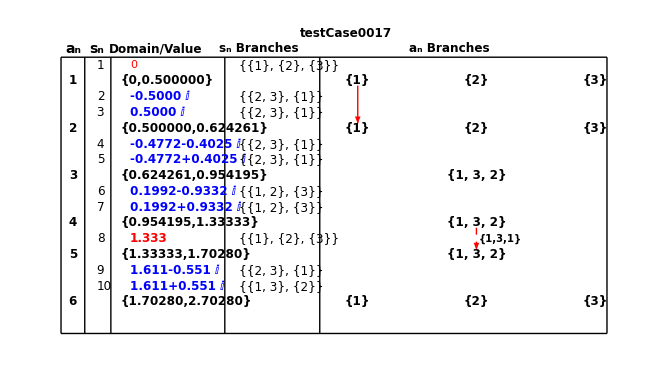

```mathematica
annularMonodromyOffSet=3.5;
rightVerticalX=annularMonodromyOffSet+netMax+1/4
centerX=(rightVerticalX+0.25)/2;

  topHorizLine=Graphics@Line[{{-.25,20.5},{rightVerticalX,20.5}}];
bottomHorizLine=Graphics@Line[{{-.25,yOffsetFinal},{rightVerticalX,yOffsetFinal}}];
vLine1=Graphics@Line[{{-.25,20.5},{-.25,yOffsetFinal}}];
vLine2=Graphics@Line[{{0.25,20.5},{0.25,yOffsetFinal}}];
vLine3=Graphics@Line[{{0.8,20.5},{0.8,yOffsetFinal}}];
vLine4=Graphics@Line[{{3.2,20.5},{3.2,yOffsetFinal}}];
vLine5=Graphics@Line[{{5.2,20.5},{5.2,yOffsetFinal}}];
vLine6=Graphics@Line[{{rightVerticalX,20.5},{rightVerticalX,yOffsetFinal}}];

text1=Graphics@Text[Style["a_n",14,Bold,Black],{0,20.68}];
text2=Graphics@Text[Style["s_n",14,Bold,Black],{0.5,20.68}];
text3=Graphics@Text[Style["Domain/Value",12,Bold,Black],{1.75,20.68}];
text4=Graphics@Text[Style["s_n Branches",12,Bold,Black],{3.92,20.68}];
text5=Graphics@Text[Style["a_n Branches",12,Bold,Black],{7.93,20.68}];
 (*
 do arrows
*)
(*poleLinkData//MatrixForm
(*a1=Graphics@{Arrowheads[0.015],Red,Arrow[{{6.37,17.12},{6.37,16.57}}]};*)
p1Cont=Graphics@{Text[Style[poleLinkData[[1,2;;]],10],{6.545,16.7},{-1,0}]};

a2=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,17.12},{9.67,16.57}}]};
p2Cont=Graphics@{Text[Style[poleLinkData[[2,2;;]],10],{9.87,16.98},{-1,0}]};

a3=Graphics@{Arrowheads[0.015],Red,Arrow[{{9.67,16.14},{9.67,15.51}}]};

dy=0.1
a1=Graphics@Translate[{Arrowheads[0.015],Red,Arrow[{{preXVal,preYVal-dy},{postXVal,postYVal+dy}}]},{3,0}];
*)



gFile=Show[{Graphics@annulusIndexGraphics,
Graphics@Translate[annuliGraphics,{1,0}],
Graphics@Translate[singularPointGraphics,{1.2,0}],
Graphics@Translate[singularPointMonodromyGraphics,{3.5,0}],Graphics@Translate[annuliMonodromyGraphics,{annularMonodromyOffSet,0}],Graphics@Translate[singularPointIndexGraphics,{1/2,0}],topHorizLine,bottomHorizLine,
(*hline1,*)text1,text2,text3,text4,text5,vLine1,vLine2,vLine3,vLine4,vLine5,vLine6,
Graphics@Translate[arrowTable,{3.5,0}],
Graphics@Translate[poleLinkGraphics,{4,0}],Graphics@Inset[Style[$theTestCase,12,Black,Bold],{centerX,21}]}]
```

## Section 9: Create files needed by ch8 notebook

This section creates the following files used by the chapter 8 notebook:
annularTableWithBranchlinks.m
finalContinuationData.m
finalBranchGrid.m

### Section 9.1: Export annular table with branch links to file annularTableWithBranchLinks.m

```mathematica
(*
 export annular table with branch links to file for Chapter 8
*)
Print["Exporting "<>annularTableWithBranchLinksFileName[$theTestCase]];
Export[annularTableWithBranchLinksFileName[$theTestCase],gFile];
```

Exporting D:\algFunctionBook\data\testCase0017\annularTableWithBranchLinks.m

### Section 9.2: Export final continuation data to file finalContinuationData.m

#### Section 9.2.1: Set up ring domain indexes

```mathematica
Length@ringSizes
If[Abs[$theSingularList[[1]]]>10^(-75),
(*
 prepend zero to annular domains
*)
theRingDomainIndex=MapThread[{#1,#2}&,{Range[Length@ringSizes+2],Join[{0},ringSizes,{∞}]}];
,
theRingDomainIndex=MapThread[{#1,#2}&,{Range[Length@ringSizes+1],Join[ringSizes,{∞}]}];
];
Grid[theRingDomainIndex//N]
```

6

1. | 0.
2. | 0.5
3. | 0.624261
4. | 0.954195
5. | 1.33333
6. | 1.7028
7. | ∞

#### Section 9.2.2: Set up branch regions

```mathematica
branchRegions= Table[
{aIndex,sIndex}=getSingTableIndexes[annulusTable,i];
theMonodromy=annulusTable[[aIndex,6]];
Table[
{theMonodromy[[j]],theAnnuli[[i]],0,{i,i+1}},
{j,1,Length@theMonodromy}
]
,
{i,1,Length@theAnnuli}

];
branchRegions//N//MatrixForm

  For[theCurrentRing=Length@theAnnuli,theCurrentRing≥2,theCurrentRing--,
(* For[theCurrentRing=Length[branchRegions],theCurrentRing≥2,theCurrentRing--,  *)
Print[Style["processing ring: ",Red],theCurrentRing];
{currentRingIndex,currentSingularIndex}=getSingTableIndexes[annulusTable,theCurrentRing];
{previousRingIndex,previousSingularIndex}=getSingTableIndexes[annulusTable,theCurrentRing-1];
(* first get list of branch cycles on thie ring *)
currentBranchCycles=annulusTable[[currentRingIndex,6]];
previousBranchCycles=annulusTable[[previousRingIndex,6]];
(* check if any cycles are continued *)
branchContinuations=annulusTable[[previousRingIndex,8]];
Print["test1"];
If[branchContinuations≠{},
For[j=1,j≤Length[branchContinuations],j++,
currentContinuation=branchContinuations[[j]];
preBranch=currentContinuation[[1]];
postBranch=currentContinuation[[2]];
preBranchpos=Position[branchRegions[[theCurrentRing-1,All,1]],preBranch]//Flatten//First;
postBranchpos=Position[branchRegions[[theCurrentRing,All,1]],postBranch]//Flatten//First;
poleFlag=False;
(*
 need to process meromorphic continuation here
*)
Print["preBranch: ",preBranch];
Print["the previous Ring: ",theCurrentRing-1];
Print["postBranch: ",postBranch];
(*
 need to process meromorphic continuation here
*)
Print["preBranch: ",preBranch];
Print["the previous Ring: ",theCurrentRing-1];
Print["postBranch: ",postBranch];
If[MemberQ[poleRecords[[All,1]],theCurrentRing-1],
pos=Position[poleRecords[[All,1]],x_/;x==theCurrentRing-1];
Print["pos: ",Flatten@pos];
If[MemberQ[poleRecords[[Flatten@pos,2]],preBranch],
Print["Found preBranch in theCurrentRing-1"];
poleFlag=True;
];
];


(*If[MemberQ[poleRecords[[All,1]],theCurrentRing-1] && MemberQ[poleRecords[[All,2]],preBranch],
Print["  This annular index and branch is in pole records"];
poleFlag=True;
];
*)
(* first check if this branch has already been updated if so use updated range *)
If[!poleFlag,
If[branchRegions[[theCurrentRing,postBranchpos,3]]==0,
(*branchRegions[[theCurrentRing-1,preBranchpos,2,2]]=theContinuationList3[[currentRingIndex,2,2]];*)
branchRegions[[theCurrentRing-1,preBranchpos,2,2]]=annulusTable[[currentRingIndex,3,2]];
(* now set the update flag for this branch *)
branchRegions[[theCurrentRing-1,preBranchpos,3]]=1;
branchRegions[[theCurrentRing-1,preBranchpos,4,2]]=theCurrentRing+1;
,
(* now use updated range*)
branchRegions[[theCurrentRing-1,preBranchpos,2,2]]=branchRegions[[theCurrentRing,postBranchpos,2,2]];
branchRegions[[theCurrentRing-1,preBranchpos,3]]=1;
branchRegions[[theCurrentRing-1,preBranchpos,4,2]]=branchRegions[[theCurrentRing,postBranchpos,4,2]];
];
(* now mark the post branch from the branch lists as deleted *)
branchRegions[[theCurrentRing,postBranchpos,3]]=Missing[];
];
];
];
 branchRegions[[theCurrentRing]]=DeleteMissing[branchRegions[[theCurrentRing]],1,2];
];
Print["branchRegions: ",branchRegions//N//MatrixForm]
```

({{{1.},{0.,0.5},0.,{1.,2.}},{{2.},{0.,0.5},0.,{1.,2.}},{{3.},{0.,0.5},0.,{1.,2.}}}
{{{1.},{0.5,0.624261},0.,{2.,3.}},{{2.},{0.5,0.624261},0.,{2.,3.}},{{3.},{0.5,0.624261},0.,{2.,3.}}}
{{{1.,3.,2.},{0.624261,0.954195},0.,{3.,4.}}}
{{{1.,3.,2.},{0.954195,1.33333},0.,{4.,5.}}}
{{{1.,3.,2.},{1.33333,1.7028},0.,{5.,6.}}}
{{{1.},{1.7028,5.7028},0.,{6.,7.}},{{2.},{1.7028,5.7028},0.,{6.,7.}},{{3.},{1.7028,5.7028},0.,{6.,7.}}})

processing ring: 6

test1

processing ring: 5

test1

preBranch: {1,3,2}

the previous Ring: 4

postBranch: {1,3,2}

preBranch: {1,3,2}

the previous Ring: 4

postBranch: {1,3,2}

pos: {1}

Found preBranch in theCurrentRing-1

processing ring: 4

test1

processing ring: 3

test1

processing ring: 2

test1

preBranch: {1}

the previous Ring: 1

postBranch: {1}

preBranch: {1}

the previous Ring: 1

postBranch: {1}

branchRegions: ({{{1.},{0.,0.624261},1.,{1.,3.}},{{2.},{0.,0.5},0.,{1.,2.}},{{3.},{0.,0.5},0.,{1.,2.}}}
{{{2.},{0.5,0.624261},0.,{2.,3.}},{{3.},{0.5,0.624261},0.,{2.,3.}}}
{{{1.,3.,2.},{0.624261,0.954195},0.,{3.,4.}}}
{{{1.,3.,2.},{0.954195,1.33333},0.,{4.,5.}}}
{{{1.,3.,2.},{1.33333,1.7028},0.,{5.,6.}}}
{{{1.},{1.7028,5.7028},0.,{6.,7.}},{{2.},{1.7028,5.7028},0.,{6.,7.}},{{3.},{1.7028,5.7028},0.,{6.,7.}}})

#### Section 9.2.3: Create final continuation list

```mathematica
(*
 theFinalContinuationList is the array which holds the analytically-continued domains of all annular branches
*)
theFinalContinuationList={};
For[i=1,i<=Length@theAnnuli,i++,
(*Print["branchRegion: ",branchRegions[[i]]//N];*)
If[branchRegions[[i]]!={},
AppendTo[theFinalContinuationList,{i,branchRegions[[i,All,{1,2,4}]]}];
,
AppendTo[theFinalContinuationList,{i,{}}];
];
];
Grid[theFinalContinuationList//N,Alignment->Left]
```

1. | {{{1.},{0.,0.624261},{1.,3.}},{{2.},{0.,0.5},{1.,2.}},{{3.},{0.,0.5},{1.,2.}}}
2. | {{{2.},{0.5,0.624261},{2.,3.}},{{3.},{0.5,0.624261},{2.,3.}}}
3. | {{{1.,3.,2.},{0.624261,0.954195},{3.,4.}}}
4. | {{{1.,3.,2.},{0.954195,1.33333},{4.,5.}}}
5. | {{{1.,3.,2.},{1.33333,1.7028},{5.,6.}}}
6. | {{{1.},{1.7028,5.7028},{6.,7.}},{{2.},{1.7028,5.7028},{6.,7.}},{{3.},{1.7028,5.7028},{6.,7.}}}

#### Section 9.2.4: Export final continuation tables to file

```mathematica
Grid[theFinalContinuationList//N,Alignment->Left]
theRingDomainIndex//N//MatrixForm

Print["Exporting "<>finalContinuationDataFileName[$theTestCase]];
Export[finalContinuationDataFileName[$theTestCase],{theFinalContinuationList,theRingDomainIndex}]

annularExtensions={#[[1]],#[[2,All,{1,3}]]}&/@ theFinalContinuationList;
Grid[Prepend[annularExtensions,{"a_n","{{Branch,{r_a,r_b}}"}],Dividers->{{{True}},{True,True,{False},True}},Alignment->Left]
```

1. | {{{1.},{0.,0.624261},{1.,3.}},{{2.},{0.,0.5},{1.,2.}},{{3.},{0.,0.5},{1.,2.}}}
2. | {{{2.},{0.5,0.624261},{2.,3.}},{{3.},{0.5,0.624261},{2.,3.}}}
3. | {{{1.,3.,2.},{0.624261,0.954195},{3.,4.}}}
4. | {{{1.,3.,2.},{0.954195,1.33333},{4.,5.}}}
5. | {{{1.,3.,2.},{1.33333,1.7028},{5.,6.}}}
6. | {{{1.},{1.7028,5.7028},{6.,7.}},{{2.},{1.7028,5.7028},{6.,7.}},{{3.},{1.7028,5.7028},{6.,7.}}}

(1. | 0.
2. | 0.5
3. | 0.624261
4. | 0.954195
5. | 1.33333
6. | 1.7028
7. | ∞)

Exporting D:\algFunctionBook\data\testCase0017\finalContinuationData.m

D:\algFunctionBook\data\testCase0017\finalContinuationData.m

a_n | {{Branch,{r_a,r_b}}
1 | {{{1},{1,3}},{{2},{1,2}},{{3},{1,2}}}
2 | {{{2},{2,3}},{{3},{2,3}}}
3 | {{{1,3,2},{3,4}}}
4 | {{{1,3,2},{4,5}}}
5 | {{{1,3,2},{5,6}}}
6 | {{{1},{6,7}},{{2},{6,7}},{{3},{6,7}}}

### Section 9.3: Export final branch grid to file finalBranchGrid.m

```mathematica
(*
 fourth version to check infty R2 cases and when s1 is not a singular point
*)
If[FileExistsQ[finalContinuationDataFileName[$theTestCase]],
   {theFinalContinuationList,theRingDomainIndex}=Import[finalContinuationDataFileName[$theTestCase]];
absSing=Abs@$theSingularList;

extendedDomain=Table[
If[aIndex==1 && Abs[$theSingularList[[1]]]<10^-50,
Print["s1 is zero"];
];
branchList=Table[
monodromy=theFinalContinuationList[[aIndex,2,monIndex,1]];
extDomain=theFinalContinuationList[[aIndex,2,monIndex,2]]//N;
ringRange=theFinalContinuationList[[aIndex,2,monIndex,3]];
If[aIndex==1 && Abs[$theSingularList[[1]]]>10^-50,
highSingIndex=(Position[absSing,x_/;Abs[x-extDomain[[2]]]<10^-5]//Flatten)[[1]];
theGridBox=GridBox[{{Style[theFinalContinuationList[[aIndex,2,monIndex,1]],Bold]},{{0,Subscript[s, highSingIndex]}}}]//DisplayForm;
lowSingIndex=0;
,
lowSingIndex=(Position[absSing,x_/;Abs[x-extDomain[[1]]]<10^-5]//Flatten)[[1]];
(*Print["aIndex: ",aIndex," low sing index: ",lowSingIndex];*)
(*If[aIndex!=Length@theFinalContinuationList,*)
If[ringRange[[2]]!=Length@branchRegions+1,
highSingIndex=(Position[absSing,x_/;Abs[x-extDomain[[2]]]<10^-5]//Flatten)[[1]];
(*Print["aIndex: ",aIndex," high sing val: ",highSingIndex];*)
,
highSingIndex=∞;
];
theGridBox=GridBox[{{Style[theFinalContinuationList[[aIndex,2,monIndex,1]],Bold]},{{Subscript[s, lowSingIndex],Subscript[s, highSingIndex]}}}]//DisplayForm;
];
theGridBox,
{monIndex,1,Length@theFinalContinuationList[[aIndex,2]]}
];
{aIndex,branchList},
(*{aIndex,1,14}*)
{aIndex,1,Length@theFinalContinuationList}

];
finalBranchGrid= Grid[Prepend[extendedDomain,{Style["a_i",Bold,Black],Style["Branch Domains",Bold,Black]}],Spacings->{1,1.5},(*Background->White,*)Dividers->{{{True}},{True,True,{False},True}},Alignment->Center];
Print[finalBranchGrid];

(*
Import final branch grid to finalBranchGrid.m
*)
Print["Exporting "<>finalBranchGridReportFileName[$theTestCase]];
Export[finalBranchGridReportFileName[$theTestCase],finalBranchGrid];
,
Print[Style[finalContinuationDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

s1 is zero

a_i | Branch Domains
1 | {{1}
{s_1,s_4},{2}
{s_1,s_2},{3}
{s_1,s_2}}
2 | {{2}
{s_2,s_4},{3}
{s_2,s_4}}
3 | {{1,3,2}
{s_4,s_6}}
4 | {{1,3,2}
{s_6,s_8}}
5 | {{1,3,2}
{s_8,s_9}}
6 | {{1}
{s_9,s_∞},{2}
{s_9,s_∞},{3}
{s_9,s_∞}}

Exporting D:\algFunctionBook\data\testCase0017\finalBranchGrid.m

## Section 10: Plot annular branches in extended domains

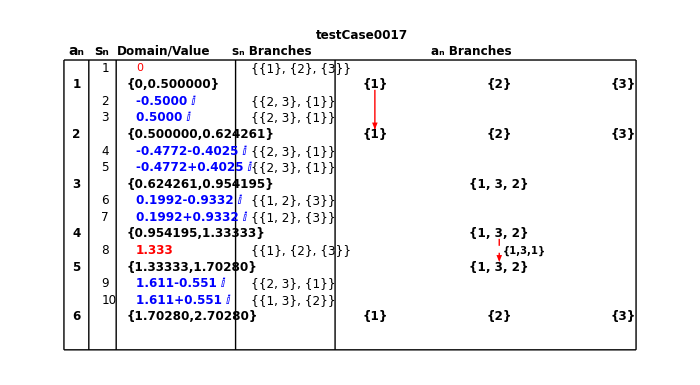

```mathematica
Show[gFile,ImageSize->700]
```

```mathematica
(* Note branch positions in the finalBranchGrid are not the same position as in the annular table due to analytic continuation.  Plots are based on position in the finalBranchGrid *)

finalBranchGrid= Style[Grid[Prepend[extendedDomain,{Style["a_i",Bold,Black],Style["Branch Domains",Bold,Black]}],Spacings->{1,1.5},Dividers->{{{True}},{True,True,{False},True}},Alignment->Center],10]
```

a_i | Branch Domains
1 | {{1}
{s_1,s_4},{2}
{s_1,s_2},{3}
{s_1,s_2}}
2 | {{2}
{s_2,s_4},{3}
{s_2,s_4}}
3 | {{1,3,2}
{s_4,s_6}}
4 | {{1,3,2}
{s_6,s_8}}
5 | {{1,3,2}
{s_8,s_9}}
6 | {{1}
{s_9,s_∞},{2}
{s_9,s_∞},{3}
{s_9,s_∞}}

```mathematica
(* select annular domain and branch position in finalBranchGrid *)
selectedAnnulus=1;
selectedBranch=1;


annularExtensions={#[[1]],#[[2,All,{1,2,3}]]}&/@ theFinalContinuationList;

theAnnulusTable=annulusTable;
If[selectedAnnulus>Length@annularExtensions || selectedBranch>Length@annularExtensions[[selectedAnnulus,2]],
Print[Style["Selected branch or annulus out of range",Red]];
,
theBranchSet=getExtendedBranchPlot[theAnnulusTable,Re,selectedAnnulus,selectedBranch,$thetaV,annularExtensions,"radialSegments"->25,"arcSegments"->50];

 branchPlot=Table[
rowA=theBranchSet[[k]]//N;
rowB=theBranchSet[[k+1]]//N;
pTable=Table[{Darker@Green,Opacity[0.25],Polygon[{rowA[[j]],rowA[[j+1]],rowB[[j+1]],rowB[[j]]}]},{j,1,(Length@rowA)-1}];pTable,
{k,1,(Length@theBranchSet)-1}
];
theBranchPlot= Show[Graphics3D@{branchPlot},BoxRatios->{1,1,1},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style["Re",14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300(*PlotRange->{Automatic,Automatic,{-1,5}}*)];

thePlotRange=PlotRange[theBranchPlot];
Print[theBranchPlot];
];
```

selectedMonodromy: {1}

annularExtensions record: {1.,{{{1.},{0.,0.624261},{1.,3.}},{{2.},{0.,0.5},{1.,2.}},{{3.},{0.,0.5},{1.,2.}}}}

domainIndexes: {1,3}

annularExtensionBranches: {{1},{2},{3}}

branchPosition: 1

extendedDomain: {0.,0.624261}

extended domain indexes: {1,3}

domain flag: True

domain extension block

oldNorm: 0.25

newMedialRadius: 0.312130599

rStart: 0.25

rEnd: 0.312131

radial domain: {{0.25,0.312131}}

aax

test1

test2

-Graphics3D-

## Initialization Cell:

### Initialize variables

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]

<<ComputationalGeometry`
$HistoryLength=0;

If[!MemberQ[$ContextPath,"algContext`"],
algContext`$userDirectory="D:\\puiseuxSeries";
algContext`z;
algContext`w;
algContext`c;
algContext`s;
algContext`r;
algContext`$workingPrecision=1000;
algContext`$separationFactor;
algContext`$maxRootVerifyDistance=10^-50;
algContext`$accuracyComparisonFactor=20;
algContext`$ringDelta=1/10000;
algContext`$continuationStiffnessSwitching=False;
algContext`$continuationDiagFlagA=False;
algContext`$continuationDiagFlagB=False;
algContext`$continuationDiagFlagC=False;
algContext`$thetaV=Pi/6;
algContext`$radialSegments=13;
algContext`$arcSegments=48;
 algContext`$puiseuxBaseValuesDiagFlag=False;
algContext`$continuationLegDiagFlag=True;
algContext`$getMatchValueDiagFlag=False;
 PrependTo[$ContextPath,"algContext`"];
];


(*totalIntegrationSteps=1500000;
maxStepSize=0.0001;
workingPrecision=75;

ringDelta=1/20000; (* ring separation threshold *)
minRingSize=1/2000;
*)
```

```mathematica
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];
theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];

Quiet[Select[Names["System`*"],Attributes[#]==={Protected}&&ColorQ[ToExpression[#]]&]]
{"Black","Blue","Brown","Cyan","Gray","Green","LightBlue","LightBrown","LightCyan","LightGray","LightGreen","LightMagenta","LightOrange","LightPink","LightPurple","LightRed","LightYellow","Magenta","Orange","Pink","Purple","Red","Transparent","White","Yellow"}
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
colorTable=Flatten@theColorList;
colorTable[[1;;10]]={Blue,Red,Yellow,Brown,Cyan,Green,Orange,Pink,Purple,Magenta}
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0.6, 0.4, 0.2],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 1]}

### polyForm

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];
```

### getRandomPoly

```mathematica
getRandomSingleCoeffPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}];
(*$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];*)
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

```mathematica
getRandomPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]


getRandomComplexPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}]+I RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

### getZeroIndexes

```mathematica
getZeroIndexes[$theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[$theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[$theFunction,w,List];
poleFunction=Coefficient[$theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$accuracyComparisonFactor;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getNewSingularData

```mathematica
getNewSingularData[$theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,argList,absVals,ringSizes,minRingSize,singularListR,annularSizes,ringMembers,polePos,ringMembersR,ringTable,snIndex,ringTableR,theAnnuli,radiiTable,singularRingIndexes
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn=ConstantArray[-1,12];
,
If[!strictPolynomialQ[$theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn=ConstantArray[-1,12];
,
If[!IrreduciblePolynomialQ[$theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn=ConstantArray[-1,12];
}
,
at1=AbsoluteTiming[
res=Resultant[$theFunction,D[$theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn=ConstantArray[-1,12];
,
(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[$theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[$theFunction,theSingularList,False];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
minRadiusArray=nearestDist;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];
(*
  compute annular regions (need to adjust them by deltaRing for numerical work )
*)
theAnnuli=Table[
{ringSizes[[i]],ringSizes[[i+1]]},
{i,1,Length@ringSizes-1}];
Print["Total annuli: ",Length@theAnnuli];
minRingSize=Min[Differences[theAnnuli]];

AppendTo[theAnnuli,{ringSizes[[-1]],ringSizes[[-1]]+4}];
Print["theAnnuli: ",theAnnuli//N];
(*
 compute radiiTable
*)
radiiTable=Table[Array[#&,$radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*singularListR=theSingularList;
(singularListR[[#]]=Style[N[singularListR[[#]],6],Red])&/@poleIndexes;
*)
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
Print["annularSizes: ",annularSizes//N];
(*
  determine which singular points are on each ring
*)
ringMembers=Table[
Select[theSingularList[[1;;]],Abs[Abs[#]-theAnnuli[[rIndex,1]]]<10^-10&],
{rIndex,1,Length@theAnnuli}
];
(*
 determine position in theSingularList for each ring member
*) 
singularRingIndexes=Table[
Flatten[Position[theSingularList[[1;;]],x_/; Abs[x-#]<10^-10]& /@ ringMembers[[j]]],
{j,1,Length@ringMembers}
];
polePos=Flatten[Position[ringMembers,x_/;Abs[x-#]<10^-10]&/@ theSingularList[[poleIndexes]],1];
(*
 use ringMembersR for list of singular points with poles in red
*)
ringMembersR=N[ringMembers,6];
For[i=1,i<=Length@polePos,i++,
ringMembersR[[Sequence@@polePos[[i]]]]=Style[ringMembersR[[Sequence@@polePos[[i]]]],Red]
];
Print["ringMemvbersR: ",ringMembersR//N];

theReturn={theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,singularListR,annularSizes,ringMembers,radiiTable,ringMembersR,singularRingIndexes};
(*theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,ringTableR,theAnnuli,radiiTable};*)
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];

];
];
];
];
];

theReturn
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getSingTableIndexes

```mathematica
getSingTableIndexes[singTable_,annulus_]:=Module[{singMembers,singIndexes,annulusIndex,return},
If[annulus>Length@theAnnuli || annulus<0,
Print[Style["Annulus number out of range!",Red]];
return=-1;
,
annulusIndex=annulusTableAnnIndexes[[annulus]];
If[annulus==Length@theAnnuli,
singIndexes={-1};
,
singMembers=ringMemberSingularIndexes[[annulus]];
singIndexes=annulusTableSingIndexes[[singMembers]];
];
return={annulusIndex,singIndexes};
];
return
]
```

### getBranchPlot

```mathematica
getBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,$radialSegments_:15,$arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{$radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],$workingPrecision];
(*rNorm=newRadiiTable[[($radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,($arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;($radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[($radialSegments-1)/2+2;;$radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### generateMedialContour

```mathematica
generateMedialContour[annulusTable_,annulus_,branchNum_,wpVal_]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,selectedMonodromy,theRoots,tStart,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
selectedMonodromy=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@selectedMonodromy;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ annularThetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[selectedMonodromy[[1]]]];

tStart=annularThetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]
```

### getMedialStartVals

```mathematica
getMedialStartVals[annulusTable_,selectedAnnulus_,selectedBranch_,annularThetaV_,implicitF_]:=Module[{aIndex,sIndex,selectedMonodromy,branchCycleSize,rNorm,zStart,theRoots,wStart},
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,selectedAnnulus];
selectedMonodromy=annulusTable[[aIndex,6]];
branchCycleSize=Length@selectedMonodromy[[selectedBranch]];

rNorm=annulusTable[[aIndex,4]];
(*rNorm=Rationalize[radiiTable[[selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)
zStart=rNorm Exp[I annularThetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];

wStart=theRoots[[selectedMonodromy[[selectedBranch,1]]]];
{rNorm,zStart,wStart}
];
```

### computeAnnularTerm

```mathematica
computeAnnularTerm[medialSol_,branchCycleSize_,tStart_,tEnd_,rNorm_,k_]:=Module[{intVal,ratioData,medialPrec},
medialPrec=(Precision@medialSol);
intVal=Check[NIntegrate[medialSol[t](Cos[t k/branchCycleSize]-I Sin[t k/branchCycleSize]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],-1,NIntegrate::slwcon];
If[intVal==-1,
Print["Encountered NIntegrate::slwcon error"];
ratioData={0,0,0};
,
ratioData=rNorm((2 branchCycleSize Pi)/Abs[intVal])^(branchCycleSize/k);
];
{1/k,ratioData,Abs@intVal}
];
```

### getMaxOrder

```mathematica
getMaxOrder[series_]:=Module[{cycleExpList},
cycleExpList=Exponent[series,z,List];
{Floor@cycleExpList[[-1]],cycleExpList[[-1]]}
]
```

### getClosestIntegerOrder

```mathematica
getClosestIntegerOrder[orderVal_,series_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex},
seriesSize=Length@series[z];
cycleExpList=Exponent[series[z],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={"ea","ea"};
,
nearestExp=nearestExpList[[-1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb"};
,
pos=posArray[[1,1]];
If[pos==seriesSize && orderVal>Round@nearestExp,
Print[Style["Requested order of series is greater than max series order ",Red],Style[Round@nearestExp,Red]];
theVals={"e","e"};
,
theVals={orderVal,pos,cycleExpList[[pos]]}
];
];

];
theVals
];
```

### minSheetSeparation using NearestTo

```mathematica
minSheetSeparation[wVals_]:=Module[{nearestList,nearestDist,minVal},
 nearestList=(NearestTo[#1,2][wVals]&/@ wVals)[[All,2]];
nearestDist=MapThread[Abs[#1-#2]&,{wVals,nearestList}];
Min@nearestDist
];
```

### getMatchingValue

```mathematica
getMatchingValue[testVal_,comparisonList_]:=Module[{minSeparation,minThresholdValue,difArray,matchPos,return},
minSeparation=minSheetSeparation[comparisonList];
minThresholdValue=minSeparation/100;
difArray=Abs[testVal-#]&/@ comparisonList;
(*Print["difArray: ",difArray//N];
Print["minThresholdValue: ",minThresholdValue//N];*)
matchPos=Position[difArray,Min[difArray]][[1,1]];
(*
now check if the match is below min threshold value
*)
If[Abs[testVal-comparisonList[[matchPos]]]>minThresholdValue,
Print[Style["Leg 1:  match is greater than min threshold value!",Red,12,Bold]];
Print["minThresholdValue: ",minThresholdValue//N];
Print["difArray: ",N[difArray,10]];
return=False;
,
return=matchPos;
];
return
]

 getMatchingValue[testVal_,comparisonList_,diagFlag_]:=Module[{minSeparation,minThresholdValue,difArray,matchPos,return},
minSeparation=minSheetSeparation[comparisonList];
minThresholdValue=minSeparation/100;
difArray=Abs[testVal-#]&/@ comparisonList;
If[$getMatchValueDiagFlag,
Print["difArray: ",N[difArray,10]];
Print["minThresholdValue: ",minThresholdValue//N];
];
matchPos=Position[difArray,Min[difArray]][[1,1]];
(*
now check if the match is below min threshold value
*)
If[Abs[testVal-comparisonList[[matchPos]]]>minThresholdValue,
Print[Style["getMatchingValue:  match is greater than min threshold value!",Red,12,Bold]];
Print["minThresholdValue: ",minThresholdValue//N];
Print["difArray: ",N[difArray,10]];
return=False;
,
return=matchPos;
];
return
]
```

### polishMedial

```mathematica
polishMedial[t_?NumericQ,r_?NumericQ,implicitF_,medialVal_?NumericQ,wPrec_?NumericQ]:=Module[{},
w/.FindRoot[implicitF[r Exp[I t],w]==0,{w,medialVal},WorkingPrecision->wPrec,AccuracyGoal->wPrec,PrecisionGoal->wPrec]
];
```

### generateMedialContour

```mathematica
generateMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,selectedMonodromy,theRoots,tStart,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
selectedMonodromy=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@selectedMonodromy;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=radiiTable[[annulus,altNorm]];
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ annularThetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[selectedMonodromy[[1]]]];

tStart=annularThetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]

generatePartialMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2,tStart_,tEnd_]:=Module[{cycleSize,zFun,wDeriv,selected,aIndex,sIndex,zStart,selectedMonodromy,theRoots,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
selectedMonodromy=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@selectedMonodromy;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=radiiTable[[annulus,altNorm]];
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ annularThetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[selectedMonodromy[[1]]]];

Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]
```

### getMedialStartVals

```mathematica
getMedialStartVals[annulusTable_,selectedAnnulus_,selectedBranch_,annularThetaV_,implicitF_]:=Module[{aIndex,sIndex,selectedMonodromy,branchCycleSize,rNorm,zStart,theRoots,wStart},
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,selectedAnnulus];
selectedMonodromy=annulusTable[[aIndex,6]];
branchCycleSize=Length@selectedMonodromy[[selectedBranch]];

rNorm=annulusTable[[aIndex,4]];
(*rNorm=Rationalize[radiiTable[[selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)
zStart=rNorm Exp[I annularThetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];

wStart=theRoots[[selectedMonodromy[[selectedBranch,1]]]];
{rNorm,zStart,wStart}
];
```

### getAnnularTable

```mathematica
getAnnularTable[$theFunction_,wp_,$radialSegments_,$arcSegments_]:=Module[{res,theSingularSet,at,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,ringSizes,tempRings,theAnnuli,ringMemberSingularIndexes,minRingSize,radiiTable,annularSizes,absVals,i, annularCenters,singTable,annulusTable,annulusTableR,tableIndex,annulusTableReport,j,theReturn,annulusTableAnnulusIndexes,annulusTableSingIndexes,at2},

res=Resultant[$theFunction,D[$theFunction,w],w];
 (*at=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->wp]];
];*)
 at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];


singAccuracy=Floor@Accuracy@theSingularSet;
Print["a"];
(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[$theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[$theFunction,theSingularList,False];
Print["poleIndexes: ",poleIndexes];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings 
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];
Print["b"];
(*
  compute annular regions 
*)
tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+4}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,$radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes 
*) 
Print["c"];
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[($radialSegments-1)/2+1]],0]&/@ radiiTable;
Print["test"];
(*rNorm=Rationalize[radiiTable[[selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)
singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

Print["Routine for singular point at zero"];

(* first add 0  *)
If[poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];


(* do annulusTable here   *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];

,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];

];

(* gives index into annulusTable for an annulus *) annulusTableAnnulusIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
annulusTableSingIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annulusTable,annulusTableR,annulusTableAnnulusIndexes,annulusTableSingIndexes}
];
```

### getAnnularTemplate

```mathematica
getAnnularTemplate[$theFunction_]:=Module[{res,theSingularSet,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,absVals,ringSize,tempRings,theAnnuli,ringMemberSingularIndexes,radiiTable,annularSizes,annularCenters,singTable,annulusTable,annulusTableR,ringSizes,minRingSize,tableIndex,j,annulusTableReport,singTableAnnulusIndexes,plottingRadiiTable,newTable,theReturn,singTableSingIndexes,i },




(*totalIntegrationSteps=1500000;*)
(*maxStepSize=0.0001;*)

(*ringDelta=1/20000;*) (* ring separation threshold *)
minRingSize=1/2000;



res=Resultant[$theFunction,D[$theFunction,w],w];

theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];


singAccuracy=Floor@Accuracy@theSingularSet;

(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points argList,zeroIndexes,poleIndexes,nearestSing,nearestDist
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[$theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[$theFunction,theSingularList,False];
Print["poleIndexes: ",poleIndexes];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];


minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];

(*
  compute annular regions 
*)

tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+4}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,$radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[($radialSegments-1)/2+1]],0]&/@ radiiTable;

(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)

(*  *)



singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

Print["Routine for singular point at zero"];


(* first add 0  *)
If[poleIndexes!={},
If[poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];

(* do annulusTable here *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
]
,
singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];*)

,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
];
(* gives index into annulusTable for an annulus *) singTableAnnulusIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
singTableSingIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

plottingRadiiTable=Table[
newTable=radiiTable[[tableIndex]];
newTable[[1]]=newTable[[1]]+(newTable[[2]]-newTable[[1]])/10;
newTable[[-1]]=newTable[[-1]]+(newTable[[-2]]-newTable[[-1]])/10;
newTable,
{tableIndex,1,Length@radiiTable}];

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}

];
```

### getSingularMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getSingularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False};
getSingularMonodromy[theSingularPoint_,rNorm_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles},
Print["nSolveWP: ",OptionValue["nSolveWP"]];
z0=theSingularPoint+rNorm Exp[I $thetaV];
Print["z0: ",z0//N];
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];
Print["test2"];

 branchVals=integrateOverSheet[z0,theSingularPoint,$thetaV,wArray,rNorm,False,OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["Monodromy is not consistent!",Purple,14]];
,
Print[Style["Monodromy is consistent",Darker@Green,12]];
];
{finalCycles,polishedVals}
]
```

### integrateOverSheet

```mathematica
integrateOverSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["polishTerms error below $maxErrorTolerance: ",Red,Bold,14]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### getAnnularMonodromy

```mathematica
(*
 get differential monodromy around a selected annulus
*)
Options[getAnnularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"stiffFlag"->False,"diagFlag"->False};
getAnnularMonodromy[annulusIndex_,annularNorms_,OptionsPattern[]]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable},

rNorm=annularNorms[[annulusIndex]];
z0=rNorm Exp[I $thetaV];
If[OptionValue["diagFlag"],
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[OptionValue["diagFlag"],
Print[Grid[SetPrecision[wArray,4]]];
];

 branchVals=integrateOverAnnulus[$thetaV,wArray,rNorm,OptionValue["integrateWP"],OptionValue["stiffFlag"]];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[OptionValue["diagFlag"],
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[OptionValue["diagFlag"],
Print["pArray: ",pArray//N//MatrixForm];
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
If[OptionValue["diagFlag"],
Print["Permutation cycles: ",theCycles];
];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["monodromy is inconsistent!",Red]];
,
Print["monodromy is consistent"];
];
{z0,rNorm,finalCycles,polishedVals}
];
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,wp_,stiffnessFlag_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)

{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
(*Print["intTable: ",intTable//N];*)
intTable
];
```

### getSingularData

```mathematica
getSingularData[testCase_,baseSingularIndex_]:=Module[{baseSingularPoint,baseRadius,dataList,baseBranchTypeArray,baseSeriesMIVPTable,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,return},

 If[TrueQ@FileExistsQ@seriesFileName[testCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
(*Print["baseSingularPoint: ",$theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[baseSingularIndex]];*)
dataList=Import[seriesFileName[testCase,baseSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList!=11,
Print[Style["This notebook requires Vers.3.0 Puiseux series data with baseSeriesMIVPTable",Red]];
Abort[];
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
(*Print[baseSeries[[All,1;;4]]//N//MatrixForm];*)
return={newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable};
,
Print[Style["Singular file "<>seriesFileName[testCase,baseSingularIndex]<>" not found",Red]];
return=Table[False,{11}];
];
return
];
```

### getMIVPImpingingData

```mathematica
getMIVPImpingingData[puiseuxSeriesIndex_,baseSeriesMIVPTable_,baseBranchTypeArray_,basePoleList_]:=Module[{mIVPTableIndex,mIVPBranchIndex,branchMonodromyArrayIndex,theBranchName,theBranchMIVPData,seriesMonodromyArray,impingingSeriesIndex,impingingRootIndex,matchingPoleData,poleStatus,impingingBranchSize},

mIVPTableIndex=Position[baseSeriesMIVPTable[[All,2,All,1]],x_/;x==puiseuxSeriesIndex][[1]];
mIVPBranchIndex=mIVPTableIndex[[1]];
branchMonodromyArrayIndex=mIVPTableIndex[[2]];
(*
 from mIVPBranchIndex, can get branch name
*)
theBranchName=baseBranchTypeArray[[mIVPBranchIndex,1]];
theBranchMIVPData=baseSeriesMIVPTable[[mIVPBranchIndex,2]];
impingingBranchSize=Length@theBranchMIVPData;
(*
 now get monodromy-series cross reference array
*)
seriesMonodromyArray=baseSeriesMIVPTable[[mIVPTableIndex[[1]],2,mIVPTableIndex[[2]]]];
impingingSeriesIndex=seriesMonodromyArray[[1]];
impingingRootIndex=seriesMonodromyArray[[2]];

(*Print["Branch impinging on ",theBranchName, " with monodromy index ",impingingRootIndex," Puiseux index ",impingingSeriesIndex] ;*)
(*
 now get pole data
*)
matchingPoleData=basePoleList[[mIVPTableIndex[[1]]]];
If[matchingPoleData[[2]]!={},
poleStatus=True;
,
poleStatus=False;
];
{theBranchName,impingingRootIndex,impingingSeriesIndex,theBranchMIVPData,impingingBranchSize,poleStatus}
];
```

### contourLeg routines

#### processRegLeg

```mathematica
processRedLeg[annulusRadius_,wStartAtLeg1_,theArg_,precisionArray_]:=Module[{tStart,tEnd,theZ,wDeriv,,posFoundFlag,numTries,theBaseValues,matchResult,wStartAtLeg2,leg1F,return}, 
tStart=$thetaV;

tEnd=theArg;
(*theZ[t_]:=SetPrecision[annulusTable[[annulusIndex,4]] Exp[ⅈ t],$workingPrecision];*)
theZ[t_]:=SetPrecision[annulusRadius Exp[ⅈ t],$workingPrecision];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t ]))/.{w->w[t],z->theZ[t]});
posFoundFlag=False;
numTries=1;
While[posFoundFlag==False && numTries≤Length@precisionArray-1,
numTries++;
If[$continuationStiffnessSwitching,
leg1F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg1},w,{t,tStart,tEnd},MaxSteps->250000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"];
,
leg1F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg1},w,{t,tStart,tEnd},MaxSteps->250000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]];
];
(* theVaseValues,matchResult,wStartAtLeg2*)
theBaseValues=Sort[w/.NSolve[$theFunction==0/.z->theZ[tEnd]],WorkingPrecision->40];
(* 
  Get matching value and check against min threshold separation
*)
matchResult=getMatchingValue[leg1F[tEnd],theBaseValues,False];

If[matchResult===False,
Print[Style["Leg 1:  match is greater than min threshold value!",Red,12,Bold]];
Print[Style["     Increasing precision",12,Bold,Red]];
,
wStartAtLeg2=theBaseValues[[matchResult]];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print[Style["Position not found at end of 10 attempts at increasing precision.",14,Red]];
return=False;
Abort[]
,
return=wStartAtLeg2;
];
return
];
```

#### processBlueLeg

```mathematica
(*
Calculate blue Leg 2, will need to check if continuation lands on a $1$-cycle branch at singular point
*)
processBlueLeg[annulusTable_,precisionArray_,currentSingularIndex_,currentSingularPoint_,currentRadius_,currentArgument_,wStartAtLeg2_,currentSingularPerimeter_]:=
(*processBlueLeg2[annulusTable_,precisionArray_,annulusTableAnnulusIndex_,annulusTableSingularIndex_,wStartAtLeg2_]:=*)Module[{theZ,rStart,rEnd,wDeriv,posFoundFlag,numTries,leg2F,theSingularListIndex, endingLeg2Value,theBaseValues,matchResult,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable,theArg,puiseuxBaseValues,puiseuxMatchIndex,puiseuxReport,impingingBranchName,impingingRootIndex,impingingSeriesIndex,impingingBranchMIVPData,impingingBranchSize,impingingPoleStatus, thePoleSeriesList,sheetPoleFlag,pSeriesArray,branchDataIndex,theBranchType,poleData,wStartAtLeg3,return,seriesRootList,seriesPos,poleRootNums,polePosition},

theZ[r_]:=r Exp[ⅈ currentArgument];
rStart=currentRadius;

rEnd=Abs[currentSingularPoint]-currentSingularPerimeter;


If[rStart>=rEnd && $continuationDiagFlagC,
Print[Style["      Found singular perimeter extending into medial contours for leg 2",12,Red]];
];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) ( D[theZ[r],r]))/.{w->w[r],z->theZ[r]});
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤12,
numTries++;
If[$continuationStiffnessSwitching,
leg2F=NDSolveValue[{wDeriv,w[rStart]==wStartAtLeg2},w,{r,rStart,rEnd},MaxSteps->50000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"];
,
leg2F=NDSolveValue[{wDeriv,w[rStart]==wStartAtLeg2},w,{r,rStart,rEnd},MaxSteps->50000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]];
];
(* endingLeg2Value,theBaseValues,matchResult,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable *)
endingLeg2Value=leg2F[rEnd];
theBaseValues=Sort[w/.NSolve[$theFunction==0/.z->theZ[rEnd]],WorkingPrecision->40];
(*
 Get index into theBaseValues for high-precision value of leg2F[rEnd]
*)
matchResult=getMatchingValue[endingLeg2Value,theBaseValues,False];
If[$getMatchValueDiagFlag,
Print["getMatchResult value: ",matchResult//N];
];
If[FileExistsQ[seriesFileName[$theTestCase,currentSingularIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,currentSingularIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,currentSingularIndex]<>" not found",Red]];
Abort[];
];
(*
 now check Puiseux series at blue[end] puiseuxBaseValues,puiseuxMatchIndex,puiseuxReport,impingingBranchName,impingingRootIndex,impingingSeriesIndex,impingingBranchMIVPData,impingingBranchSize,impingingPoleStatus
*)
puiseuxBaseValues=baseSeries/.z->(theZ[rEnd]-currentSingularPoint);
puiseuxMatchIndex=getMatchingValue[leg2F[rEnd],puiseuxBaseValues,False];
puiseuxReport=MapThread[{#1,#2}&,{Range[Length@puiseuxBaseValues],puiseuxBaseValues//N}];
If[$puiseuxBaseValuesDiagFlag,
Print["                    end of blue leg: ",leg2F[rEnd]//N];
Print["                    puiseuxBaseValues: ",puiseuxReport//MatrixForm];
Print["                    puiseuxMatchIndex: ",puiseuxMatchIndex];
];
 {impingingBranchName,impingingRootIndex,impingingSeriesIndex,impingingBranchMIVPData,impingingBranchSize,impingingPoleStatus}= getMIVPImpingingData[puiseuxMatchIndex,baseSeriesMIVPTable,baseBranchTypeArray,basePoleList];

Print["               Branch impinging on ",Subscript[s, currentSingularIndex]," ",impingingBranchName,": ","series index ",impingingSeriesIndex,",root index ",impingingRootIndex];
thePoleSeriesList=Position[(Exponent[#,z,List]&/@ baseSeries[[All,1;;5]])[[All,1]],x_/;x<0]//Flatten;
(*sheetPoleFlag=False;*)
If[MemberQ[thePoleSeriesList,impingingSeriesIndex],
Print[Style["               Impinging sheet is a pole!",Red,14]];
sheetPoleFlag=True;
seriesRootList=Flatten[baseSeriesMIVPTable[[All,2]],1];
];

seriesRootList=Flatten[baseSeriesMIVPTable[[All,2]],1];
seriesPos=Position[seriesRootList,{x_,y_}/;x==#]&/@ thePoleSeriesList;poleRootNums=seriesRootList[[Flatten@seriesPos,2]];


If[$puiseuxBaseValuesDiagFlag,
Print["                    baseSeriesArray: ",baseBranchTypeArray];
Print["                    baseSeriesMIVPTable: ",baseSeriesMIVPTable];
Print["                    thePoleSeriesList: ",thePoleSeriesList];
Print["                    thePoleRootNums:   ",poleRootNums];
];


(*If[impingingPoleStatus,
Print[Style["              Contour impinging on a pole sheet",Red]];
];*)
(* *)
pSeriesArray=Position[baseBranchTypeArray[[All,2]],x_/;x==puiseuxMatchIndex][[1]];
branchDataIndex=pSeriesArray[[1]];
theBranchType=baseBranchTypeArray[[branchDataIndex,1]];
(* basePoleList is list of all series {series#,{denominator,numerator}} for each sheet *)

(*Print["          Blue contour impinging on branch ",theBranchType," sheet ",puiseuxMatchIndex];*)
poleData=basePoleList[[branchDataIndex]];

If[matchResult===False,
Print[Style["Leg 2:  match is greater than min threshold value!",Red,12,Bold]];
Print[Style["     Increasing precision",12,Bold,Red]];
,
wStartAtLeg3=theBaseValues[[matchResult]];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print[Style["Position not found at end of 10 attempts at increasing precision.",14,Red]];
Abort[];
return=False;
,
return={wStartAtLeg3,impingingBranchName,impingingRootIndex,impingingSeriesIndex,impingingBranchMIVPData,impingingBranchSize,impingingPoleStatus,baseSeriesMIVPTable};
];
return
];
```

#### processGreenLeg

```mathematica
processGreenLeg[annulusTable_,precisionArray_,theCurrentSingularPoint_,currentArgument_,wStartAtLeg3_,currentSingularPerimeter_]:=Module[{theZ,tStart,tEnd,wDeriv,posFoundFlag,numTries,leg3F,theBaseValues,matchResult,wStartAtLeg4},

theZ[t_]:=theCurrentSingularPoint+currentSingularPerimeter Exp[ⅈ t];
tStart=currentArgument-π;
tEnd=currentArgument;

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t ]))/.{w->w[t],z->theZ[t]});
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤12,
numTries++;
If[$continuationStiffnessSwitching,
leg3F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg3},w,{t,tStart,tEnd},MaxSteps->10000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"];
,
leg3F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg3},w,{t,tStart,tEnd},MaxSteps->10000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]];
];

theBaseValues=w/.NSolve[$theFunction==0/.z->theZ[tEnd],WorkingPrecision->40];
theBaseValues=Sort[theBaseValues];
(*Print["End of green leg base values: ",theBaseValues//N//MatrixForm];
Print["End of green leg value: ",leg3F[tEnd]//N];*)
(* 
first get minimum separation
*)
(* *)
matchResult=getMatchingValue[leg3F[tEnd],theBaseValues,False];
If[$getMatchValueDiagFlag,
Print["getMatchResult value: ",matchResult//N];
];
If[matchResult===False,
Print[Style["Leg 3:  match is greater than min threshold value!",Red,12,Bold]];
Print[Style["     Increasing precision",12,Bold,Red]];
,
wStartAtLeg4=theBaseValues[[matchResult]];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print[Style["Position not found at end of 10 attempts at increasing precision.",14,Red]];
Abort[];
];
wStartAtLeg4
];
```

#### processYellowLeg

```mathematica
(*
Leg 4 calculation
*)
processYellowLeg[annulusTable_,precisionArray_,theCurrentSingularPoint_,currentArgument_,wStartAtLeg3_,currentSingularPerimeter_,nextAnnulusRadius_]:=Module[{theZ,rStart,rEnd,wDeriv,numTries,posFoundFlag,theBaseValues,matchResult,wStartAtLeg5,leg4F},
theZ[r_]:=r Exp[ⅈ currentArgument];
rStart=Abs[theCurrentSingularPoint]+currentSingularPerimeter;
rEnd=SetPrecision[nextAnnulusRadius,$workingPrecision];
If[rStart>rEnd,
Print[Style["Found singular perimeter extending into medial contours for leg 4",12,Red]];
];

wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) ( D[theZ[r],r]))/.{w->w[r],z->theZ[r]});
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤12,
numTries++;
If[$continuationStiffnessSwitching,
leg4F=NDSolveValue[{wDeriv,w[rStart]==wStartAtLeg4},w,{r,rStart,rEnd},MaxSteps->50000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"];
,
leg4F=NDSolveValue[{wDeriv,w[rStart]==wStartAtLeg4},w,{r,rStart,rEnd},MaxSteps->50000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]];

];
(*numTries,posFoundFlag,theBaseValues,matchResult,wStartAtLeg5 *)

theBaseValues=w/.NSolve[$theFunction==0/.z->theZ[rEnd],WorkingPrecision->40];
theBaseValues=Sort[theBaseValues];
matchResult=getMatchingValue[leg4F[rEnd],theBaseValues,False];
If[$getMatchValueDiagFlag,
Print["getMatchResult value: ",matchResult//N];
];
If[matchResult===False,
Print[Style["Leg 4:  match is greater than min threshold value!",Red,12,Bold]];
Print[Style["     Increasing precision",12,Bold,Red]];
,
wStartAtLeg5=theBaseValues[[matchResult]];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print[Style["Position not found at end of 10 attempts at increasing precision.",14,Red]];
Abort[];
];
wStartAtLeg5
];
```

#### processPurpleLeg

```mathematica
(*
Leg 5 contour
*)
processPurpleLeg[annulusRadius_,wStartAtLeg5_,currentArgument_,precisionArray_,nextAnnulusRadius_,nextAnnulusCycles_]:=Module[{tStart,tEnd,theZ,wDeriv,posFoundFlag,numTries,leg5F,theBaseValues,matchResult,endingLeg5Position,thePostRingSheet,theNextRingCycles,nextRingCyclePosition,postRingBranch,nextRingIndex},
tStart=currentArgument;
tEnd=$thetaV;
theZ[t_]:=nextAnnulusRadius Exp[ⅈ t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t ]))/.{w->w[t],z->theZ[t]});
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤12,
numTries++;
If[$continuationStiffnessSwitching,
leg5F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg5},w,{t,tStart,tEnd},MaxSteps->10000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"];
,
leg5F=NDSolveValue[{wDeriv,w[tStart]==wStartAtLeg5},w,{t,tStart,tEnd},MaxSteps->10000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]];
];
(* theBaseValues,matchResult,endingLeg5Position *)
theBaseValues=w/.NSolve[$theFunction==0/.z->theZ[tEnd],WorkingPrecision->40];
theBaseValues=Sort[theBaseValues];
matchResult=getMatchingValue[leg5F[tEnd],theBaseValues,False];
If[$getMatchValueDiagFlag,
Print["getMatchResult value: ",matchResult//N];
];
endingLeg5Position=matchResult;
If[matchResult===False,
Print["Leg 5 value at leg end: ",N[leg5F[tEnd],10]];
Print["Base values at leg end: ",N[theBaseValues,10]];
Print[Style["Leg 5:  match is greater than min threshold value!",Red,12,Bold]];
matchResult=getMatchingValue[leg5F[tEnd],theBaseValues,True];
Print[Style["     Increasing precision to ",12,Bold,Red],precisionArray[[numTries]]];
,
If[$getMatchValueDiagFlag,
Print["Leg 5 value at leg end: ",N[leg5F[tEnd],10]];
Print["Base values at leg end: ",N[theBaseValues,10]];
];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print[Style["Position not found at end of 10 attempts at increasing precision.",14,Red]];
Abort[];
];
(* at this point found match at end of path. *)
(* confirm that this match is included in the branch cycle list for this ring *)
(* theContinuationList3[[theCurrentRingIndex,6,cycle]] is the cycle we are testing 
    so if theContiniuationList3[[theCurrentRingIndex,6]]={1,4,3} then we have just concluded that the cycle sheet
      theContinuationList3[[theCurrentRingIndex,6,cycle]] is continued onto the sheet "thePositon". Now need to confirm that this postion is part of a cycle of the same length as theContinuationList3[[theCurrentRingInde,6,cycle]]
  nextRingIndex is the index to the next ring
*)
(*
note:  endingLeg5Position is the monodromy root index
*)
(*  *)

thePostRingSheet=endingLeg5Position;
(* now find which branch cycle in the next ring this continuation is part of *)
nextRingCyclePosition=Position[nextAnnulusCycles,thePostRingSheet]//First;
(* at this point, the cycle sheet being tested on the pre-ring is continued onto this post ring cycle: *)
postRingBranch=nextAnnulusCycles[[nextRingCyclePosition//First]];
(*Print["Impinging post-annulus branch: ",theNextRingCycles[[nextRingCyclePosition//First]]];*)
(*Print["          Purple contour impinging upon post annulus branch ",postRingBranch," sheet ",thePostRingSheet];*)
{postRingBranch,thePostRingSheet}
];
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singulardata.m"}]
resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m"}];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m"}];
branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }];
rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}];

finalConvergenceReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\finalConvergenceReportData`2`.m"][testCase,ToString@sing]}];

nonLinearFitDataFileName[testCase_String,sing_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"nonLinearFitData`2`.m"][testCase,ToString@sing]}];

singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularMonodromies.m"}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTableFileName.m"}];
annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithMonodromies.m"}];

branchStatsSummaryFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"branchStatsSummary.m"}];
finalBranchGridReportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalBranchGrid.m"}];
continuationSummaryFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"continuationSummary.m"}];

annularTableWithContinuationFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithContinuations.m"}];

branchStatsSummaryFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"branchStatsSummary.m"}];
finalAnnulusFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalAnnulus.m"}];
annularSupportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularSupportFile.m"}];
annulusTableSupportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annulusTableWithSupport.m"}];

annularTableWithContinuationsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithContinuations.m"}];
annulusTableWithContinuationsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annulusTableWithContinuations.m"}];
continuationsDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"continuationData.m"}];
finalContinuationDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalContinuationData.m"}];

annularTableWithBranchLinksFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithBranchLinks.m"}];
```

### getExtendedBranchPlot

```mathematica
Options[getExtendedBranchPlot]={"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->Automatic,"maxStepSize"->Automatic};

getExtendedBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,annularExtensions_,OptionsPattern[]]:=Module[{newRadiiTable,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace,branchRecord,branchMonodromy,extendedRange,selectedMonodromy,theRootIndex,annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius,theZ,radialTrace,oldRNorm,newRNorm,newWStart,domainIndexes,domainExtensionFlag},
(* get annulus index into annulusTable *)

{aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
branchMonodromy=annularExtensions[[annularIndex,2,branchNum,1]];

(*branchMonodromy=annulusTable[[aIndex,6,branchNum]];*)
Print["selectedMonodromy: ",branchMonodromy];
theRootIndex=branchMonodromy[[1]];
oldRNorm=annulusTable[[aIndex,4]];
(*
 now find branch in annularExtensions table annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius
*)
Print["annularExtensions record: ",annularExtensions[[annularIndex]]//N];
annularExtensionBranches=annularExtensions[[annularIndex,2,All,1]];
domainIndexes=annularExtensions[[annularIndex,2,branchNum,3]];
Print["domainIndexes: ",domainIndexes];
Print["annularExtensionBranches: ",annularExtensionBranches];

branchPosition=Position[annularExtensionBranches,x_/;x==branchMonodromy][[1,1]];
Print["branchPosition: ",branchPosition];
extendedDomain=annularExtensions[[annularIndex,2,branchPosition,2]];
Print["extendedDomain: ",extendedDomain//N];
Print["extended domain indexes: ",annularExtensions[[annularIndex,2,branchPosition,3]]];
If[annularExtensions[[annularIndex,2,branchPosition,3]]=={annularIndex,annularIndex+1},
Print[Style["This branch is not analytically-continued",Blue]];
];
If[domainIndexes[[2]]==(domainIndexes[[1]]+1),
Print["Domain is not extended"];
domainExtensionFlag=False;
,
domainExtensionFlag=True;
];
Print["domain flag: ",domainExtensionFlag];
If[domainExtensionFlag,
Print["domain extension block"];
(* need to adjust medial contour in extended domain *)
(*
 now set up IVP to integrate from mIVP point to new medial radius if branch domain is extended
*)
newMedialRadius=extendedDomain[[1]]+(extendedDomain[[2]]-extendedDomain[[1]])/2;
Print["oldNorm: ",N[oldRNorm,10]];
Print["newMedialRadius: ",N[newMedialRadius,10]];

rStart=oldRNorm;
rEnd=newMedialRadius;
Print["rStart: ",rStart//N];
Print["rEnd: ",rEnd//N];
newRNorm=rEnd;
theZ[r_]:=r Exp[I $thetaV];
theRoots=w/.NSolve[$theFunction==0/.z->theZ[rStart]];
wStart=theRoots[[theRootIndex]];

wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[theZ[r],r])/.{w->w[r],z->theZ[r]});
radialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd}]; 
Print["radial domain: ",radialTrace["Domain"]];
Print["aax"];
wStart=radialTrace[rEnd];
Print["test1"];
,
(* domain is the default domain *)
newRNorm=oldRNorm;
theRoots=w/.NSolve[$theFunction==0/.z->newRNorm Exp[I $thetaV]];
wStart=theRoots[[theRootIndex]];
];
(*
 then radialTrace[rEnd] is the new medial radius for the extended annular domain
*)
newRadiiTable=Array[#&,{OptionValue["radialSegments"]},extendedDomain];

newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
(*rNorm=SetPrecision[annulusTable[[aIndex,4]],$workingPrecision];*)
(*rNorm=newRadiiTable[[($radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
branchSize=Length@branchMonodromy;
(* get root index for first sheet in monodromy list *) 
(*rootIndex=branchMonodromy[[1]];*)
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=newRNorm Exp[ⅈ tStart];
zThetaF[t_]:=newRNorm Exp[I t];

wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(OptionValue["arcSegments"] branchSize),{tStart,tEnd}];
Clear[r];
(* do radial integrations *)
Print["test2"];
theBranchSet=Table[
rStart=newRNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];

wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(OptionValue["radialSegments"]-1)/2+1]]}];

rStart=newRNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]] ;
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(OptionValue["radialSegments"]-1)/2+2;;OptionValue["radialSegments"]]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### convertMonodormyToLatex

```mathematica
convertMonodromyToLatex[manifoldOrders_]:=Module[{i,theString},
theString="";
For[i=1,i<=Length@manifoldOrders,i++,
theString=theString<>StringReplace[ToString[manifoldOrders[[i]]],{"{"->"\{","}"->"\},"}];
];
theString
]
```